This notebook is provided as a companion resource for readers of Algebraic Functions by Dominic Milioto.  Commercial use of this notebook or its contents outside the context of the book is not permitted without the author’s permission.  The notebook is designed  with Mathematica version 13.2 and tested with version 15.  It contains stylesheet code to maintain the Report style, and classic bracketing [ [ ] ] for version 15.   See “Edit Stylesheet” and  notebook Initialization code for more information about these  changes.  

This notebook includes the test cases used in the chapter tutorials as well as additional cases intended for exploration and not exhaustively tested  and therefore may encounter software or numerical issues that can often be corrected by parameter adjustments.

# Chapter 10 Newton polygon types ch10NewtonPolygonTypes.nb

## Interactive Manipulate interface to study Newton polygons at infinity

#### First function: (1+2 z+3 z^2)+(3 z^3+4 z^4) w+(2+3 z+5 z^3) w^2+(2 z^3+3 z^5) w^4+(2 z) w^5+(3-2 z) w^6+(7) w^7

```mathematica
aForm[fInfinity]
at=AbsoluteTiming[{$theSingularList,$poleIndexes,$minRadiusArray,res,$zeroIndexes,$nearestDistanceArray,$rNormArray}=getSingularPoints[fInfinity,$workingPrecision,True];
If[$theSingularList=="-1",
Print[Style["Encountered error with getSingular Points!",Red]];
Abort[];
];
];
$theSingularList//N
```

(3+2 z^5+1 z^6)+(4 z^2+3 z^3) w+(5 z^3+3 z^5+2 z^6) w^2+(3 z+2 z^3) w^4+(2 z^5) w^5+(-2 z^5+3 z^6) w^6+(7) w^7

Time to compute resultant: 0.0114194

Time to compute singular points: 0.194091

Total singular points: 72

Precision of singular points: 1000.

Total poles: 0

Pole indexes: {}

Total zero points: 0

Zero indexes: {}

Min singular perimeter: 0.00596628

Smallest singular points: {-0.118543-0.790682 ⅈ,-0.118543+0.790682 ⅈ}

{-0.118543-0.790682 ⅈ,-0.118543+0.790682 ⅈ,0.654121-0.461111 ⅈ,0.654121+0.461111 ⅈ,0.786271-0.34442 ⅈ,0.786271+0.34442 ⅈ,0.759966-0.466573 ⅈ,0.759966+0.466573 ⅈ,0.0718769-0.91578 ⅈ,0.0718769+0.91578 ⅈ,0.807695-0.45127 ⅈ,0.807695+0.45127 ⅈ,-0.936368,-0.625577-0.700148 ⅈ,-0.625577+0.700148 ⅈ,-0.902029-0.279588 ⅈ,-0.902029+0.279588 ⅈ,0.603956-0.798531 ⅈ,0.603956+0.798531 ⅈ,-0.263116-1.03194 ⅈ,-0.263116+1.03194 ⅈ,-0.598323-0.932162 ⅈ,-0.598323+0.932162 ⅈ,-1.04788-0.362756 ⅈ,-1.04788+0.362756 ⅈ,-0.281678-1.0869 ⅈ,-0.281678+1.0869 ⅈ,-1.01245-0.535265 ⅈ,-1.01245+0.535265 ⅈ,-0.392066-1.09989 ⅈ,-0.392066+1.09989 ⅈ,-1.17537,0.406326-1.13865 ⅈ,0.406326+1.13865 ⅈ,-0.904424-0.810536 ⅈ,-0.904424+0.810536 ⅈ,0.18475-1.20346 ⅈ,0.18475+1.20346 ⅈ,1.2093-0.158188 ⅈ,1.2093+0.158188 ⅈ,-0.493456-1.11846 ⅈ,-0.493456+1.11846 ⅈ,-0.28739-1.22405 ⅈ,-0.28739+1.22405 ⅈ,-1.12933-0.579942 ⅈ,-1.12933+0.579942 ⅈ,0.903208-0.942054 ⅈ,0.903208+0.942054 ⅈ,-0.0731016-1.31066 ⅈ,-0.0731016+1.31066 ⅈ,0.778577-1.06191 ⅈ,0.778577+1.06191 ⅈ,0.143834-1.32239 ⅈ,0.143834+1.32239 ⅈ,1.28285-0.377562 ⅈ,1.28285+0.377562 ⅈ,-1.36363,0.990334-1.02295 ⅈ,0.990334+1.02295 ⅈ,1.18701-0.802218 ⅈ,1.18701+0.802218 ⅈ,1.00795-1.05384 ⅈ,1.00795+1.05384 ⅈ,1.54649-0.117086 ⅈ,1.54649+0.117086 ⅈ,-1.59648-0.24126 ⅈ,-1.59648+0.24126 ⅈ,-1.83898,-1.85688,-1.98739-0.18162 ⅈ,-1.98739+0.18162 ⅈ,-2.04547}

```mathematica
(*
 Case of delta at a_4
*)

$theFunction=(1+2 z+3 z^2)+(3 z^3+4 z^4) w+(2+3 z+5 z^3)w^2+(2 z^3+3 z^5)w^4+(2 z) w^5+(3-2 z)w^6+7 w^7;
functionSave=$theFunction;
eList=Exponent[$theFunction,w,List];
 wCoef=CoefficientRules[$theFunction,w,"NegativeLexicographic"];
aTerms=CoefficientRules[#,z,"NegativeLexicographic"]&/@ wCoef[[All,2]];
initialVals=Flatten@aTerms[[All,-1,1]];
controlLimits=Table[
If[initialVals[[i]]-10<0,
start=0;
end=initialVals[[1]]+10;
,
start=initialVals[[i]]-10;
end=initialVals[[i]]+10;
];
{start,end}
,
{i,1,Length@initialVals}
];

Dynamic@funDisplay;
Dynamic@infDisplay;
Dynamic@deltaDisplay;
Dynamic@muDisplay;
Dynamic@lambdaDisplay;
Dynamic@deltaDisplay;
Dynamic@normDisplay;

SetAttributes[fDisplay,HoldFirst];
SetAttributes[constDisplay,HoldFirst];
theFType=1;


fDisplay[v_Symbol,fun_]:=v=aForm[fun];
constDisplay[v_Symbol,fun_]:=v=fun;
Column[{Row[{Style["f=  ",8],Style[Dynamic@funDisplay,8]}],Row[{Style["f_∞= ",8],Style[Dynamic@infDisplay,8]}],Row[{Style["f_n= ",8],Style[Dynamic@normDisplay,8]}],
manipulateGraphics=Manipulate[
plotFunction=FromCoefficientRules[adjustF[wCoef,{wp0,wp1,wp2,wp4,wp5,wp6,wp7},eList],w];
cList=CoefficientList[plotFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
fInfinity=Expand[z^maxZ(plotFunction/.z->1/z)];
infWList=CoefficientList[fInfinity,w];
(*
 has a pole if CoefficientList[wList[[-1]],z][[1]] is zero
*)
If[CoefficientList[infWList[[-1]],z][[1]]==0,
{fNormal,fLambda,fMu}=convertToNormalForm2[fInfinity];
,
fNormal=fInfinity;
fLambda=0;
fMu=0;
];

(*newPlot=getSegmentPlot2[fNormal,fLambda,fMu];*)
newPlot=Switch[theFType,
1,getSegmentPlot2[plotFunction,fLambda,fMu,theFType],
2,getSegmentPlot2[fInfinity,fLambda,fMu,theFType],
3,getSegmentPlot2[fNormal,fLambda,fMu,theFType]];
(*newPlot=getSegmentPlot2[fInfinity,fLambda,fMu];*)
fDisplay[funDisplay,plotFunction];
fDisplay[infDisplay,fInfinity];
fDisplay[normDisplay,fNormal];
constDisplay[deltaDisplay,maxZ];
constDisplay[muDisplay,fMu];
constDisplay[lambdaDisplay,fLambda];
constDisplay[deltaDisplay,maxZ];

Show[newPlot,ImageSize->300],
Column[{Control[{{wp5,initialVals[[5]],Style["w^5",14,Black,Bold]},controlLimits[[5,1]],controlLimits[[5,2]],1,Appearance->"Open",BaseStyle->{FontSize->12,Bold,FontFamily->"Times"}}],
Control[{{wp6,initialVals[[6]],Style["w^6",14,Black,Bold]},controlLimits[[6,1]],controlLimits[[6,2]],1,Appearance->"Open",BaseStyle->{FontSize->12,Bold,FontFamily->"Times"}}],
Control[{{wp7,initialVals[[7]],Style["w^7",14,Black,Bold]},controlLimits[[7,1]],controlLimits[[7,2]],1,Appearance->"Open",BaseStyle->{FontSize->12,Bold,FontFamily->"Times"}}],
Row[{Style["f_n=z^μf_∞(z,w/z^η)",16],Style[", η= ",16],Style[Dynamic@lambdaDisplay,16],Style[", μ= ",16],Style[Dynamic@muDisplay,16]}]},Alignment->Center],
Column[{Button[Style["Reset",12,Bold,Black],{wp0,wp1,wp2,wp4,wp5,wp6,wp7}=initialVals,Background->LightBlue],Row[{Style["Plot Type:  ",12],RadioButtonBar[Dynamic[theFType],{1->Style["f",14],2->Style["f_∞",14],3->Style["f_n",14]}]}],
Control[{{wp0,initialVals[[1]],Style["w^0",14,Black,Bold]},controlLimits[[1,1]],controlLimits[[1,2]],1,Appearance->"Open",BaseStyle->{FontSize->12,Bold,FontFamily->"Times"}}],
Control[{{wp1,initialVals[[2]],Style["w^1",14,Black,Bold]},controlLimits[[2,1]],controlLimits[[2,2]],1,Appearance->"Open",BaseStyle->{FontSize->12,Bold,FontFamily->"Times"}}],
Control[{{wp2,initialVals[[3]],Style["w^2",14,Black,Bold]},controlLimits[[3,1]],controlLimits[[3,2]],1,Appearance->"Open",BaseStyle->{FontSize->12,Bold,FontFamily->"Times"}}],
Control[{{wp4,initialVals[[4]],Style["w^4",14,Black,Bold]},controlLimits[[4,1]],controlLimits[[4,2]],1,Appearance->"Open",BaseStyle->{FontSize->12,Bold,FontFamily->"Times"}}],
Row[{Style["f_∞=z^δf(1/z,w)",16],Style[", δ= ",16],Style[Dynamic@deltaDisplay,16]}]},Alignment->Left],


ControlPlacement->{Left,Left,Left,Right,Right,Right,Right}]
},Alignment->Left]
```

f=  
f_∞= 
f_n=

FromCoefficientRules::cstruct: The coefficient list adjustF[wCoef,{6,4,3,5,1,1,6},eList] does not have the correct structure.

Show::gtype: getSegmentPlot2 is not a type of graphics.

```mathematica
Export["d:\\algFunctionBook\\chapter11\\manipulateGraphics03.jpg",manipulateGraphics]
```

d:\algFunctionBook\chapter11\manipulateGraphics03.jpg

#### Second function: (1+2 z-3 z^15+8/3 z^22)+(3/4 z^5-11/3 z^6) w^5+(-5 z^5) w^12+(-8/3+1 z^3) w^14+(7/5+1 z^8) w^15+(3-1 z^3) w^20+(4-1 z^2) w^25+(-38/5-1/2 z) w^34

```mathematica
$theFunction=(1+2 z-3 z^7+8/3 z^9)+(2+3/4 z^5-11/3 z^6) w+(2 z^5-7 z^5) w^12+(-8/3+z^3) w^14+(7/5+z^8) w^15+(3-z^3) w^20+(4-z^2) w^25+(-38/5-1/2 z) w^34;
aForm[$theFunction]
```

(1+2 z-3 z^7+8/3 z^9)+(2+3/4 z^5-11/3 z^6) w+(-5 z^5) w^12+(-8/3+1 z^3) w^14+(7/5+1 z^8) w^15+(3-1 z^3) w^20+(4-1 z^2) w^25+(-38/5-1/2 z) w^34

```mathematica
Print[Style[aForm[$theFunction],8]];
functionSave=$theFunction;
eList=Exponent[$theFunction,w,List];
 wCoef=CoefficientRules[$theFunction,w,"NegativeLexicographic"];
aTerms=CoefficientRules[#,z,"NegativeLexicographic"]&/@ wCoef[[All,2]];
initialVals=Flatten@aTerms[[All,-1,1]];
controlLimits=Table[
If[initialVals[[i]]-8<1,
start=1;
,
start=initialVals[[i]]-8;
];
{start,initialVals[[i]]+8}
,
{i,1,Length@initialVals}
];

Dynamic@funDisplay;
Dynamic@infDisplay;
Dynamic@deltaDisplay;
Dynamic@muDisplay;
Dynamic@lambdaDisplay;
Dynamic@deltaDisplay;
Dynamic@normDisplay;

SetAttributes[fDisplay,HoldFirst];
SetAttributes[constDisplay,HoldFirst];

fDisplay[v_Symbol,fun_]:=v=aForm[fun];
constDisplay[v_Symbol,fun_]:=v=fun;
Column[{Row[{Style["f=  ",10],Style[Dynamic@funDisplay,10]}],Row[{Style["f_∞= ",10],Style[Dynamic@infDisplay,10]}],Row[{Style["f_n= ",10],Style[Dynamic@normDisplay,10]}],
Manipulate[
plotFunction=FromCoefficientRules[adjustF[wCoef,{wp0,wp1,wp12,wp14,wp15,wp20,wp25,wp34},eList],w];
cList=CoefficientList[plotFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
fInfinity=Expand[z^maxZ(plotFunction/.z->1/z)];
{fNormal,fLambda, fMu}=convertToNormalForm2[fInfinity];
newPlot=getSegmentPlot2[fNormal,fLambda,fMu,3];
fDisplay[funDisplay,plotFunction];
fDisplay[infDisplay,fInfinity];
fDisplay[normDisplay,fNormal];
constDisplay[deltaDisplay,maxZ];
constDisplay[muDisplay,fMu];
constDisplay[lambdaDisplay,fLambda];
constDisplay[deltaDisplay,maxZ];

Show[newPlot,ImageSize->300],
Column[{Control[{{wp15,initialVals[[5]]},controlLimits[[5,1]],controlLimits[[5,2]],1,Appearance->"Open"}],
Control[{{wp20,initialVals[[6]]},controlLimits[[6,1]],controlLimits[[6,2]],1,Appearance->"Open"}],
Control[{{wp25,initialVals[[7]]},controlLimits[[7,1]],controlLimits[[7,2]],1,Appearance->"Open"}],
Control[{{wp34,initialVals[[8]]},controlLimits[[8,1]],controlLimits[[8,2]],1,Appearance->"Open"}],Row[{Style["f_n=z^μf_∞(z,w/z^λ)",16],Style[", λ= ",16],Style[Dynamic@lambdaDisplay,16],Style[", μ= ",16],Style[Dynamic@muDisplay,16]}]},Alignment->Center],
Column[{Control[{{wp0,initialVals[[1]]},controlLimits[[1,1]],controlLimits[[1,2]],1,Appearance->"Open"}],
Control[{{wp1,initialVals[[2]]},controlLimits[[2,1]],controlLimits[[2,2]],1,Appearance->"Open"}],
Control[{{wp12,initialVals[[3]]},controlLimits[[3,1]],controlLimits[[3,2]],1,Appearance->"Open"}],
Control[{{wp14,initialVals[[4]]},controlLimits[[4,1]],controlLimits[[4,2]],1,Appearance->"Open"}],Row[{Style["f_∞=z^δf(1/z,w)",16],Style[", δ= ",16],Style[Dynamic@deltaDisplay,16]}]},Alignment->Center],


ControlPlacement->{Left,Left,Left,Left,Right,Right,Right,Right}]
},Alignment->Left]
```

(1+2 z-3 z^7+8/3 z^9)+(2+3/4 z^5-11/3 z^6) w+(-5 z^5) w^12+(-8/3+1 z^3) w^14+(7/5+1 z^8) w^15+(3-1 z^3) w^20+(4-1 z^2) w^25+(-38/5-1/2 z) w^34

f=  
f_∞= 
f_n=

FromCoefficientRules::cstruct: The coefficient list adjustF[wCoef,{9,6,5,3,8,3,2,1},eList] does not have the correct structure.

Set::shape: Lists {fNormal,fLambda,fMu} and convertToNormalForm2[FromCoefficientRules[adjustF[wCoef,{9,6,5,3,8,3,2,1},eList],w]] are not the same shape.

Show::gtype: getSegmentPlot2 is not a type of graphics.

#### Third function: (2/5 z^3+1/3 z^10)+(3/4) w^4+(2/3 z-3/2 z^5-1/5 z^13) w^5+(-1/2 z^2) w^7+(-z^8) w^8+(-1/5 z^30) w^9+(3/2 z^2) w^11+(-z^3-1 z^4) w^13+(7 z^14) w^14+(2 z^27) w^15+(6/5 z^22) w^17+(-7/3 z^22) w^21+(2 z^16) w^23+(2 z^3) w^25+(2 z^34) w^28+(2 z^8) w^29+(2 z+5 z^27) w^30+(1/5 z^18) w^31+(1/3 z^18) w^33

```mathematica
$theFunction=(2/5 z^3+1/3 z^10)+(3/4) w^4+(2/3 z-3/2 z^5-1/5 z^13) w^5+(-1/2 z^2) w^7+(-z^8) w^8+(-1/5 z^30) w^9+(3/2 z^2) w^11+(-z^3-1 z^4) w^13+(7 z^14) w^14+(2 z^27) w^15+(6/5 z^22) w^17+(-7/3 z^22) w^21+(2 z^16) w^23+(2 z^3) w^25+(2 z^34) w^28+(2 z^8) w^29+(2 z+5 z^27) w^30+(1/5 z^18) w^31+(1/3 z^18) w^33;
functionSave=$theFunction;
eList=Exponent[$theFunction,w,List];
 wCoef=CoefficientRules[$theFunction,w,"NegativeLexicographic"];
aTerms=CoefficientRules[#,z,"NegativeLexicographic"]&/@ wCoef[[All,2]];
initialVals=Flatten@aTerms[[All,-1,1]];
controlLimits=Table[
If[initialVals[[i]]-20<1,
start=1;
,
start=initialVals[[i]]-20;
];
start=1;
{start,initialVals[[i]]+20}
,
{i,1,Length@initialVals}
];

Dynamic@funDisplay;
Dynamic@infDisplay;
Dynamic@deltaDisplay;
Dynamic@muDisplay;
Dynamic@lambdaDisplay;
Dynamic@deltaDisplay;
Dynamic@normDisplay;

SetAttributes[fDisplay,HoldFirst];
SetAttributes[constDisplay,HoldFirst];

fDisplay[v_Symbol,fun_]:=v=aForm[fun];
constDisplay[v_Symbol,fun_]:=v=fun;
Column[{Row[{Style["f=  ",10],Style[Dynamic@funDisplay,10]}],Row[{Style["f_∞= ",10],Style[Dynamic@infDisplay,10]}],Row[{Style["f_n= ",10],Style[Dynamic@normDisplay,10]}],
Manipulate[
plotFunction=FromCoefficientRules[adjustF[wCoef, {wp0,wp4,wp5,wp7,wp8,wp9,wp11,wp13,wp14,wp15,wp17,wp21,wp23,wp25,wp28,wp29,wp30,wp31,wp33},eList],w];
cList=CoefficientList[plotFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
fInfinity=Expand[z^maxZ(plotFunction/.z->1/z)];
{fNormal,fLambda,fMu}=convertToNormalForm2[fInfinity];
newPlot=getSegmentPlot2[fNormal,fLambda,fMu];
fDisplay[funDisplay,plotFunction];
fDisplay[infDisplay,fInfinity];
fDisplay[normDisplay,fNormal];
constDisplay[deltaDisplay,maxZ];
constDisplay[muDisplay,fMu];
constDisplay[lambdaDisplay,fLambda];
constDisplay[deltaDisplay,maxZ];
Show[newPlot,ImageSize->300],
Column[{Control[{{wp17,initialVals[[5]]},controlLimits[[5,1]],controlLimits[[5,2]],1,Appearance->"Open"}],
Control[{{wp21,initialVals[[6]]},controlLimits[[6,1]],controlLimits[[6,2]],1,Appearance->"Open"}],
Control[{{wp23,initialVals[[7]]},controlLimits[[7,1]],controlLimits[[7,2]],1,Appearance->"Open"}],
Control[{{wp25,initialVals[[8]]},controlLimits[[8,1]],controlLimits[[8,2]],1,Appearance->"Open"}],Control[{{wp28,initialVals[[5]]},controlLimits[[5,1]],controlLimits[[5,2]],1,Appearance->"Open"}],
Control[{{wp29,initialVals[[6]]},controlLimits[[6,1]],controlLimits[[6,2]],1,Appearance->"Open"}],
Control[{{wp30,initialVals[[7]]},controlLimits[[7,1]],controlLimits[[7,2]],1,Appearance->"Open"}],
Control[{{wp31,initialVals[[8]]},controlLimits[[8,1]],controlLimits[[8,2]],1,Appearance->"Open"}],Control[{{wp33,initialVals[[8]]},controlLimits[[8,1]],controlLimits[[8,2]],1,Appearance->"Open"}],Row[{Style["f_n=z^μf_∞(z,w/z^λ)",16],Style[", λ= ",16],Style[Dynamic@lambdaDisplay,16],Style[", μ= ",16],Style[Dynamic@muDisplay,16]}]},Alignment->Center],
Column[{Control[{{wp0,initialVals[[1]]},controlLimits[[1,1]],controlLimits[[1,2]],1,Appearance->"Open"}],
Control[{{wp4,initialVals[[2]]},controlLimits[[2,1]],controlLimits[[2,2]],1,Appearance->"Open"}],
Control[{{wp5,initialVals[[3]]},controlLimits[[3,1]],controlLimits[[3,2]],1,Appearance->"Open"}],
Control[{{wp7,initialVals[[4]]},controlLimits[[4,1]],controlLimits[[4,2]],1,Appearance->"Open"}],
Control[{{wp8,initialVals[[1]]},controlLimits[[1,1]],controlLimits[[1,2]],1,Appearance->"Open"}],
Control[{{wp9,initialVals[[2]]},controlLimits[[2,1]],controlLimits[[2,2]],1,Appearance->"Open"}],
Control[{{wp11,initialVals[[3]]},controlLimits[[3,1]],controlLimits[[3,2]],1,Appearance->"Open"}],
Control[{{wp13,initialVals[[4]]},controlLimits[[4,1]],controlLimits[[4,2]],1,Appearance->"Open"}],Control[{{wp14,initialVals[[3]]},controlLimits[[3,1]],controlLimits[[3,2]],1,Appearance->"Open"}],
Control[{{wp15,initialVals[[4]]},controlLimits[[4,1]],controlLimits[[4,2]],1,Appearance->"Open"}],Row[{Style["f_∞=z^δf(1/z,w)",16],Style[", δ= ",16],Style[Dynamic@deltaDisplay,16]}]},Alignment->Center],


ControlPlacement->{Left,Left,Left,Left,Left,Left,Left,Left,Left,Right,Right,Right,Right,Right,Right,Right,Right,Right,Right,Right}]
},Alignment->Left]
```

f=  
f_∞= 
f_n=

FromCoefficientRules::cstruct: The coefficient list adjustF[wCoef,{10,19,13,2,10,19,13,2,13,2,«9»},eList] does not have the correct structure.

Set::shape: Lists {fNormal,fLambda,fMu} and convertToNormalForm2[FromCoefficientRules[adjustF[wCoef,{10,19,13,2,10,19,13,2,13,2,«9»},eList],w]] are not the same shape.

Show::gtype: getSegmentPlot2 is not a type of graphics.

#### Fourth function: (-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

```mathematica
testFun1=(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7;
testFun2=(1+2 z+3 z^2)+(3 z^3+4 z^4) w+(2+3 z+5 z^3)w^2+(2 z^3+3 z^5)w^4+(2 z) w^5+(3-2 z)w^6+7 w^7;
testFun3=(1+2 z+3 z^2)+(3 z^3+4 z^4) w+(2+3 z+5 z^3)w^2+(2 z^3+3 z^5)w^4+(2 z) w^5+(3-2 z)w^6+7 z^6w^7;
testFun4=(1+2 z+3 z^6)+(3 z^3+4 z^4) w+(2+3 z+5 z^3)w^2+(2 z^3+3 z^5)w^4+(2 z) w^5+(3-2 z)w^6+7 w^7;
```

```mathematica
(*
 Case of delta at a_0
*)

$theFunction=testFun2;
functionSave=$theFunction;
eList=Exponent[$theFunction,w,List];
 wCoef=CoefficientRules[$theFunction,w,"NegativeLexicographic"];
aTerms=CoefficientRules[#,z,"NegativeLexicographic"]&/@ wCoef[[All,2]];
initialVals=Flatten@aTerms[[All,-1,1]];
controlLimits=Table[
If[initialVals[[i]]-10<0,
start=0;
end=initialVals[[1]]+10;
,
start=initialVals[[i]]-10;
end=initialVals[[i]]+10;
];
{start,end}
,
{i,1,Length@initialVals}
];

Dynamic@funDisplay;
Dynamic@infDisplay;
Dynamic@deltaDisplay;
Dynamic@muDisplay;
Dynamic@lambdaDisplay;
Dynamic@deltaDisplay;
Dynamic@normDisplay;

SetAttributes[fDisplay,HoldFirst];
SetAttributes[constDisplay,HoldFirst];
theFType=1;


fDisplay[v_Symbol,fun_]:=v=aForm[fun];
constDisplay[v_Symbol,fun_]:=v=fun;
Column[{Row[{Style["f=  ",8],Style[Dynamic@funDisplay,8]}],Row[{Style["f_∞= ",8],Style[Dynamic@infDisplay,8]}],Row[{Style["f_n= ",8],Style[Dynamic@normDisplay,8]}],
manipulateGraphics=Manipulate[
plotFunction=FromCoefficientRules[adjustF[wCoef,{wp0,wp1,wp2,wp4,wp5,wp6,wp7},eList],w];
cList=CoefficientList[plotFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
fInfinity=Expand[z^maxZ(plotFunction/.z->1/z)];
infWList=CoefficientList[fInfinity,w];
(*
 has a pole if CoefficientList[wList[[-1]],z][[1]] is zero
*)
If[CoefficientList[infWList[[-1]],z][[1]]==0,
{fNormal,fLambda,fMu}=convertToNormalForm2[fInfinity];
,
fNormal=fInfinity;
fLambda=0;
fMu=0;
];

(*newPlot=getSegmentPlot2[fNormal,fLambda,fMu];*)
newPlot=Switch[theFType,
1,getSegmentPlot2[plotFunction,fLambda,fMu,theFType],
2,getSegmentPlot2[fInfinity,fLambda,fMu,theFType],
3,getSegmentPlot2[fNormal,fLambda,fMu,theFType]];
(*newPlot=getSegmentPlot2[fInfinity,fLambda,fMu];*)
fDisplay[funDisplay,plotFunction];
fDisplay[infDisplay,fInfinity];
fDisplay[normDisplay,fNormal];
constDisplay[deltaDisplay,maxZ];
constDisplay[muDisplay,fMu];
constDisplay[lambdaDisplay,fLambda];
constDisplay[deltaDisplay,maxZ];

Show[newPlot,ImageSize->300],
Column[{Control[{{wp5,initialVals[[5]],Style["w^5",14,Black,Bold]},controlLimits[[5,1]],controlLimits[[5,2]],1,Appearance->"Open",BaseStyle->{FontSize->12,Bold,FontFamily->"Times"}}],
Control[{{wp6,initialVals[[6]],Style["w^6",14,Black,Bold]},controlLimits[[6,1]],controlLimits[[6,2]],1,Appearance->"Open",BaseStyle->{FontSize->12,Bold,FontFamily->"Times"}}],
Control[{{wp7,initialVals[[7]],Style["w^7",14,Black,Bold]},controlLimits[[7,1]],controlLimits[[7,2]],1,Appearance->"Open",BaseStyle->{FontSize->12,Bold,FontFamily->"Times"}}],
Row[{Style["f_n=z^μf_∞(z,w/z^η)",16],Style[", η= ",16],Style[Dynamic@lambdaDisplay,16],Style[", μ= ",16],Style[Dynamic@muDisplay,16]}]},Alignment->Center],
Column[{Button[Style["Reset",12,Bold,Black],{wp0,wp1,wp2,wp4,wp5,wp6,wp7}=initialVals,Background->LightBlue],Row[{Style["Plot Type:  ",12],RadioButtonBar[Dynamic[theFType],{1->Style["f",14],2->Style["f_∞",14],3->Style["f_n",14]}]}],
Control[{{wp0,initialVals[[1]],Style["w^0",14,Black,Bold]},controlLimits[[1,1]],controlLimits[[1,2]],1,Appearance->"Open",BaseStyle->{FontSize->12,Bold,FontFamily->"Times"}}],
Control[{{wp1,initialVals[[2]],Style["w^1",14,Black,Bold]},controlLimits[[2,1]],controlLimits[[2,2]],1,Appearance->"Open",BaseStyle->{FontSize->12,Bold,FontFamily->"Times"}}],
Control[{{wp2,initialVals[[3]],Style["w^2",14,Black,Bold]},controlLimits[[3,1]],controlLimits[[3,2]],1,Appearance->"Open",BaseStyle->{FontSize->12,Bold,FontFamily->"Times"}}],
Control[{{wp4,initialVals[[4]],Style["w^4",14,Black,Bold]},controlLimits[[4,1]],controlLimits[[4,2]],1,Appearance->"Open",BaseStyle->{FontSize->12,Bold,FontFamily->"Times"}}],
Row[{Style["f_∞=z^δf(1/z,w)",16],Style[", δ= ",16],Style[Dynamic@deltaDisplay,16]}]},Alignment->Left],


ControlPlacement->{Left,Left,Left,Right,Right,Right,Right}]
},Alignment->Left]
```

f=  
f_∞= 
f_n=

FromCoefficientRules::cstruct: The coefficient list adjustF[wCoef,{2,4,3,5,1,1,0},eList] does not have the correct structure.

Show::gtype: getSegmentPlot2 is not a type of graphics.

```mathematica
Export["d:\\algFunctionBook\\chapter11\\manipulateGraphics03.jpg",manipulateGraphics]
```

d:\algFunctionBook\chapter11\manipulateGraphics03.jpg

## Section 1: Choose test case

### testCase0001: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

#### Expansion at the origin

```mathematica
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
$theTestCase="testCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

Function: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0001Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-5/3+11/3 z+4/5 z^2+71/15 z^3-17/20 z^4+181/15 z^5)+(1/15+4/5 z^2-77/20 z^5) w+(1-2/5 z^2+25/12 z^3-2 z^5) w^2+(7/5 z^5) w^3+(-5/2-2 z+1/2 z^4+125/12 z^5) w^4+(1+3 z^3+11/2 z^5) w^5

5

11/3

1/15

#### Expansion at infinity by prepending zero to singular points (testCase0001Inf0)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0001Inf0";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-5/3+11/3 z+4/5 z^2+71/15 z^3-17/20 z^4+181/15 z^5)+(1/15+4/5 z^2-77/20 z^5) w+(1-2/5 z^2+25/12 z^3-2 z^5) w^2+(7/5 z^5) w^3+(-5/2-2 z+1/2 z^4+125/12 z^5) w^4+(1+3 z^3+11/2 z^5) w^5

5

11/3

1/15

### testCase0002: 15-degree with 1,2,3,4,5-cycle from paper 2, Function Genus: 86

#### Expansion at the origin

```mathematica
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
$theTestCase="testCase0002";
subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (z^30+1 z^32)+(z^14+1 z^20) w^5+(z^5+1 z^9) w^9+(z+1 z^3) w^12+(6) w^14+(2+1 z^2) w^15

Origin is a singular point!

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;

$theTestCase="testCase0002Inf";
subDirectory=$theTestCase;
$theTestCase="testCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0003: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4 with removable singularity at origin

#### Expansion at zero

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9 z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7 z^3+8 z^4)w^4;
$theTestCase="testCase0003";


subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

Origin is a singular point!

#### Expansion at infinity

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9 z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7 z^3+8 z^4)w^4;
$theTestCase="testCase0003Inf";
subDirectory=$theTestCase;

 cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;



If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

aForm[$theFunction]
```

(z-1 z^2)+(3 z^2-4 z^3) w+(-9-1 z) w^2+(-4 z+4 z^2+8 z^3-2 z^4) w^3+(8+7 z-8 z^2+6 z^4) w^4

```mathematica
(* end of section *)
```

61.9333

### testCase0004: (22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9

#### Expansion at zero

```mathematica
$theFunction=(22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9;
$theTestCase="testCase0004";

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
subDirectory="testCase0004Inf";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(2 z^2-5/2 z^3+2/5 z^7+22/3 z^8)+(1+7/4 z^2-1 z^5-137/12 z^8) w^3+(-14/5 z^7+13/20 z^8) w^4+(7/3 z^6+2 z^8) w^6+(-1/5 z^4-4 z^5+5/4 z^7-7/4 z^8) w^7+(-8/3 z^6+151/30 z^8) w^8+(-z^2+2 z^3-23/6 z^8) w^9

9

0

0

### testCase005: 19-degree expanded at s_2 with very small perimeter: (8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19

```mathematica
$theFunction=(8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19;
$theTestCase="testCase0005";
aForm[$theFunction]//TeXForm

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19

\left(\frac{8}{15}+\frac{29}{6} z-\frac{157}{15} z^2+\frac{37}{5} z^3\right)+\left(-4 z^2-\frac{29}{10} z^3\right)
   w^5+\left(-\frac{5}{3}-\frac{29}{5} z+\frac{3}{4} z^2-\frac{1}{2} z^3\right) w^6+\left(-\frac{11}{5}+\frac{7}{3}
   z+\frac{301}{30} z^3\right) w^{11}+\left(-1+\frac{40}{3} z^3\right) w^{19}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0005Inf";
subDirectory=$theTestCase;
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0006: (1-z^2)+w^2

#### Expansion at the origin

```mathematica
$theFunction=(1-z^2)+w^2
$theTestCase="testCase0006";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]//TeXForm
```

Function: (1-1 z^2)+(1) w^2

\left(1-1 z^2\right)+(1) w^2

### testCase0007: (z)+(1-4 z^2) w+(-1) w^2

#### Expansion at the origin

```mathematica
$theFunction=z+(1-4z^2)w-w^2
Print[Style[aForm[$theFunction],8]]
 subDirectory="testCase0007";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

-w^2+z+w (1-4 z^2)

(z)+(1-4 z^2) w+(-1) w^2

(z)+(1-4 z^2) w+(-1) w^2

2

1

1

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase007Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0008: (9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(7 z-2 z^3) w^3

#### Expansion at the origin

```mathematica
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3
$theTestCase="testCase0008";
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

aForm[$theFunction]//TeXForm
```

9-7 w+w^3 (7 z-2 z^3)+w^2 (7-2 z-4 z^2-z^3)

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(7 z-2 z^3) w^3

3

0

-7

(9)+(-7) w+\left(7-2 z-4 z^2-1 z^3\right) w^2+\left(7 z-2 z^3\right) w^3

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase008Inf";
subDirectory=$theTestCase;
$theFunction=newFunction;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0009: 9-degree function for ch10 book example

#### Expansion at the origin

```mathematica
$theFunction=(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z)w^2+(3168+13/2 z)w^3+(-1230+4 z^5)w^4+(275/2+6z^2)w^5+(71-2 z^3)w^6-35 w^7+(20/3-2z)w^8+(-1/2-4 z)w^9

$theTestCase="testCase0009";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]]
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

486-35 w^7+w^9 (-1/2-4 z)+w^2 (-3591-3 z)+w^8 (20/3-2 z)-(8 z^4)/3-(33 z^6)/10+w^3 (3168+(13 z)/2)+w^5 (275/2+6 z^2)+w^6 (71-2 z^3)+w (1134-(2 z)/5-2 z^3)+w^4 (-1230+4 z^5)

(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z) w^2+(3168+13/2 z) w^3+(-1230+4 z^5) w^4+(275/2+6 z^2) w^5+(71-2 z^3) w^6+(-35) w^7+(20/3-2 z) w^8+(-1/2-4 z) w^9

(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z) w^2+(3168+13/2 z) w^3+(-1230+4 z^5) w^4+(275/2+6 z^2) w^5+(71-2 z^3) w^6+(-35) w^7+(20/3-2 z) w^8+(-1/2-4 z) w^9

9

0

1134

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase009Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0010: 14-degree function for ch10 book example

#### Expansion at the origin

```mathematica
$theFunction=(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4)w^3+(-119/20-1/5 z^3-8/3 z^4)w^7+(-14+z^6+7/2 z^9)w^11+(32/3+4 z^4-4 z^7)w^12+(85/12-4 z^4-8 z^4+4 z^9)w^13+(37/10)w^14;

Print[Style[aForm[$theFunction],10]]
 subDirectory="testCase0010";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4) w^3+(-119/20-1/5 z^3-8/3 z^4) w^7+(-14+1 z^6+7/2 z^9) w^11+(32/3+4 z^4-4 z^7) w^12+(85/12-12 z^4+4 z^9) w^13+(37/10) w^14

(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4) w^3+(-119/20-1/5 z^3-8/3 z^4) w^7+(-14+1 z^6+7/2 z^9) w^11+(32/3+4 z^4-4 z^7) w^12+(85/12-12 z^4+4 z^9) w^13+(37/10) w^14

14

0

-31/4

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4)w^3+(-119/20-1/5 z^3-8/3 z^4)w^7+(-14+z^6+7/2 z^9)w^11+(32/3+4 z^4-4 z^7)w^12+(85/12-4 z^4-8 z^4+4 z^9)w^13+(37/10)w^14;

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];



subDirectory="testCase0010Inf";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-589/60 z^9)+(-4/3 z-31/4 z^9) w+(-3/5+1/3 z^3-7 z^4+7 z^9) w^2+(7/4 z^5+17/12 z^8+119/20 z^9) w^3+(-8/3 z^5-1/5 z^6-119/20 z^9) w^7+(7/2+1 z^3-14 z^9) w^11+(-4 z^2+4 z^5+32/3 z^9) w^12+(4-12 z^5+85/12 z^9) w^13+(37/10 z^9) w^14

14

0

0

### testCase0016: Book example for Residue Theorem applied to annuli with non-zero sum of residues

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(z^3+9 z^4)w+(-z-7z^4) w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7z^3+3 z^4)w^5

Print[Style[aForm[$theFunction],10]]
 subDirectory="testCase0016";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

5

3

0

\left(2+3 z-1 z^2\right)+\left(z^3+9 z^4\right) w+\left(-z-7 z^4\right) w^2+\left(2+4 z-4 z^3\right) w^4+\left(-8+1 z^2-7
   z^3+3 z^4\right) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(2+3 z-z^2)+(z^3+9 z^4)w+(-z-7z^4) w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7z^3+3 z^4)w^5

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;

subDirectory="testCase0016Inf";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)

(-z^2+3 z^3+2 z^4)+(9+1 z) w+(-7-1 z^3) w^2+(-4 z+4 z^3+2 z^4) w^4+(3-7 z+1 z^2-8 z^4) w^5

5

0

9

### testCase0017: (1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3 (butterfly on cover of volume 1)

#### Expansion at the origin

```mathematica
$theFunction=(1+4 z^2)+(5/2+3/4 z)w^2+(z-3/4 z^2)w^3
 subDirectory="testCase0017";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
(*aForm[$theFunction]//TeXForm*)
```

1+w^2 (5/2+(3 z)/4)+4 z^2+w^3 (z-(3 z^2)/4)

(1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

3

0

0

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=$theFunction=(1+2 z-3 z^15+8/3 z^22)+(11/3 z^6) w^5+(-5 z^5)w^12+(-8/3+z^3)w^14+(7/5+z^8)w^15+(3-z^3)w^20+(4-z^2)w^25+(-38/5-1/2 z)w^34

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];

subDirectory="testCase0014Inf";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

1+w^34 (-38/5-z/2)+2 z-5 w^12 z^5+(11 w^5 z^6)/3-3 z^15+(8 z^22)/3+w^25 (4-z^2)+w^20 (3-z^3)+w^14 (-8/3+z^3)+w^15 (7/5+z^8)

(8/3-3 z^7+2 z^21+1 z^22)+(11/3 z^16) w^5+(-5 z^17) w^12+(z^19-8/3 z^22) w^14+(z^14+7/5 z^22) w^15+(-z^19+3 z^22) w^20+(-z^20+4 z^22) w^25+(-1/2 z^21-38/5 z^22) w^34

34

0

0

### testCase0018: (z+1 z^2)+(1+1 z) w+(1) w^2

#### Expansion at the origin

```mathematica
$theFunction=(z+z^2)+(1+z)w+w^2

$theTestCase="testCase0018";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

w^2+z+z^2+w (1+z)

(z+1 z^2)+(1+1 z) w+(1) w^2

2

1

1

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0018Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0019: (1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4 (polynomial solution at origin)

```mathematica
$theFunction=(1-3 z+3 z^2-z^3)+(-4+8 z-4 z^2)w+(6-6z)w^2-4 w^3+w^4;

$theTestCase="testCase0019";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print@Style[aForm[$theFunction],10]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4

4

-3

-4

Origin is a singular point!

### testCase0020: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34 (Need 2000-digit working precision)

#### Expansion at zero

```mathematica
$theFunction=-1043/60+(11 w^5)/3-(8 w^12)/3+(17 w^34)/5+w^34 (-11-z/2)-(5 z^2)/3+2 z^3-4 z^4-(6 z^5)/5-(2 z^9)/3+(8 z^14)/3+(25 z^15)/4+4 z^16;

$theTestCase="testCase0020";
aForm[$theFunction]//TeXForm
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

Function: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

\left(-\frac{1043}{60}-\frac{5}{3} z^2+2 z^3-4 z^4-\frac{6}{5} z^5-\frac{2}{3} z^9+\frac{8}{3} z^{14}+\frac{25}{4} z^{15}+4
   z^{16}\right)+\left(\frac{11}{3}\right) w^5+\left(-\frac{8}{3}\right) w^{12}+\left(-\frac{38}{5}-\frac{1}{2} z\right)
   w^{34}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0020Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0021: (z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3 z^15-20 z^16) w^3+(3 z^7) w^4+(4 z^8) w^6+(3 z) w^8+(2) w^9+(5) w^10 (with three removable singular points at origin)

#### Expansion at the origin

```mathematica
$theFunction=(z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3z^15-20 z^16)w^3 +3z^7 w^4+4 z^8 w^6+3 z w^8+2 w^9+5 w^10
$theTestCase="testCase0021";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2 w^9+5 w^10+3 w^8 z+3 w^4 z^7+4 w^6 z^8+z^14+3 z^15+w^3 (3 z^15-20 z^16)+w^2 (2 z^10+5 z^16)

-z^2+z^3+w (-4 z+3 z^2)+w^3 (-2+8 z+4 z^2-4 z^3)+w^2 (-z^3-9 z^4)+w^4 (6-8 z^2+7 z^3+8 z^4)

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

Origin is a singular point!

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3z^15-20 z^16)w^3 +3z^7 w^4+4 z^8 w^6+3 z w^8+2 w^9+5 w^10
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0021Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

2 w^9+5 w^10+3 w^8 z+3 w^4 z^7+4 w^6 z^8+z^14+3 z^15+w^3 (3 z^15-20 z^16)+w^2 (2 z^10+5 z^16)

(3 z+1 z^2)+(5+2 z^6) w^2+(-20+3 z) w^3+(3 z^9) w^4+(4 z^8) w^6+(3 z^15) w^8+(2 z^16) w^9+(5 z^16) w^10

10

3

0

### testCase0022: 50-degree function

```mathematica
$theFunction=$theFunction=2 z^6+z^7/2-(5 z^11)/4+4 z^22+(29 z^34)/10-z^40-(13 z^43)/2+w^38 (z^2-z^7/4)+w^49 (-z^9+z^13/4+2 z^14)+w^34 ((7 z^14)/3-(3 z^18)/2)+w^47 (z^10/3+(7 z^11)/4+(8 z^21)/5)+w^24 (4 z^8+(4 z^25)/5-(3 z^27)/2)+w^9 (-(6 z^2)/5-z^6/2+(7 z^31)/3)+w^16 ((7 z^21)/3+(4 z^27)/5+(4 z^32)/3)+w^18 (-6 z^14-2 z^31-z^33)+w^3 (2 z^17+(7 z^34)/2)+w^16 (-(3 z^5)/4-2 z^36+z^39/3)+w^50 (-z^23/3-(7 z^40)/2+z^42)+w^4 (-(3 z^30)/2+(4 z^38)/3+(8 z^42)/5)+w^33 (-3 z^4+(8 z^22)/3-(8 z^43)/5)+w^16 (-z^26/4-(3 z^41)/4-z^43)+w^48 ((2 z^2)/3+6 z^26+(3 z^43)/5)+w^49 (2 z^18+z^36-2 z^44)+w^10 (-(2 z^11)/5-(3 z^26)/2+z^45)+w^40 (-z^20/2-z^29+z^46)+w^36 (-4+8 z^13-(7 z^47)/4)+w^14 ((7 z^24)/5-6 z^32-6 z^49)+w^22 (-2 z^27-(8 z^50)/3)+w^2 ((3 z^10)/5+(7 z^24)/4-z^50/4);
$theTestCase="testCase0022";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];



Print[Style[aForm[$theFunction],8]]
```

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

Function: (2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

Origin is a singular point!

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0022Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0023: 12-degree funtion with three 4-cycle branches at origin

```mathematica
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 


$theTestCase="testCase0023";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


Print[Style[aForm[$theFunction],8]]
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

Function: (-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

Origin is a singular point!

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0023Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z)+(1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^2+(721/20736+(55 ⅈ)/216-28398241/71663616 z) w^4+(-293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(28398241/71663616+5329/20736 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336) w^12

12

-20475131761/8916100448256-(1561903255 ⅈ)/92876046336

0

\left(-\frac{20475131761}{8916100448256}-\frac{1561903255 i}{92876046336}
   z\right)+\left(\frac{1561903255}{15479341056}+\frac{28398241 i}{322486272} z\right) w^2+\left(\frac{721}{20736}+\frac{55
   i}{216}-\frac{28398241}{71663616} z\right) w^4+\left(-\frac{293095}{746496}-\frac{5329 i}{15552}+\frac{389017}{746496}
   z\right) w^6+\left(\frac{28398241}{71663616}+\frac{5329}{20736} z\right)
   w^8+\left(-\frac{1561903255}{15479341056}+\frac{28398241 i}{322486272}\right)
   w^{10}+\left(\frac{20475131761}{8916100448256}-\frac{1561903255 i}{92876046336}\right) w^{12}

### testCase0024: 5-degree function with multiple polygons

#### Expansion at zero

```mathematica
$theFunction=(z^4)+(2 z^2+z^4)w+(1+z^2+z^3)w^2+(z)w^3+(1/4-z/2)w^4+(-(1/2))w^5;

$theTestCase="testCase0024";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

Print[Style[aForm[$theFunction],8]]
aForm[$theFunction]//TeXForm
```

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Function: (z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Origin is a singular point!

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

\left(z^4\right)+\left(2 z^2+1 z^4\right) w+\left(1+1 z^2+1 z^3\right) w^2+(z) w^3+\left(\frac{1}{4}-\frac{1}{2} z\right)
   w^4+\left(-\frac{1}{2}\right) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0024Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0025: z-∑_(j=1)^n (w-j)^j (each value of n is a separate subdirectory)

#### Expansion at the origin

```mathematica
iterationMax=7;
$theFunction=z-Product[(w-j)^j,{j,1,iterationMax}];

subDirectory="testCase0025"<>"\\Iteration"<>ToString[iterationMax];
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

NSolve[$theFunction==0/.z->0,w]
```

Function: (-3319766398771200000+1 z)+(23238364791398400000) w+(-77030436760058880000) w^2+(161326036746072576000) w^3+(-240180965385332025600) w^4+(271057611231886800384) w^5+(-241386405085113410304) w^6+(174299255833816957824) w^7+(-104039758639368727776) w^8+(52067305426360848992) w^9+(-22077583830099907600) w^10+(7993549830308360568) w^11+(-2485349318616140689) w^12+(666179931589106948) w^13+(-154307800127905488) w^14+(30917671615556572) w^15+(-5356632994052156) w^16+(801097015860804) w^17+(-103080193140016) w^18+(11355388042796) w^19+(-1063406184918) w^20+(83839010860) w^21+(-5491243184) w^22+(293354100) w^23+(-12452860) w^24+(404012) w^25+(-9408) w^26+(140) w^27+(-1) w^28

{{w→1.},{w→2.},{w→2.},{w→3.},{w→3.},{w→3.},{w→4.},{w→4.},{w→4.},{w→4.},{w→5.},{w→5.},{w→5.},{w→5.},{w→5.},{w→6.},{w→6.},{w→6.},{w→6.},{w→6.},{w→6.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.}}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
iterationMax=5;
tempFunction=z-Product[(w-j)^j,{j,1,iterationMax}];
aForm[tempFunction]

subDirectory="testCase0025Inf"<>"\\Iteration"<>ToString[iterationMax];
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

cList=CoefficientList[tempFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
$theFunction=Expand[z^maxZ(tempFunction/.z->1/z)];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

(86400000+1 z)+(-432000000) w+(981360000) w^2+(-1348952000) w^3+(1258456700) w^4+(-845928448) w^5+(424015067) w^6+(-161614309) w^7+(47283632) w^8+(-10629552) w^9+(1822678) w^10+(-234290) w^11+(21868) w^12+(-1400) w^13+(55) w^14+(-1) w^15

(1+86400000 z)+(-432000000 z) w+(981360000 z) w^2+(-1348952000 z) w^3+(1258456700 z) w^4+(-845928448 z) w^5+(424015067 z) w^6+(-161614309 z) w^7+(47283632 z) w^8+(-10629552 z) w^9+(1822678 z) w^10+(-234290 z) w^11+(21868 z) w^12+(-1400 z) w^13+(55 z) w^14+(-z) w^15

15

### testCase0027: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

```mathematica
$theFunction=-1043/60+(11 w^5)/3-(8 w^12)/3+(17 w^34)/5+w^34 (-11-z/2)-(5 z^2)/3+2 z^3-4 z^4-(6 z^5)/5-(2 z^9)/3+(8 z^14)/3+(25 z^15)/4+4 z^16;

$theTestCase="testCase0027";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

 

Print[Style[aForm[$theFunction],8]]
```

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

Function: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0027Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0028: test case for use in constructing fully-ramified branch at infinity

#### Expansion at the origin

```mathematica
$theFunction=theReformedF;
$theTestCase="testCase0028";
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
Style[aForm[$theFunction],10]
```

(-5 z^5-6 z^14-3 z^24)+(z+3 z^12+1 z^17) w^5+(5+5 z^3+6 z^8) w^9+(6 z^6+5 z^8+7 z^18) w^11+(5 z^8+5 z^9+5 z^10+5 z^11) w^34

34

0

0

Origin is a singular point!

(-5 z^5-6 z^14-3 z^24)+(z+3 z^12+1 z^17) w^5+(5+5 z^3+6 z^8) w^9+(6 z^6+5 z^8+7 z^18) w^11+(5 z^8+5 z^9+5 z^10+5 z^11) w^34

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=theReformedF;
$theTestCase="testCase0028Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
Print["recomInfinityF: ",Style[aForm[recomInfinityF],10]];
Print["$theFunction:    ",Style[aForm[$theFunction],10]]
```

(-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

34

0

0

recomInfinityF: (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

theFunction:    (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

### testCase0031: -17/z^(3/2)+12/z+3/z^(1/4)+22 z^(1/4)+9 √z==w (-3/2+z+z^2/4)

Note this problem produces a Groebner basis function with 12 singular points, three of which are poles and the remaining are removable.

#### Expansion at the origin

```mathematica
baseFun=(3/z^(1/4)-7 z^(1/2)+12/z-17/z^(3/2)+22 z^(1/4)+16 z^(1/2))==(z-3/2+1/4 z^2)w;
Print@Style[baseFun,10]
gb1=GroebnerBasis[baseFun,z];
$theFunction=gb1[[1]];
aForm[$theFunction]


$theTestCase="testCase0031"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

(*fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
*)
```

-17/z^(3/2)+12/z+3/z^(1/4)+22 z^(1/4)+9 √z==w (-3/2+z+z^2/4)

(21381376-21307392 z-39969792 z^2+1148928 z^3-74881536 z^4+15683328 z^5+43066368 z^6-65443840 z^7+1679616 z^8)+(-5326848 z^2+6205440 z^3+4523520 z^4-19117056 z^5+7778048 z^6+10115072 z^7-4232448 z^8-1115136 z^9) w+(-332928 z^3+941568 z^4-348032 z^5-640768 z^6+249952 z^7+199680 z^8-34368 z^9-24960 z^10-2592 z^11) w^2+(41472 z^5-82944 z^6+34560 z^7+15360 z^8-5760 z^9-2304 z^10-192 z^11) w^3+(1296 z^6-3456 z^7+2592 z^8+192 z^9-680 z^10-32 z^11+72 z^12+16 z^13+1 z^14) w^4

testCase0031

(21381376-21307392 z-39969792 z^2+1148928 z^3-74881536 z^4+15683328 z^5+43066368 z^6-65443840 z^7+1679616 z^8)+(-5326848 z^2+6205440 z^3+4523520 z^4-19117056 z^5+7778048 z^6+10115072 z^7-4232448 z^8-1115136 z^9) w+(-332928 z^3+941568 z^4-348032 z^5-640768 z^6+249952 z^7+199680 z^8-34368 z^9-24960 z^10-2592 z^11) w^2+(41472 z^5-82944 z^6+34560 z^7+15360 z^8-5760 z^9-2304 z^10-192 z^11) w^3+(1296 z^6-3456 z^7+2592 z^8+192 z^9-680 z^10-32 z^11+72 z^12+16 z^13+1 z^14) w^4

4

-21307392

0

### TestCase0032: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
$theTestCase="testCase0032"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

testCase0032

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

Origin is a singular point!

### testCase0033: (9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

#### Expansion at the origin

```mathematica
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(z(z-3)(z+3))w^3;

$theTestCase="testCase0033"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
aForm[$theFunction]
```

testCase0033

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

3

0

-7

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0033Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0034: ((1-ⅈ) ((3+3 ⅈ) z+z^3+√(((1+ⅈ)+z^2)^2) √((4+4 ⅈ)+z^2)))/(((4+4 ⅈ)+z^2)^(3/2)) Function is reducible!

#### Expansion at the origin (aForm does not work with imaginary I in expression !)

```mathematica
f1[z_]:=((1-ⅈ) (z^3+√((z^2+(1+ⅈ))^2) √(z^2+(4+4 ⅈ))+(3+3 ⅈ) z))/((z^2+(4+4 ⅈ))^(3/2));
gb=GroebnerBasis[(1-ⅈ) (z^3+√((z^2+(1+ⅈ))^2) √(z^2+(4+4 ⅈ))+(3+3 ⅈ) z)-(z^2+(4+4 ⅈ))^(3/2)w==0,{z,w}];

factorGB= Factor[gb[[1]]]
$theFunction=factorGB[[1]]

subDirectory="testCase0034";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
(*aForm[$theFunction] aForm does now work for this function ! *)
Print[f1[z]]
```

((16+16 ⅈ)-128 ⅈ w-(128-128 ⅈ) w^2-(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2-36 w z^4+(12+12 ⅈ) w^2 z^4-(2-2 ⅈ) w z^6+w^2 z^6) ((16+16 ⅈ)+128 ⅈ w-(128-128 ⅈ) w^2+(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2+36 w z^4+(12+12 ⅈ) w^2 z^4+(2-2 ⅈ) w z^6+w^2 z^6)

(16+16 ⅈ)-128 ⅈ w-(128-128 ⅈ) w^2-(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2-36 w z^4+(12+12 ⅈ) w^2 z^4-(2-2 ⅈ) w z^6+w^2 z^6

2

0

-128 ⅈ

Origin is a singular point!

((1-ⅈ) ((3+3 ⅈ) z+z^3+√(((1+ⅈ)+z^2)^2) √((4+4 ⅈ)+z^2)))/(((4+4 ⅈ)+z^2)^(3/2))

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase008Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0035: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^7) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^7)w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7 z^3+3 z^4)w^5
$theTestCase="testCase0035"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)+w^2 (-z-7 z^7)

testCase0035

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^7) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

5

3

0

### testCase0036 (function with multiple polygons): (z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

#### Expansion at the origin

```mathematica
$theFunction=z^4+(2z^2+z^4)w+(1+z^2+z^3)w^2+(z)w^3+(1/4-z/2)w^4+(-(1/2))w^5;

 subDirectory="testCase0036";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

5

0

0

Origin is a singular point!

### testCase0037: 33-degree function with 1762 finite singular points, Genus =885

#### Expansion at the origin

```mathematica
(* genus 885  with 1762 singular points *)
 
$theFunction=(3 w^4)/4+(2 w^5 z)/3+2 w^30 z-(w^7 z^2)/2+(3 w^11 z^2)/2+(2 z^3)/5+2 w^25 z^3-(3 w^5 z^5)/2-w^8 z^8+2 w^29 z^8+z^10/3-(w^5 z^13)/5+7 w^14 z^14+2 w^23 z^16+(w^31 z^18)/5+(w^33 z^18)/3+(6 w^17 z^22)/5-(7 w^21 z^22)/3+2 w^15 z^27+5 w^30 z^27-(w^9 z^30)/5-w^13 z^31-w^13 z^33+2 w^28 z^34;
polyForm[$theFunction,w]
$theTestCase="testCase0037";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

fz=D[$theFunction,z]/.{z->0,w->0};
fw=D[$theFunction,w]/.{z->0,w->0};
If[fz==0 && fw==0,
Print[Style["Function has indeterminate form at origin!",Red,Bold]];
];
```

#### Expansion at infinity (no single-cycles at infinity)

```mathematica
(*
 expansion at infinity
*)
$theFunction=$theFunction=(3 w^4)/4+(2 w^5 z)/3+2 w^30 z-(w^7 z^2)/2+(3 w^11 z^2)/2+(2 z^3)/5+2 w^25 z^3-(3 w^5 z^5)/2-w^8 z^8+2 w^29 z^8+z^10/3-(w^5 z^13)/5+7 w^14 z^14+2 w^23 z^16+(w^31 z^18)/5+(w^33 z^18)/3+(6 w^17 z^22)/5-(7 w^21 z^22)/3+2 w^15 z^27+5 w^30 z^27-(w^9 z^30)/5-w^13 z^31-w^13 z^33+2 w^28 z^34;


cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList)
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0037Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

34

(1/3 z^24+2/5 z^31)+(3/4 z^34) w^4+(-1/5 z^21-3/2 z^29+2/3 z^33) w^5+(-1/2 z^32) w^7+(-z^26) w^8+(-1/5 z^4) w^9+(3/2 z^32) w^11+(-z-1 z^3) w^13+(7 z^20) w^14+(2 z^7) w^15+(6/5 z^12) w^17+(-7/3 z^12) w^21+(2 z^18) w^23+(2 z^31) w^25+(2) w^28+(2 z^26) w^29+(5 z^7+2 z^33) w^30+(1/5 z^16) w^31+(1/3 z^16) w^33

33

### testCase0038: (-1/2+1 z)+(3/2+1 z^2) w+(-7/4+2 z) w^2+(5/4+1 z^3) w^3+(-1/12+2 z) w^4+(1/4+1 z^3) w^5+(-4+1 z) w^6+(16/3+1 z) w^7+(-2+1 z) w^8

#### Expansion relative to the origin

```mathematica
$theFunction=(-1/2+z)+(3/2+z^2)w+(-7/4+2 z)w^2+(5/4+z^3)w^3+(-1/12+2 z)w^4+(1/4+z^3)w^5+(-4+z)w^6+(16/3+z)w^7+(-2+z)w^8;
functionSave=$theFunction;

$theTestCase="testCase0038";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

Print[Style[aForm[$theFunction],8]]
```

(-1/2+1 z)+(3/2+1 z^2) w+(-7/4+2 z) w^2+(5/4+1 z^3) w^3+(-1/12+2 z) w^4+(1/4+1 z^3) w^5+(-4+1 z) w^6+(16/3+1 z) w^7+(-2+1 z) w^8

### testCase0039: Beta z^(1/2)(1-z)^(1/2)

```mathematica
subDirectory="testCase0039";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 theP=1;
theQ=2;
theR=1;
theS=2;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
$saveFunction=$theFunction;

aForm[$theFunction]



aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 2

(1-z) z

theW: w^2

-w^2+(1-z) z

theAlpha: 3/2

theBeta: 3/2

(z-1 z^2)+(-1) w^2

(z-1 z^2)+(-1) w^2

2

1

0

#### Expansion at infinity

```mathematica
$theFunction=z(1-z)-w^2
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0039Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

-w^2+(1-z) z

(-1+1 z)+(-z^2) w^2

2

### testCase0040: Beta z^(1/3)(1-z)^(1/2)

```mathematica
theP=1;
theQ=3;
theR=1;
theS=2;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0040";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

6

z^2-3 z^3+3 z^4-z^5

(z^2-3 z^3+3 z^4-1 z^5)+(-1) w^6

6

0

0

### testCase0041: Beta z^(1/3)(1-z)^(1/4)

```mathematica
theP=1;
theQ=3;
theR=1;
theS=4;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0041";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

12

z^4-3 z^5+3 z^6-z^7

(z^4-3 z^5+3 z^6-1 z^7)+(-1) w^12

12

0

0

### testCase0043: Beta z^(5/3)(1-z)^(5/7)

```mathematica
theP=5;
theQ=3;
theR=5;
theS=7;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0043";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

21

z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-z^50

(z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-1 z^50)+(-1) w^21

21

0

0

### testCase0045: 25-degree function with NSolve char roots precision of sing 714 returns zero precision. Need to increase working precision of singular points to 2500 to resolve problem

#### Expansion at origin

```mathematica
(*
 function with 6-cycle at sp 17,18,52 with sp 17 having 1-cycle extending to furthest sp 72 distance of 1530
*)
$theTestCase="testCase0045";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=-407/12-(19 w^7)/12+(13 w^14)/3-(107 w^19)/12+w^17 (-379/30-2 z)+2 z^7+(8 z^9)/5+w^18 (41/3-(5 z^3)/2)+w^9 (99/20+(7 z^11)/3)+w^15 (-29/15-2 z^9-z^13)+w^25 (5/2-(3 z^13)/5)+w^8 (167/20-(17 z)/4+(8 z^13)/5)+w^4 (811/30+4 z+(4 z^7)/3-2 z^14)+w^2 (-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)+w^12 (-821/60+7 z^17)+w^16 (-569/60-z^3-2 z^18)
polyForm[$theFunction,w]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

-407/12-(19 w^7)/12+(13 w^14)/3-(107 w^19)/12+w^17 (-379/30-2 z)+2 z^7+(8 z^9)/5+w^18 (41/3-(5 z^3)/2)+w^9 (99/20+(7 z^11)/3)+w^15 (-29/15-2 z^9-z^13)+w^25 (5/2-(3 z^13)/5)+w^8 (167/20-(17 z)/4+(8 z^13)/5)+w^4 (811/30+4 z+(4 z^7)/3-2 z^14)+w^2 (-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)+w^12 (-821/60+7 z^17)+w^16 (-569/60-z^3-2 z^18)

++(-407/12+2 z^7+(8 z^9)/5)(-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)w^2(811/30+4 z+(4 z^7)/3-2 z^14)w^4(-19/12)w^7(167/20-(17 z)/4+(8 z^13)/5)w^8(99/20+(7 z^11)/3)w^9(-821/60+7 z^17)w^12(13/3)w^14(-29/15-2 z^9-z^13)w^15(-569/60-z^3-2 z^18)w^16(-379/30-2 z)w^17(41/3-(5 z^3)/2)w^18(-107/12)w^19(5/2-(3 z^13)/5)w^25

25

### testCase0046: 4-degree function with removable singularity in path of NDSolve CLSP calculation

```mathematica
$theTestCase="testCase0046";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

{0.,0.,0.}

### testCase0047: 1-(3+4 z+4 z^2)w^2

```mathematica
$theTestCase="testCase0047";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=1-(3+4 z+4 z^2)w^2;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(3+4 z+4 z^2)+(-1) w^2

2

4

0

### testCase0048: (-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

#### Expansion at the origin

```mathematica
$theTestCase="testCase0048";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 $theFunction=(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7;




Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

aForm[$theFunction]//TeXForm
```

(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

7

61/20

37/4

\left(-\frac{301}{15}+\frac{61}{20} z+\frac{44}{5} z^2-\frac{67}{6} z^3+\frac{133}{20}
   z^4\right)+\left(\frac{37}{4}+\frac{1}{2} z^2+\frac{7}{2} z^3\right) w+\left(\frac{47}{5}+1 z^2+3 z^4\right)
   w^2+\left(-\frac{189}{20}-\frac{3}{2} z^3\right) w^4+\left(-\frac{23}{10}-\frac{7}{2} z^2\right)
   w^5+\left(-\frac{779}{60}+\frac{3}{4} z+4 z^2+3 z^3-\frac{1}{3} z^4\right) w^6+\left(-\frac{17}{2}+1 z^2-\frac{3}{4}
   z^{12}\right) w^7

### testCase0050: use fractional expression to generate ramify pole with residue

```mathematica
$theTestCase="testCase0050";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);
aForm[$theFunction]
NSolve[$theFunction==0/.z->1,w]

aForm[$theFunction]//TeXForm

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

{{w→-3.88933},{w→-2.},{w→0.194664-0.690169 ⅈ},{w→0.194664+0.690169 ⅈ}}

4

5

0

\left(3+5 z-8 z^2+8 z^3\right)+\left(4 z+8 z^2+1 z^4-1 z^5\right) w^2+\left(z^3+10 z^4\right) w^3+\left(2 z^4\right) w^4

{0.,0.,0.}

### testCase0055: example of residual ramified pole at origin

#### Expansion at zero

```mathematica
$theTestCase="testCase0055";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;
```

Function: (3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

#### Expansion at infinity

```mathematica
theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);
$theTestCase="testCase0051Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 cList=CoefficientList[theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ(theFunction/.z->1/z)];
$theFunction=newFunction;




aForm[$theFunction]
```

(-z^2+2 z^4)+(3 z^2-4 z^4) w+(-9-1 z) w^2+(8 z^3-2 z^4) w^3+(-8 z^2+1 z^3) w^4

```mathematica
(* end of section *)
```

61.9333

### testCase0060: 15-degree function

#### Expansion at zero

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10)w^3+(-179/12+z-10/3 z^2+4/3 z^3+7/2 z^14)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12)w^10+1/2 z^4 w^11+(-10/3-z)w^15;

$theTestCase="testCase0060";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10) w^3+(-179/12+1 z-10/3 z^2+4/3 z^3+7/2 z^14) w^5+(26/5-1 z^3) w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12) w^10+(1/2 z^4) w^11+(-10/3-1 z) w^15

#### Expansion at infinity

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10)w^3+(-179/12+z-10/3 z^2+4/3 z^3+7/2 z^14)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12)w^10+1/2 z^4 w^11+(-10/3-z)w^15
$theTestCase="testCase0060Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;
functionDegree=Last@wExp;

aForm[$theFunction]
```

2+w^15 (-10/3-z)-(5 z^3)/2+(w^11 z^4)/2+z^5/5+w^7 (26/5-z^3)+w^3 ((2 z)/3+4 z^3+z^10/4)+w^10 (205/12+z^3/2-6 z^7+(4 z^12)/3)+w^5 (-179/12+z-(10 z^2)/3+(4 z^3)/3+(7 z^14)/2)

(1/5 z^9-5/2 z^11+2 z^14)+(1/4 z^4+4 z^11+2/3 z^13) w^3+(7/2+4/3 z^11-10/3 z^12+1 z^13-179/12 z^14) w^5+(-z^11+26/5 z^14) w^7+(4/3 z^2-6 z^7+1/2 z^11+205/12 z^14) w^10+(1/2 z^10) w^11+(-z^13-10/3 z^14) w^15

```mathematica
(* end of section *)
```

61.9333

### testCase0061: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5 (set up only one pole at infinity)

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^4)w^2+(2+4 z-4 z^3)w^4+(-8)w^5
$theTestCase="testCase0061"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

2-8 w^5+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w (z^3+9 z^4)

testCase0061

Function: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^4)w^2+(2+4 z-4 z^3)w^4+(-8)w^5;
$theTestCase="testCase0061Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

cList=CoefficientList[theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ(theFunction/.z->1/z)];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[theFunction,z]/.{z->0,w->0}
D[theFunction,w]/.{z->0,w->0}
```

(-z^2+3 z^3+2 z^4)+(9+1 z) w+(-7-1 z^3) w^2+(-4 z+4 z^3+2 z^4) w^4+(-8 z^4) w^5

5

3

0

### testCase0062: 5-degree function

#### Expansion at the origin

```mathematica
$theFunction=(-4+1/3 z^3)+(15/4-3 z^4+8 z^5)w^3+(-22/3)w^5
$theTestCase="testCase0062"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

-4-(22 w^5)/3+z^3/3+w^3 (15/4-3 z^4+8 z^5)

testCase0062

Function: (-4+1/3 z^3)+(15/4-3 z^4+8 z^5) w^3+(-22/3) w^5

### testCase0064: 24-degree function

#### Expansion at the origin

```mathematica
$theFunction=(1/2+2 z^2)+ (-4z^2)w^4+ (-4 z^4)w^6+ (2-z^6)w^7+ (11/5 z^10)w^9+ (8 z^7)w^12+ (8 z^97)w^13+ (-8/3 z)w^15+  (1/2z^4)w^16+ (5/2 z^6)w^18+ (z^3)w^20+ (11/4 z^3)w^21+ (-5/7 z^7)w^22+ (-5 z^7)w^23+(4+1/4 z^5)w^24;
$theTestCase="testCase0064"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

testCase0064

Function: (1/2+2 z^2)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

(1/2+2 z^2)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

Function: (1/2+2 z^4)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

(1/2+2 z^4)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

### testCase0065: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=((z-1/2)(2-z+2 z^4))+((z-1/2)(3+2 z^2)) w+((z-1/2)(1/2-1/4 z^4+1/2 z^7)) w^2+(z-1/2)(1/2+2 z^4+1/2 z^7)w^6+(z-1/2)(2-z^6)w^7+(z-1/2) w^9+(z-1/2)(8 z^7) w^12+(z-1/2)w^14+(-8/3)w^15;

$theTestCase="testCase0065";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

(-1+5/2 z-1 z^2-1 z^4+2 z^5)+(-3/2+3 z-1 z^2+2 z^3) w+(-1/4+1/2 z+1/8 z^4-1/4 z^5-1/4 z^7+1/2 z^8) w^2+(-1/4+1/2 z-1 z^4+2 z^5-1/4 z^7+1/2 z^8) w^6+(-1+2 z+1/2 z^6-1 z^7) w^7+(-1/2+1 z) w^9+(-4 z^7+8 z^8) w^12+(-1/2+1 z) w^14+(-8/3) w^15

### testCase0066: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=(z-1)+(47/20+5/2 z^2+29/15 z^4+z^6)w^5+(-3/4+4/3 z^2-3/2 z^3) w^7+(-19/12+2 z^2+19/15 z^3)w^10+(9/2-8 z^5)w^11+(-39/20+2/5 z^3)w^13+(2+z^3-3z^5)w^15;

$theFunction=-(z-1)^3-4(z-1)^2w-6(z-1)w^2-4 w^3+w^4;

$theTestCase="testCase0066";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
```

Origin is a singular point!

(1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4

{0.,0.,0.,4.}

0

0

### testCase0067: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(1/2+2/3 z^2)w^3+(-179/12+z)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3)w^10+(-10/3-z)w^15
$theTestCase="testCase0067";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
aForm[$theFunction]//TeXForm
```

2+w^15 (-10/3-z)+w^5 (-179/12+z)-(5 z^3)/2+(w^14 z^4)/2+z^5/5+w^3 (1/2+(2 z^2)/3)+w^7 (26/5-z^3)+w^10 (-10/3-z) (205/12+z^3/2)

2+w^15 (-10/3-z)+w^5 (-179/12+z)-(5 z^3)/2+z^5/5+w^3 (1/2+(2 z^2)/3)+w^7 (26/5-z^3)+w^10 (205/12+z^3/2)

(2-5/2 z^3+1/5 z^5)+(1/2+2/3 z^2) w^3+(-179/12+1 z) w^5+(26/5-1 z^3) w^7+(205/12+1/2 z^3) w^10+(-10/3-1 z) w^15

{-1.00482-0.781012 ⅈ,-1.00482+0.781012 ⅈ,-0.819871-0.529671 ⅈ,-0.819871+0.529671 ⅈ,-0.507586,-0.147915-0.40623 ⅈ,-0.147915+0.40623 ⅈ,0.296776-1.16658 ⅈ,0.296776+1.16658 ⅈ,0.40112-0.255737 ⅈ,0.40112+0.255737 ⅈ,0.422918-1.0185 ⅈ,0.422918+1.0185 ⅈ,0.91459,1.29659}

-13/2

0

\left(2-\frac{5}{2} z^3+\frac{1}{5} z^5\right)+\left(\frac{1}{2}+\frac{2}{3} z^2\right) w^3+\left(-\frac{179}{12}+1 z\right)
   w^5+\left(\frac{26}{5}-1 z^3\right) w^7+\left(\frac{205}{12}+\frac{1}{2} z^3\right) w^{10}+\left(-\frac{10}{3}-1 z\right)
   w^{15}

### testCase0068: 33-degree function

#### Expansion at the origin

```mathematica
$theFunction=(1/3 z^24+2/5 z^31)+(3/4 z^34)w^4+(-1/5 z^21-3/2 z^29+2/3 z^33)w^5+(-1/2 z^32)w^7+(-z^26)w^8+(-1/5 z^4)w^9+(3/2 z^22)w^11+(-z-z^3)w^13+7 z^20 w^14+2 z^7 w^15+(6/5 z^12) w^17+(-7/3 z^12)w^21+2 z^18 w^23+2 z^31 w^25+2 w^28+2 z^36 w^29+(5 z^7 2 z^33)w^30+(1/5 z^16) w^31+(1/3 z^16)w^33;
$theTestCase="testCase0068";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
aForm[$theFunction]//TeXForm
```

Origin is a singular point!

(1/3 z^24+2/5 z^31)+(3/4 z^34) w^4+(-1/5 z^21-3/2 z^29+2/3 z^33) w^5+(-1/2 z^32) w^7+(-z^26) w^8+(-1/5 z^4) w^9+(3/2 z^22) w^11+(-z-1 z^3) w^13+(7 z^20) w^14+(2 z^7) w^15+(6/5 z^12) w^17+(-7/3 z^12) w^21+(2 z^18) w^23+(2 z^31) w^25+(2) w^28+(2 z^36) w^29+(10 z^40) w^30+(1/5 z^16) w^31+(1/3 z^16) w^33

{-2.99412,-0.96735-0.149106 ⅈ,-0.96735+0.149106 ⅈ,-0.864141-0.261474 ⅈ,-0.864141+0.261474 ⅈ,-0.814218-0.535666 ⅈ,-0.814218+0.535666 ⅈ,-0.587098-0.481202 ⅈ,-0.587098+0.481202 ⅈ,-0.576816-0.853386 ⅈ,-0.576816+0.853386 ⅈ,-0.389138-0.769409 ⅈ,-0.389138+0.769409 ⅈ,-0.23213-0.976286 ⅈ,-0.23213+0.976286 ⅈ,0.0652535-0.840687 ⅈ,0.0652535+0.840687 ⅈ,0.138462-0.997922 ⅈ,0.138462+0.997922 ⅈ,0.43243-0.808062 ⅈ,0.43243+0.808062 ⅈ,0.470129-0.719257 ⅈ,0.470129+0.719257 ⅈ,0.646012-0.574844 ⅈ,0.646012+0.574844 ⅈ,0.814297-0.566424 ⅈ,0.814297+0.566424 ⅈ,0.839-0.140043 ⅈ,0.839+0.140043 ⅈ,0.926413-0.223338 ⅈ,0.926413+0.223338 ⅈ,1.59596-2.73047 ⅈ,1.59596+2.73047 ⅈ}

102/5

0

\left(\frac{1}{3} z^{24}+\frac{2}{5} z^{31}\right)+\left(\frac{3}{4} z^{34}\right) w^4+\left(-\frac{1}{5} z^{21}-\frac{3}{2}
   z^{29}+\frac{2}{3} z^{33}\right) w^5+\left(-\frac{1}{2} z^{32}\right) w^7+\left(-z^{26}\right) w^8+\left(-\frac{1}{5}
   z^4\right) w^9+\left(\frac{3}{2} z^{22}\right) w^{11}+\left(-z-1 z^3\right) w^{13}+\left(7 z^{20}\right) w^{14}+\left(2
   z^7\right) w^{15}+\left(\frac{6}{5} z^{12}\right) w^{17}+\left(-\frac{7}{3} z^{12}\right) w^{21}+\left(2 z^{18}\right)
   w^{23}+\left(2 z^{31}\right) w^{25}+(2) w^{28}+\left(2 z^{36}\right) w^{29}+\left(10 z^{40}\right) w^{30}+\left(\frac{1}{5}
   z^{16}\right) w^{31}+\left(\frac{1}{3} z^{16}\right) w^{33}

### testCase0069: Beta function z^(3/5)(1-z)^(2/5)

```mathematica
subDirectory="testCase0069";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 theP=3;
theQ=5;
theR=2;
theS=5;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
$saveFunction=$theFunction;

aForm[$theFunction]



aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 5

G[z]^5

theW: w^5

-w^5+G[z]^5

theAlpha: 8/5

theBeta: 7/5

(z^3-2 z^4+1 z^5)+(-1) w^5

(z^3-2 z^4+1 z^5)+(-1) w^5

5

0

0

### testCase0093:

```mathematica
$theFunction=(1+2 z^4+3 z^5)+(77/15+2 z-5/4 z^4) w^5+(1/4+z^2-z^3)w^6+(-1/2+2 z^5)w^7+(1/2 z^4+4/3 z^5)w^8+(-5/3+z^2)w^10+(-3 z^3)w^11+(1+2 z^4+3 z^5)w^15

$theTestCase="testCase0093";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

fact1: 1

fact2: 1

theM: 5

G[z]^5

theW: w^5

-w^5+G[z]^5

theAlpha: 8/5

theBeta: 7/5

(z^3-2 z^4+1 z^5)+(-1) w^5

(z^3-2 z^4+1 z^5)+(-1) w^5

5

0

0

### Temp test case

```mathematica
randomPolynomial[z_,n_,coeffRange_:{-10,10}]:=RandomInteger[coeffRange,n+1].Table[z^i,{i,0,n}]

$theFunction=(z-1)^4 randomPolynomial[z,6,{-5,5}]-w^9
$theFunction=w^2-z^3;
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

aForm[$theFunction]


$theTestCase="tempTestCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

-w^9+(-1+z)^4 (1-2 z-z^3-4 z^4+z^5-5 z^6)

(-z^3)+(1) w^2

Function: (-z^3)+(1) w^2

Origin is a singular point!

(-z^3)+(1) w^2

### Generate random polynomial with real coefficients

```mathematica
randomType=1;
wExpMax=4
If[randomType==1,
sparseVal=2;

$theFunction=getRandomRealPoly[wExpMax,sparseVal];
,
zExpMax=18;
zPolySize=12;

sparseVal=2;$theFunction=getRandomPoly[zExpMax,zPolySize,wExpMax,sparseVal];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

aForm[$theFunction]
```

4

(21/5+2 z^3+1 z^5)+(-257/30) w+(-71/15+2 z^3+2 z^4) w^2+(6) w^3+(-25/6-33/10 z) w^4

## Rational Beta test cases

### betaCase0045: z^(1/2)(1-z)^(1/2)

```mathematica
subDirectory="testCase0039";
$theTestCase=subDirectory;

 theP=1;
theQ=2;
theR=1;
theS=2;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)
H[z_,k_,j_]:=Abs[z]^(theP/theQ) Exp[theP I/theQ(Arg[z]+2 k Pi)] Abs[1-z]^(theR/theS) Exp[theR I/theS(Arg[1-z]+2j Pi)];

radicalF[z_]:=G[z];
implicitF[z_,w_]:=theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
saveFunction=theFunction;

aForm[theFunction]

wExp=Exponent[theFunction,w,List];
functionDegree=Last@wExp
```

fact1: 1

fact2: 1

theM: 2

(1-z) z

theW: w^2

-w^2+(1-z) z

theAlpha: 3/2

theBeta: 3/2

(z-1 z^2)+(-1) w^2

2

### betaCase0046: z^(1/3)(1-z)^(1/2)

```mathematica
GroebnerBasis[z^(p/q)(1-z)^(r/s)==w,z]
LCM
```

{-w+(1-z)^(r/s) z^(p/q)}

```mathematica
G[z_]:=z^(1/3)(1-z)^(1/2)
H[z_,k_,j_]:=Abs[z]^(1/3) Exp[I/3(Arg[z]+2 k Pi)] Abs[1-z]^(1/2) Exp[I/2(Arg[1-z]+2j Pi)];

gb= GroebnerBasis[z^(1/3)(1-z)^(1/2)==w,z]
radicalF[z_]:=z^(1/3)(1-z)^(1/2);
theFunction=gb[[1]]
implicitF[z_,w_]:=theFunction
theAlpha=4/3;
theBeta=3/2;
alphaCycleSize=3;
betaCycleSize=2;

subDirectory="testCase0040";
$theTestCase=subDirectory;


aForm[theFunction]
aForm[theFunction]//TeXForm

wExp=Exponent[theFunction,w,List];
functionDegree=Last@wExp

D[theFunction,z]/.{z->0,w->0}
D[theFunction,w]/.{z->0,w->0}
```

{w^6-z^2+3 z^3-3 z^4+z^5,w^2 z^(1/3)-z+z^2,-w^4+z^(4/3)-2 z^(7/3)+z^(10/3),w^2-z^(2/3)+z^(5/3),w √(1-z)-z^(1/3)+z^(4/3),-w z^(2/3)+√(1-z) z,-w+√(1-z) z^(1/3)}

w^6-z^2+3 z^3-3 z^4+z^5

(-z^2+3 z^3-3 z^4+1 z^5)+(1) w^6

6

0

0

\left(-z^2+3 z^3-3 z^4+1 z^5\right)+(1) w^6

### betaCase0041 z^(1/3)(1-z)^(1/4)

```mathematica
G[z_]:=z^(1/3)(1-z)^(1/4)
H[z_,k_,j_]:=Abs[z]^(1/3) Exp[I/3(Arg[z]+2 k Pi)] Abs[1-z]^(1/4) Exp[I/4(Arg[1-z]+2j Pi)];

gb= GroebnerBasis[z^(1/3)(1-z)^(1/4)==w,z]

radicalF[z_]:=z^(1/3)(1-z)^(1/4);
theAlpha=4/3;
theBeta=5/4;
alphaCycleSize=3;
betaCycleSize=4;
theFunction=gb[[1]]
implicitF[z_,w_]:=theFunction

subDirectory="testCase0041";
$theTestCase=subDirectory;

aForm[z^4(1-z)^3-w^12]
aForm[theFunction]

wExp=Exponent[theFunction,w,List];
functionDegree=Last@wExp

D[theFunction,z]/.{z->0,w->0}
D[theFunction,w]/.{z->0,w->0}
aForm[theFunction]//TeXForm
```

{w^12-z^4+3 z^5-3 z^6+z^7,w^8 z^(1/3)-z^3+2 z^4-z^5,w^4-z^(4/3)+z^(7/3),w^4 z^(2/3)-z^2+z^3,w^3 (1-z)^(1/4)-z+z^2,-w z^(2/3)+(1-z)^(1/4) z,-w+(1-z)^(1/4) z^(1/3),w^2 √(1-z)-z^(2/3)+z^(5/3),w (1-z)^(3/4)-z^(1/3)+z^(4/3)}

w^12-z^4+3 z^5-3 z^6+z^7

(z^4-3 z^5+3 z^6-1 z^7)+(-1) w^12

(-z^4+3 z^5-3 z^6+1 z^7)+(1) w^12

12

0

0

\left(-z^4+3 z^5-3 z^6+1 z^7\right)+(1) w^{12}

### betaCase0048: z^(5/3)(1-z)^(5/7)

```mathematica
subDirectory="testCase0043";
$theTestCase=subDirectory;



 theP=5;
theQ=3;
theR=5;
theS=7;
G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

H[z_,k_,j_]:=Abs[z]^(theP/theQ) Exp[theP I/theQ(Arg[z]+2 k Pi)] Abs[1-z]^(theR/theS) Exp[theR I/theS(Arg[1-z]+2j Pi)];

theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
theFunction=theG fact1 fact2-theW;
Print["theFunction: ",aForm[theFunction]]
alphaCycleSize=7;
betaCycleSize=3;


implicitF[z_,w_]:=theFunction



radicalF[z_]:=G[z];
implicitF[z_,w_]:=theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];

aForm[theFunction]




wExp=Exponent[theFunction,w,List];
functionDegree=Last@wExp
```

fact1: 1

fact2: 1

theM: 21

(1-z)^15 z^35

theW: w^21

theFunction: (z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-1 z^50)+(-1) w^21

theAlpha: 8/3

theBeta: 12/7

(z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-1 z^50)+(-1) w^21

21

### betaCase049: Beta z^(4/7)(1-z)^(3/7)

```mathematica
subDirectory="testCase0315";
$theTestCase=subDirectory;

 theP=4;
theQ=7;
theR=3;
theS=7;
G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)
H[z_,k_,j_]:=Abs[z]^(theP/theQ) Exp[theP I/theQ(Arg[z]+2 k Pi)] Abs[1-z]^(theR/theS) Exp[theR I/theS(Arg[1-z]+2j Pi)];





theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
implicitF[z_,w_]:=theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
saveFunction=theFunction;

aForm[theFunction]

wExp=Exponent[theFunction,w,List];
functionDegree=Last@wExp
```

fact1: 1

fact2: 1

theM: 7

(1-z)^3 z^4

theW: w^7

-w^7+(1-z)^3 z^4

theAlpha: 11/7

theBeta: 10/7

(z^4-3 z^5+3 z^6-1 z^7)+(-1) w^7

7

#### Expansion at infinity

```mathematica
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0304Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@($userDirectory<>"\\"<>subDirectory),
CreateDirectory[$userDirectory<>"\\"<>subDirectory];
];

$theFunction=newFunction;
aForm[$theFunction]
```

(z^7)+(-1+10 z-45 z^2+120 z^3-210 z^4+252 z^5-210 z^6+120 z^7-45 z^8+10 z^9-1 z^10) w^7

### betaCase050: Beta z^(1/2)(1-z)^(1/2)

```mathematica
subDirectory="betaCase010";
$theTestCase=subDirectory;

 theP=1;
theQ=2;
theR=1;
theS=2;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
implicitF[z_,w_]:=theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
saveFunction=theFunction;

aForm[theFunction]

wExp=Exponent[theFunction,w,List];
functionDegree=Last@wExp
```

fact1: 1

fact2: 1

theM: 2

(1-z) z

theW: w^2

-w^2+(1-z) z

theAlpha: 3/2

theBeta: 3/2

(z-1 z^2)+(-1) w^2

2

#### Expansion at infinity

```mathematica
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0304Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@($userDirectory<>"\\"<>subDirectory),
CreateDirectory[$userDirectory<>"\\"<>subDirectory];
];

$theFunction=newFunction;
aForm[$theFunction]
```

(z^7)+(-1+10 z-45 z^2+120 z^3-210 z^4+252 z^5-210 z^6+120 z^7-45 z^8+10 z^9-1 z^10) w^7

### betaCase051: Beta z^(7/3)(1-z)^(4/3)

```mathematica
subDirectory="betaCase051";
$theTestCase=subDirectory;

 theP=3;
theQ=13;
theR=7
theS=13;

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)
H[z_,k_,j_]:=Abs[z]^(theP/theQ) Exp[theP I/theQ(Arg[z]+2 k Pi)] Abs[1-z]^(theR/theS) Exp[theR I/theS(Arg[1-z]+2j Pi)];

theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

radicalF[z_]:=G[z];
implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
saveFunction=$theFunction;

aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

7

fact1: 1

fact2: 1

theM: 13

(1-z)^7 z^3

theW: w^13

-w^13+(1-z)^7 z^3

theAlpha: 16/13

theBeta: 20/13

(z^3-7 z^4+21 z^5-35 z^6+35 z^7-21 z^8+7 z^9-1 z^10)+(-1) w^13

13

#### Expansion at infinity

{-w^3+z-4 z^2+6 z^3-4 z^4+z^5,4,1}

```mathematica
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="betaCase051Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@($userDirectory<>"\\"<>subDirectory),
CreateDirectory[$userDirectory<>"\\"<>subDirectory];
];

$theFunction=newFunction;
theSavedFunction=$theFunction;
aForm[$theFunction]
```

(-1+7 z-21 z^2+35 z^3-35 z^4+21 z^5-7 z^6+1 z^7)+(-z^10) w^13

## Auxiliary Functions (multi-cycled poles, ramification at infinity, polygons at infinity)

### Routine to search for a multi-cycled pole and study Residue Theorem

#### Auto-run to find a multi-cycle pole

3+(2-3 ⅈ) z+(2+5 ⅈ) w z+(4+9 ⅈ) z^2+(9+6 ⅈ) z^3+(5-ⅈ) z^4+w^8 ((6-8 ⅈ) z+(3-4 ⅈ) z^2+(4-9 ⅈ) z^3+(1-ⅈ) z^4)+w^6 ((2-5 ⅈ) z+(3+10 ⅈ) z^3+(1-7 ⅈ) z^4)+w^7 (3+(5+10 ⅈ) z^2+(9+9 ⅈ) z^3+(2+6 ⅈ) z^4)+w^3 (-1/2+(9-4 ⅈ) z+(7+8 ⅈ) z^2+(3+2 ⅈ) z^3+(6-2 ⅈ) z^4)+w^19 (-1/2+(9-3 ⅈ) z+(5+2 ⅈ) z^3+(9-3 ⅈ) z^4)+w^4 ((9+4 ⅈ) z^2+(2-10 ⅈ) z^3+(10-3 ⅈ) z^4)

```mathematica
wMax=RandomInteger[{4,5}]
zMax=RandomInteger[{3,6}]
higherOrderResidueFunctionList={};
foundIt=False;

For[funIndex=1,funIndex<=5,funIndex++,
Print["funIndex: ",funIndex];
wExpList=Sort@Join[RandomSample[Range[1,wMax],RandomInteger[{1,wMax}]],{0,wMax(*+RandomInteger[{wMax+1,wMax+2}]*)}];
If[zMax>0,
zExpList=Table[RandomSample[Range[1,zMax],RandomInteger[{1,zMax}]],{wExpList}];
,
zExpList={0};
];
$theFunction=Plus@@Table[
aCoef=Join[(RandomInteger[{1,10}]+ RandomInteger[{-10,10}])z^#&/@ zExpList[[j]],{RandomChoice[{-1/2,0,3}]}];
Plus@@aCoef w^wExpList[[j]] ,
{j,1,Length@wExpList}
];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

If[!IrreduciblePolynomialQ@$theFunction,
Print["Function is reducible"];
,
(*
good function proce it
*)


Print["Processing: ",Style[aForm[$theFunction],8]];
 $workingPrecision=1000;
$theTestCase="tempTestCase001";
at=AbsoluteTiming[{$theSingularList,$poleIndexes,$minRadiusArray,res,$zeroIndexes,$nearestDistArray,$rNormArray}=getSingularPoints[$theFunction,$workingPrecision,False];
If[$theSingularList=="-1",
Print[Style["Encountered error with getSingular Points!",Red]];
Abort[];
];
];

(*Print["Total singular points: ",Length@$theSingularList];*)
singPrec=Floor@Precision@$theSingularList;
(*If[Abs[$theSingularList[[1]]]<10^(-(singPrec-$acf)),
Print[Style["Zero is a singular point",Bold,Red]];
];*)
If[Length@$theSingularList>1,
minSingSeparation=3Min@$minRadiusArray//N;
minSingAccFactor=-MantissaExponent[minSingSeparation][[2]]+5;
];

 Export[singularDataFileName[$theTestCase],{$theSingularList,$poleIndexes,$minRadiusArray,res,$zeroIndexes,$nearestDistArray,$rNormArray}];
Export[resultantFileName[$theTestCase],res];

reformFlags={False,False,False};
{reformedWRules,theReformedIndexes}=getReformedIndexes[$theFunction,$theSingularList,$zeroIndexes,$poleIndexes,reformFlags];
(* singularIndex,reformedFunction  returned *)

genericIndexes=Complement[Range[1,Length@$theSingularList],DeleteDuplicates[theReformedIndexes]];

reformedFunctionTable=getReformedFunctionTable[reformedWRules,theReformedIndexes,reformFlags];
Export[reformedFunctionTableFileName[$theTestCase],reformedFunctionTable];
(*
 now compute initial segments
*)
totalPoints=Length@$theSingularList;
(*PrintTemporary["     Analzing root: ",Dynamic@theIndex,"/",totalPoints];*)
$puiseuxSave={}; (* used by getNewtonData and getInitialSegments to save initial segment data *)
$polygonFigures={};

zeroIndexTally=0;
poleIndexTally=0;
$rootTally={};
(*
 variables to save Newton iteration data when SaveNewtonDataFlag is set
*)
$pHatSave={};
$pBarSave={};
$currentIteratedW={};
charEqnsSave={};
$fIterates={};

wTermsSave={};
cValSave={};
$multipleRootCheck={};
at=AbsoluteTiming[
$puiseuxSaveTable=getInitialSegments[$theFunction,$poleIndexes];
];
(*
 confirm there is a singularity at each singular point, either a pole or ramified surface
*)
singularFlag=True;
poleIndex=0;
For[segNum=1,segNum<=Length@$puiseuxSaveTable,segNum++,
singIndex=$puiseuxSaveTable[[segNum,3]];
 cycleList=$puiseuxSaveTable[[segNum,2,All,3]];
(* first check if have all 1-cycles at this singular point, then must have at least one pole *)
If[Length@Cases[cycleList,x_/;x>1]==0 && !MemberQ[$poleIndexes,singIndex],
Print[Style["Found only 1-cycles with no pole at singular index: ",Red],singIndex];
singularFlag=False;
];
(*
 If all 1-cycle, confirm this singular point is a pole
*)
If[MemberQ[$poleIndexes,singIndex],
poleData=$puiseuxSaveTable[[segNum,2,All,{4,8}]];
netExpList=Flatten[FoldList[Plus,#1[[1]]]-#[[2]]& /@ poleData];
If[AnyTrue[netExpList,Negative],
(*Print[Style["Pole confirmed at singular index ",Red],Style[singIndex,Red]];*)
poleIndex++;
,
Print[Style["Did not find pole at expected singular point",Red,14],Style[singIndex,Red,14]];
];
];
];
(*If[poleIndex==Length@$poleIndexes && Length@$poleIndexes>1,
Print[Style["All poles confirmed",Red,Bold]];
];
If[Precision@$puiseuxSaveTable<900,
Print[Style["$puiseuxSaveTable precision<900. ",Red,Bold]];
];
If[zeroIndexTally==Length@$zeroIndexes && Length@$zeroIndexes>0,
Print[Style["All zero singular points with higher ramifications",Blue,Bold]];
];
If[poleIndexTally==Length@$poleIndexes && Length@$poleIndexes>0,
Print[Style["All pole singular points with higher ramifications",Red,Bold]];
];
Print["Precision of $puiseuxSaveTable: ",Precision@ $puiseuxSaveTable];
*)
 (*
 this routine takes the initial segments in $puiseuxSaveTable and computes the initial terms of the series
*)
PrintTemporary["     Analzing root: ",Dynamic@theIndex,"/",totalPoints];
AbsoluteTiming[
conjBaseSheetIndexes=getBaseSheetIndexes[];
];
(*
 now compute series for each pole
*)
  seriesSize=15;
$tallySeriesIterationFlag=False;
Do[
 (* {baseSingularIndex,currentSing,cycleMetric,poleStatus,finalConjList,removableStatus,sheetSeries,cLinks,singularSequence,classIndexes}*)at=AbsoluteTiming[fileData=getNewtonIterations[$theFunction,$puiseuxSaveTable,$theSingularList,conjBaseSheetIndexes,baseIndex,seriesSize,False,False];];
(*Print["Time to compute ",seriesSize," terms: ",at[[1]]];*)
currentSingularIndex=$puiseuxSaveTable[[baseIndex,3]];
(*Print["Saving to ",seriesFileName[$theTestCase,currentSingularIndex]];*)
 Export[seriesFileName[$theTestCase,currentSingularIndex],fileData],
{baseIndex,1,Length@$puiseuxSaveTable}
];
(*
 now check for a higher ramified residual
*)
 For[poleIndex=1,poleIndex<=Length@$poleIndexes,poleIndex++,
baseSingularIndex=$poleIndexes[[poleIndex]];
 If[TrueQ@FileExistsQ@seriesFileName[$theTestCase,baseSingularIndex],

baseSingularPoint=$theSingularList[[baseSingularIndex]]; 
baseRadius=$minRadiusArray[[baseSingularIndex]];
(*Print["baseSingularPoint: ",$theSingularList[[baseSingularIndex]]//N];
Print["Importing file: ",seriesFileName[$theTestCase,baseSingularIndex]];*)
dataList=Import[seriesFileName[$theTestCase,baseSingularIndex]];
(*Print["Len dataList: ",Length@dataList];*)
baseBranchTypeArray={};
baseSeriesMIVPTable={};
If[Length@dataList==9,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence}=dataList;
,
If[Length@dataList==10,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray}=dataList;
,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=dataList;
];
];
(*Print["newConjList: ",newConjList];*)
(*Print[Style[baseSeries[[All,1;;4]]//N//MatrixForm,8]];*)
If[MemberQ[MemberQ[#,-1]&/@ Exponent[baseSeries[[All,1;;5]],z,List],True],
(*Print["Found pole with residue"];*)
boolList=MemberQ[#,-1]&/@ Exponent[baseSeries[[All,1;;5]],z,List];
resPos=Position[boolList,x_/;x==True]//Flatten;
(*Print["     pole Pos: ",resPos];*)
resCycleSizes=newConjList[[resPos]];
(*Print["     pole cycle sizes: ",resCycleSizes];*)
If[MemberQ[resCycleSizes,_?(#>1&)],
Print[Style["     Found higher order residue!",14,Purple]];
Print[Style["      baseSingularIndex: "<>ToString@baseSingularIndex,14,Black]];
AppendTo[higherOrderResidueFunctionList,$theFunction];
];
(*,
Print[Style["no residue on this pole",12,Bold,Black]];*)
];

(*
 report data in file:
*)
(*
 check for removable singular points
*)
If[Flatten[baseRemovableList[[All,2]]]!={},
Print[Style["Found removable singular points: ",Red],baseRemovableList//N];
];


(*Print["TotalTerms: ",Length@#&/@baseSeries];*)
baseFun[z_]=baseSeries;
(*Print["Precision of base series: ",Precision@#&/@baseFun[z]];*)
basePoleFlag=False;
baseConjList=newConjList;
(*Print["base conj list: ",baseConjList];*)


singularSequence=baseSingSequence;
theSingularRegions=Abs[baseSingularPoint-#]&/@$theSingularList[[singularSequence]];
,
Print[Style[seriesFileName[$theTestCase,baseSingularIndex]<>" not found during import",Red]];
];
];

];

];
Print["Results of residue study: ",higherOrderResidueFunctionList];
```

4

5

funIndex: 1

Function is reducible

funIndex: 2

Processing: (3+4 z^2+11 z^3-6 z^4-4 z^5)+(3-6 z+7 z^3+6 z^4+3 z^5) w^3+(6+20 z^2) w^4

All branch sheets accounted for!

Length of ramifiedPuiseuxTable: 2

Precision of ramifiedPuiseuxTable: 12.

Accuracy of ramifiedPuiseuxTable: 12.1236

Processing singular point index: 5 sing pt: 0.-0.547723 ⅈ

Checking removable status . . .

Monodromy is consistent

Processing singular point index: 6 sing pt: 0.+0.547723 ⅈ

Checking removable status . . .

Monodromy is consistent

funIndex: 3

Processing: (-1/2+9 z+15 z^2+11 z^5)+(3+11 z+10 z^2+11 z^3+17 z^4+4 z^5) w+(4 z+4 z^2+17 z^3+10 z^4-3 z^5) w^2+(3-6 z-5 z^4) w^3+(2 z^2-4 z^3+16 z^4) w^4

All branch sheets accounted for!

Length of ramifiedPuiseuxTable: 3

Precision of ramifiedPuiseuxTable: 12.

Accuracy of ramifiedPuiseuxTable: 11.6529

Processing singular point index: 1 sing pt: 0.

zero polymodval index: 1

Checking removable status . . .

Monodromy is consistent

Processing singular point index: 6 sing pt: 0.125-0.330719 ⅈ

Checking removable status . . .

Monodromy is consistent

Processing singular point index: 7 sing pt: 0.125+0.330719 ⅈ

Checking removable status . . .

Monodromy is consistent

funIndex: 4

Processing: (10 z+9 z^2+12 z^3+8 z^4+4 z^5)+(-1/2+6 z-5 z^3+6 z^5) w^2+(3-4 z^2+6 z^3-7 z^4-4 z^5) w^4

All branch sheets accounted for!

Length of ramifiedPuiseuxTable: 5

Precision of ramifiedPuiseuxTable: 12.

Accuracy of ramifiedPuiseuxTable: 11.5965

Processing singular point index: 3 sing pt: -0.576681

zero polymodval index: 1

Checking removable status . . .

Monodromy is consistent

Processing singular point index: 8 sing pt: 0.758211

zero polymodval index: 1

Checking removable status . . .

Monodromy is consistent

Processing singular point index: 9 sing pt: 0.280798-0.780485 ⅈ

zero polymodval index: 1

Checking removable status . . .

Monodromy is consistent

Processing singular point index: 10 sing pt: 0.280798+0.780485 ⅈ

zero polymodval index: 1

Checking removable status . . .

Monodromy is consistent

Processing singular point index: 20 sing pt: -2.49313

zero polymodval index: 1

Checking removable status . . .

Monodromy is consistent

funIndex: 5

Processing: (3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

All branch sheets accounted for!

Length of ramifiedPuiseuxTable: 1

Precision of ramifiedPuiseuxTable: 12.

Accuracy of ramifiedPuiseuxTable: 11.8495

Processing multiple conjugate classes of cycle 2

cycle records: {1,2,3,4}

rTable: (-(0.+0.866025 ⅈ)/(√z)
(0.+0.866025 ⅈ)/(√z))

cycleRecords: {1,2,3,4}

conjRecords: {1,2}

newClassList after complement: {3,4}

new cycleRecords: {3,4}

rTable: (-(0.+1.41421 ⅈ)/z^(3/2)
(0.+1.41421 ⅈ)/z^(3/2))

cycleRecords: {3,4}

conjRecords: {3,4}

newClassList after complement: {}

Processing singular point index: 1 sing pt: 0.

zero polymodval index: 1

Checking removable status . . .

Monodromy is consistent

Found higher order residue!

baseSingularIndex: 1

Results of residue study: {3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5)}

```mathematica
higherOrderResidueFunctionList
```

{3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5)}

#### Manual search of higher-ramified residual

```mathematica
wMax=RandomInteger[{4,18}]
zMax=RandomInteger[{3,8}]
wExpList=Sort@Join[RandomSample[Range[1,wMax],RandomInteger[{1,wMax}]],{0,wMax+RandomInteger[{wMax+2,wMax+5}]}]
If[zMax>0,
zExpList=Table[RandomSample[Range[1,zMax],RandomInteger[{1,zMax}]],{wExpList}];
,
zExpList={0};
];


$theFunction=Plus@@Table[
aCoef=Join[RandomInteger[{1,10}]z^#&/@ zExpList[[j]],{RandomChoice[{-1/2,0,3}]}];
Plus@@aCoef w^wExpList[[j]] ,
{j,1,Length@wExpList}
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

If[!IrreduciblePolynomialQ@$theFunction,
Print["Function is reducible"];
]
```

7

8

{0,4,5,6,7,16}

(-1/2+2 z+5 z^2+9 z^3+3 z^4+2 z^6+10 z^7+1 z^8)+(-1/2+10 z+4 z^2+7 z^3+1 z^4+3 z^6+2 z^7+3 z^8) w^4+(4 z+1 z^2+3 z^6) w^5+(3+10 z^2+9 z^7) w^6+(9 z+1 z^2+6 z^3+2 z^5+9 z^6+4 z^7+8 z^8) w^7+(8 z^3+1 z^4+10 z^5+10 z^7+10 z^8) w^16

16

```mathematica
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

24

```mathematica
$workingPrecision=1000;
$theTestCase="tempTestCase001"
at=AbsoluteTiming[{theSingularList,poleIndexes,minRadiusArray,res,zeroIndexes,nearestDistArray,rNormArray}=getSingularPoints[$theFunction,$workingPrecision,True];
If[theSingularList=="-1",
Print[Style["Encountered error with getSingular Points!",Red]];
Abort[];
];
];

Print["Total singular points: ",Length@theSingularList];
singPrec=Floor@Precision@theSingularList;
If[Abs[theSingularList[[1]]]<10^(-(singPrec-$acf)),
Print[Style["Zero is a singular point",Bold,Red]];
];
If[Length@theSingularList>1,
minSingSeparation=3Min@minRadiusArray//N;
minSingAccFactor=-MantissaExponent[minSingSeparation][[2]]+5;
];

 Export[singularDataFileName[$theTestCase],{theSingularList,poleIndexes,minRadiusArray,res,zeroIndexes,nearestDistArray,rNormArray}];
Export[resultantFileName[$theTestCase],res];

reformFlags={False,False,False};
{reformedWRules,theReformedIndexes}=getReformedIndexes[$theFunction,theSingularList,zeroIndexes,poleIndexes,reformFlags];
(* singularIndex,reformedFunction  returned *)

genericIndexes=Complement[Range[1,Length@theSingularList],DeleteDuplicates[theReformedIndexes]];

reformedFunctionTable=getReformedFunctionTable[reformedWRules,theReformedIndexes,reformFlags];
Export[reformedFunctionTableFileName[$theTestCase],reformedFunctionTable];
```

tempTestCase001

Time to compute resultant: 0.0932194

Time to compute singular points: 0.985151

Total singular points: 163

Precision of singular points: 1000.

Total poles: 6

Pole indexes: {1,45,46,77,78,150}

Total zero points: 8

Zero indexes: {5,28,29,47,48,121,122,158}

Min singular perimeter: 0.000175527

Smallest singular points: {0.,-0.123361}

Total singular points: 163

Zero is a singular point

```mathematica
totalPoints=Length@theSingularList;
PrintTemporary["     Analzing root: ",Dynamic@theIndex,"/",totalPoints];
$puiseuxSave={}; (* used by getNewtonData and getInitialSegments to save initial segment data *)
$polygonFigures={};

zeroIndexTally=0;
poleIndexTally=0;
$rootTally={};
(*
 variables to save Newton iteration data when SaveNewtonDataFlag is set
*)
$pHatSave={};
$pBarSave={};
$currentIteratedW={};
charEqnsSave={};
$fIterates={};

wTermsSave={};
cValSave={};
$multipleRootCheck={};

(* {baseData,$puiseuxSave,mIndex,$fNewton[[1]],normalExp,currentmu} *)
 (* [$theFunction]:  generate initial segments for all singular points *)
  (* [theFuntion,n]:  generate initial segment for s_n *)
 (*  [$theFunction,list]:  generate initial segments for set of singular indexes *)
at=AbsoluteTiming[
$puiseuxSaveTable=getInitialSegments[$theFunction,poleIndexes];
]
(*
 confirm there is a singularity at each singular point, either a pole or ramified surface
*)
singularFlag=True;
poleIndex=0;
For[segNum=1,segNum<=Length@$puiseuxSaveTable,segNum++,
singIndex=$puiseuxSaveTable[[segNum,3]];
 cycleList=$puiseuxSaveTable[[segNum,2,All,3]];
(* first check if have all 1-cycles at this singular point, then must have at least one pole *)
If[Length@Cases[cycleList,x_/;x>1]==0 && !MemberQ[poleIndexes,singIndex],
Print[Style["Found only 1-cycles with no pole at singular index: ",Red],singIndex];
singularFlag=False;
];
(*
 If all 1-cycle, confirm this singular point is a pole
*)
If[MemberQ[poleIndexes,singIndex],
poleData=$puiseuxSaveTable[[segNum,2,All,{4,8}]];
netExpList=Flatten[FoldList[Plus,#1[[1]]]-#[[2]]& /@ poleData];
If[AnyTrue[netExpList,Negative],
(*Print[Style["Pole confirmed at singular index ",Red],Style[singIndex,Red]];*)
poleIndex++;
,
Print[Style["Did not find pole at expected singular point",Red,14],Style[singIndex,Red,14]];
];
];
];
If[poleIndex==Length@poleIndexes && Length@poleIndexes>1,
Print[Style["All poles confirmed",Red,Bold]];
];
If[Precision@$puiseuxSaveTable<900,
Print[Style["$puiseuxSaveTable precision<900. ",Red,Bold]];
];
If[zeroIndexTally==Length@zeroIndexes && Length@zeroIndexes>0,
Print[Style["All zero singular points with higher ramifications",Blue,Bold]];
];
If[poleIndexTally==Length@poleIndexes && Length@poleIndexes>0,
Print[Style["All pole singular points with higher ramifications",Red,Bold]];
];
Print["Precision of $puiseuxSaveTable: ",Precision@ $puiseuxSaveTable];

 (*
 this routine takes the initial segments in $puiseuxSaveTable and computes the initial terms of the series
*)
PrintTemporary["     Analzing root: ",Dynamic@theIndex,"/",totalPoints];
AbsoluteTiming[
conjBaseSheetIndexes=getBaseSheetIndexes[];
]
```

Found higher ramifications for pole index 1: {1,1,1,1,1,1,10,10,10,10,10,10,10,10,10,10}

Found higher ramifications for pole index 45: {1,1,1,1,1,1,1,9,9,9,9,9,9,9,9,9}

Found higher ramifications for pole index 46: {1,1,1,1,1,1,1,9,9,9,9,9,9,9,9,9}

Found higher ramifications for pole index 77: {1,1,1,1,1,1,1,9,9,9,9,9,9,9,9,9}

Found higher ramifications for pole index 78: {1,1,1,1,1,1,1,9,9,9,9,9,9,9,9,9}

Found higher ramifications for pole index 150: {1,1,1,1,1,1,1,9,9,9,9,9,9,9,9,9}

All branch sheets accounted for!

{0.206243,Null}

All poles confirmed

All pole singular points with higher ramifications

Precision of $puiseuxSaveTable: 996.482

Length of ramifiedPuiseuxTable: 6

Precision of ramifiedPuiseuxTable: 12.

Accuracy of ramifiedPuiseuxTable: 11.8337

{0.0060422,Null}

```mathematica
seriesSize=25;
$tallySeriesIterationFlag=False;
Do[
 (* {baseSingularIndex,currentSing,cycleMetric,poleStatus,finalConjList,removableStatus,sheetSeries,cLinks,singularSequence,classIndexes}*)at=AbsoluteTiming[fileData=getNewtonIterations[$theFunction,$puiseuxSaveTable,theSingularList,conjBaseSheetIndexes,baseIndex,seriesSize,False,False];];
(*Print["Time to compute ",seriesSize," terms: ",at[[1]]];*)
currentSingularIndex=$puiseuxSaveTable[[baseIndex,3]];
Print["Saving to ",seriesFileName[$theTestCase,currentSingularIndex]];
 Export[seriesFileName[$theTestCase,currentSingularIndex],fileData],
{baseIndex,1,Length@$puiseuxSaveTable}
]
```

Processing singular point index: 1 sing pt: 0.

zero polymodval index: 1

zero polymodval index: 2

Monodromy is consistent

Saving to D:\puiseuxSeries\tempTestCase001\1series.m

Processing singular point index: 45 sing pt: -0.281958-0.758276 ⅈ

Monodromy is consistent

Saving to D:\puiseuxSeries\tempTestCase001\45series.m

Processing singular point index: 46 sing pt: -0.281958+0.758276 ⅈ

Monodromy is consistent

Saving to D:\puiseuxSeries\tempTestCase001\46series.m

Processing singular point index: 77 sing pt: 0.551023-0.70076 ⅈ

Monodromy is consistent

Saving to D:\puiseuxSeries\tempTestCase001\77series.m

Processing singular point index: 78 sing pt: 0.551023+0.70076 ⅈ

Monodromy is consistent

Saving to D:\puiseuxSeries\tempTestCase001\78series.m

Processing singular point index: 150 sing pt: -1.53813

Monodromy is consistent

Saving to D:\puiseuxSeries\tempTestCase001\150series.m

```mathematica
For[poleIndex=1,poleIndex<=Length@poleIndexes,poleIndex++,
baseSingularIndex=poleIndexes[[poleIndex]];
 If[TrueQ@FileExistsQ@seriesFileName[$theTestCase,baseSingularIndex],

baseSingularPoint=theSingularList[[baseSingularIndex]]; 
baseRadius=minRadiusArray[[baseSingularIndex]];
Print["baseSingularPoint: ",theSingularList[[baseSingularIndex]]//N];
Print["Importing file: ",seriesFileName[$theTestCase,baseSingularIndex]];
dataList=Import[seriesFileName[$theTestCase,baseSingularIndex]];
(*Print["Len dataList: ",Length@dataList];*)
baseBranchTypeArray={};
baseSeriesMIVPTable={};
If[Length@dataList==9,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence}=dataList;
,
If[Length@dataList==10,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray}=dataList;
,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=dataList;
];
];
Print["newConjList: ",newConjList];
(*Print[Style[baseSeries[[All,1;;4]]//N//MatrixForm,8]];*)
If[MemberQ[MemberQ[#,-1]&/@ Exponent[baseSeries[[All,1;;5]],z,List],True],
Print["Found pole with residue"];
boolList=MemberQ[#,-1]&/@ Exponent[baseSeries[[All,1;;5]],z,List];
resPos=Position[boolList,x_/;x==True]//Flatten;
Print["     pole Pos: ",resPos];
resCycleSizes=newConjList[[resPos]];
Print["     pole cycle sizes: ",resCycleSizes];
If[MemberQ[resCycleSizes,_?(#>1&)],
Print[Style["     Found higher order residue!",14,Purple]];
Print[Style["      baseSingularIndex: "<>ToString@baseSingularIndex,14,Black]];
AppendTo[higherOrderResidueFunctionList,$theFunction];
];
,
Print[Style["no residue on this pole",12,Bold,Black]];
];

(*
 report data in file:
*)
(*
 check for removable singular points
*)
If[Flatten[baseRemovableList[[All,2]]]!={},
Print[Style["Found removable singular points: ",Red],baseRemovableList//N];
];


(*Print["TotalTerms: ",Length@#&/@baseSeries];*)
baseFun[z_]=baseSeries;
(*Print["Precision of base series: ",Precision@#&/@baseFun[z]];*)
basePoleFlag=False;
baseConjList=newConjList;
(*Print["base conj list: ",baseConjList];*)


singularSequence=baseSingSequence;
theSingularRegions=Abs[baseSingularPoint-#]&/@ theSingularList[[singularSequence]];
,
Print[Style[seriesFileName[$theTestCase,baseSingularIndex]<>" not found during import.",Red]];
];
];
```

baseSingularPoint: 0.

Importing file: D:\puiseuxSeries\tempTestCase001\1series.m

newConjList: {1,1,1,1,1,1,10,10,10,10,10,10,10,10,10,10}

no residue on this pole

baseSingularPoint: -0.281958-0.758276 ⅈ

Importing file: D:\puiseuxSeries\tempTestCase001\45series.m

newConjList: {1,1,1,1,1,1,1,9,9,9,9,9,9,9,9,9}

no residue on this pole

baseSingularPoint: -0.281958+0.758276 ⅈ

Importing file: D:\puiseuxSeries\tempTestCase001\46series.m

newConjList: {1,1,1,1,1,1,1,9,9,9,9,9,9,9,9,9}

no residue on this pole

baseSingularPoint: 0.551023-0.70076 ⅈ

Importing file: D:\puiseuxSeries\tempTestCase001\77series.m

newConjList: {1,1,1,1,1,1,1,9,9,9,9,9,9,9,9,9}

no residue on this pole

baseSingularPoint: 0.551023+0.70076 ⅈ

Importing file: D:\puiseuxSeries\tempTestCase001\78series.m

newConjList: {1,1,1,1,1,1,1,9,9,9,9,9,9,9,9,9}

no residue on this pole

baseSingularPoint: -1.53813

Importing file: D:\puiseuxSeries\tempTestCase001\150series.m

newConjList: {1,1,1,1,1,1,1,9,9,9,9,9,9,9,9,9}

no residue on this pole

#### Check of residue theorem on a residual pole

```mathematica
gb1=GroebnerBasis[3/z^(1/4)-7 z^(1/2)+12/z-17/z^(3/2)+22 z^(1/4)+16 z^(1/2)==w,z];
gb1=GroebnerBasis[(3/z^(1/4)-7 z^(1/2)+12/z-17/z^(3/2)+22 z^(1/4)+16 z^(1/2))==(z-3/2+2 z)w,z];
$theFunction=gb1[[1]];
aForm[$theFunction]
NSolve[$theFunction==0/.z->1,w]

aForm[$theFunction]//TeXForm
```

(1336336-1331712 z-2498112 z^2+71808 z^3-4680096 z^4+980208 z^5+2691648 z^6-4090240 z^7+104976 z^8)+(-332928 z^2+831744 z^3+6048 z^4-1617600 z^5+1798368 z^6+589248 z^7-836352 z^8) w+(-20808 z^3+114336 z^4-185616 z^5+26784 z^6+120312 z^7-14688 z^8-23328 z^9) w^2+(2592 z^5-15552 z^6+31104 z^7-20736 z^8) w^3+(81 z^6-648 z^7+1944 z^8-2592 z^9+1296 z^10) w^4

{{w→-14.},{w→13.3333-12.6667 ⅈ},{w→13.3333+12.6667 ⅈ},{w→19.3333}}

\left(1336336-1331712 z-2498112 z^2+71808 z^3-4680096 z^4+980208 z^5+2691648 z^6-4090240 z^7+104976 z^8\right)+\left(-332928
   z^2+831744 z^3+6048 z^4-1617600 z^5+1798368 z^6+589248 z^7-836352 z^8\right) w+\left(-20808 z^3+114336 z^4-185616 z^5+26784
   z^6+120312 z^7-14688 z^8-23328 z^9\right) w^2+\left(2592 z^5-15552 z^6+31104 z^7-20736 z^8\right) w^3+\left(81 z^6-648
   z^7+1944 z^8-2592 z^9+1296 z^{10}\right) w^4

```mathematica
wVals=w/.NSolve[$theFunction==0/.z->2+1/4 I]
```

41.5397+1.8938 ⅈ

{-15.8947+0.420705 ⅈ,-1.90017+21.0499 ⅈ,-0.114032-26.3182 ⅈ,41.5397+1.8938 ⅈ}

```mathematica
wVals=w/.NSolve[$theFunction==0/.z->2+1/4 I]
w0=3-1/4 I;
radius=1;
integrationPath[t_]:=radius Exp[I t];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});
startTheta=0;

theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+8 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->20];

NIntegrate[theSol[t] D[integrationPath[t],t],{t,startTheta,startTheta+8Pi}]
```

```mathematica
ParametricPlot3D[{Re@z,Im@z,Re@theSol[t]}/.z->integrationPath[t],{t,startTheta,startTheta+8Pi},BoxRatios->{1, 1, 1}]
```

-Graphics3D-

```mathematica
NIntegrate[theSol[t] D[integrationPath[t],t],{t,startTheta,startTheta+8Pi}]
12 8 Pi I//N
```

6.04681×10^-11+301.593 ⅈ

0.+301.593 ⅈ

### Generate random function fully-ramifying at infinity

```mathematica
fmu=21;
fDegree=34;
 ceilF[i_,μ_,n_]:=Ceiling[-(μ/n)i+μ]+1;
totalFunctionTerms=3;

wPowers=Sort@RandomSample[Range[1,fmu-1],totalFunctionTerms];
minPowers=ceilF[#,fmu,fDegree]&/@ wPowers;
(*coefPowers=Sort@RandomSample[Range[#,#+20],totalFunctionTerms]&/@ minPowers;*)
coefPowers=Sort@RandomSample[Range[#,#+20],RandomInteger[{1,5}]]&/@ minPowers;
theFNormCenter=Plus@@Table[
(Plus@@(RandomInteger[{1,10}]z^#&/@ coefPowers[[j]]))w^wPowers[[j]] ,
{j,1,Length@wPowers}
];
leadingFNormTerm=Plus@@(RandomInteger[{-6,-1}]z^#&/@ Prepend[RandomSample[Range[fmu+1,fmu+15],totalFunctionTerms-1],fmu]);
trailingFNormTerm=RandomInteger[{-5,5}]+(Plus@@(RandomInteger[{3,7}] z^#&/@RandomSample[Range[1,totalFunctionTerms]])) ;
fabNormalForm=leadingFNormTerm+theFNormCenter+trailingFNormTerm w^fDegree;
Print["fabracated normal f: ",Style[aForm[fabNormalForm],8]];
```

fabracated normal f: (-z^21-2 z^30-6 z^33)+(3 z^26) w^7+(6 z^13+6 z^23+8 z^28) w^18+(9 z^11) w^20+(2+4 z+7 z^2+6 z^3) w^34

```mathematica
aForm[fabNormalForm]//TeXForm
```

\left(-z^{21}-2 z^{30}-6 z^{33}\right)+\left(3 z^{26}\right) w^7+\left(6 z^{13}+6 z^{23}+8 z^{28}\right) w^{18}+\left(9
   z^{11}\right) w^{20}+\left(2+4 z+7 z^2+6 z^3\right) w^{34}

{{0,21}→-1,{0,30}→-2,{0,33}→-6,{7,26}→3,{18,13}→6,{18,23}→6,{18,28}→8,{20,11}→9,{34,0}→2,{34,1}→4,{34,2}→7,{34,3}→6}

{0,7,18,20,34}

{{0,21},{0,30},{0,33},{7,26},{18,13},{18,23},{18,28},{20,11},{34,0},{34,1},{34,2},{34,3}}

{{0,21},{7,26},{18,13},{20,11},{34,0}}

(-z^21-2 z^30-6 z^33)+(3 z^26) w^7+(6 z^13+6 z^23+8 z^28) w^18+(9 z^11) w^20+(2+4 z+7 z^2+6 z^3) w^34

34

26

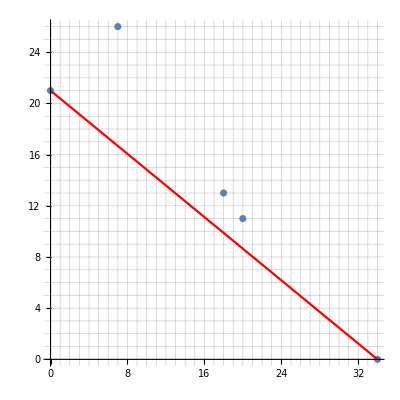

```mathematica
wRules=CoefficientRules[fabNormalForm,{w,z},"NegativeLexicographic"]
wPowers=DeleteDuplicates@wRules[[All,1]][[All,1]]
wRules[[All,1]]
plotTable=Table[
rules=Select[wRules,#[[1,1]]==wPowers[[i]]&];
rules[[1,1]],
{i,1,Length@wPowers}
]
aForm[fabNormalForm]
maxX=plotTable[[-1,1]]
maxY=plotTable[[1,2]]+5
segmentLine[x_]:=-fmu/fDegree x+fmu;
p1=Plot[segmentLine[x],{x,0,maxX},PlotStyle->Red];
lp1=ListPlot[plotTable,Axes->True,GridLines->{Table[i,{i,0,maxX,1}],Table[i,{i,0,maxY,1}]},AspectRatio->1];
Show[{lp1,p1}]
```

```mathematica
fmu
wPowers
recomInfinityTerms=Table[
fNormalRules0=Select[wRules,#[[1,1]]==wPowers[[wPowersIndex]]&];
rules0Exp=fNormalRules0[[All,1]];
rules0Vals=fNormalRules0[[All,2]];
fInfExp=z^(rules0Exp[[All,2]]-fmu+wPowers[[wPowersIndex]]);
(Plus@@MapThread[(#1 #2)&,{rules0Vals,fInfExp}])w^wPowers[[wPowersIndex]],
{wPowersIndex,1,Length@wPowers}
];
recomInfinityF=Plus@@recomInfinityTerms;
(*Print[Style["f: "],Style[funDisplay,10]]*)
Print[Style["rI: "],Style[aForm[recomInfinityF],10]]
Print[Style["rN: "],Style[aForm[fabNormalForm],10]]
aForm[recomInfinityF]//TeXForm
```

21

{0,7,18,20,34}

rI: (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

rN: (-z^21-2 z^30-6 z^33)+(3 z^26) w^7+(6 z^13+6 z^23+8 z^28) w^18+(9 z^11) w^20+(2+4 z+7 z^2+6 z^3) w^34

\left(-1-2 z^9-6 z^{12}\right)+\left(3 z^{12}\right) w^7+\left(6 z^{10}+6 z^{20}+8 z^{25}\right) w^{18}+\left(9 z^{10}\right)
   w^{20}+\left(2 z^{13}+4 z^{14}+7 z^{15}+6 z^{16}\right) w^{34}

```mathematica
(*
 now use highest power in a_0 for fDelta
*)
infWRules=CoefficientRules[recomInfinityF,{w,z},"NegativeLexicographic"]
fDelta=Max@infWRules[[All,1]][[All,2]]

(* fDelta=18*)
(*
 now invert recomInfinityF to function
*)
infWRules=CoefficientRules[recomInfinityF,{w,z},"NegativeLexicographic"];
infWPowers=DeleteDuplicates@infWRules[[All,1]][[All,1]];

reformedFList=Table[
infWRules0=Select[infWRules,#[[1,1]]==infWPowers[[coefIndex]]&];
infW0Powers=infWRules0[[All,1,2]];
infW0Coef=infWRules0[[All,2]];
(*Print["infW0Powers: ",infW0Powers];*)
reverseCoef=Reverse@infW0Coef;
reversePowers=Reverse@infW0Powers;
recomF=(Plus@@MapThread[#1 z^(fDelta-#2)&,{reverseCoef,reversePowers}]) w^infWPowers[[coefIndex]];
(*Print[Style["f: "],Style[funDisplay,10]];*)
recomF,
{coefIndex,1,Length@infWPowers}
];
theReformedF=Plus@@reformedFList;
Print["reformed f: ",Style[aForm[theReformedF],10]];
Print[Style["reformed f_∞: "],Style[aForm[recomInfinityF],10]]
Print[Style["reformed f_n: "],Style[aForm[fabNormalForm],10]]

(*myInfF=aForm[Expand[z^fDelta (theReformedF/.z->1/z)]];
Print["myIniF: ",Style[aForm[myInfF],10]];
aForm[recomInfinityF]
*)
```

{{0,0}→-1,{0,9}→-2,{0,12}→-6,{7,12}→3,{18,10}→6,{18,20}→6,{18,25}→8,{20,10}→9,{34,13}→2,{34,14}→4,{34,15}→7,{34,16}→6}

25

reformed f: (-6 z^13-2 z^16-1 z^25)+(3 z^13) w^7+(8+6 z^5+6 z^15) w^18+(9 z^15) w^20+(6 z^9+7 z^10+4 z^11+2 z^12) w^34

reformed f_∞: (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

reformed f_n: (-z^21-2 z^30-6 z^33)+(3 z^26) w^7+(6 z^13+6 z^23+8 z^28) w^18+(9 z^11) w^20+(2+4 z+7 z^2+6 z^3) w^34

```mathematica
aForm[theReformedF]//TeXForm
```

\left(-6 z^{13}-2 z^{16}-1 z^{25}\right)+\left(3 z^{13}\right) w^7+\left(8+6 z^5+6 z^{15}\right) w^{18}+\left(9 z^{15}\right)
   w^{20}+\left(6 z^9+7 z^{10}+4 z^{11}+2 z^{12}\right) w^{34}

```mathematica
fmu
testInf=Expand[z^fDelta(theReformedF/.z->1/z)];
Style[aForm[testInf],10]
testN=Expand[z^fmu (testInf/.w->w/z)];
Style[aForm[testN],10]
```

21

(-1-2 z^5-3 z^8)+(8 z^21+7 z^22) w^2+(3 z^5+2 z^18+9 z^19) w^10+(z^20) w^12+(-2 z^13+4 z^14+5 z^15+7 z^16) w^34

(-z^21-2 z^26-3 z^29)+(8 z^40+7 z^41) w^2+(3 z^16+2 z^29+9 z^30) w^10+(z^29) w^12+(-2+4 z+5 z^2+7 z^3) w^34

### Plots

#### Contour plots

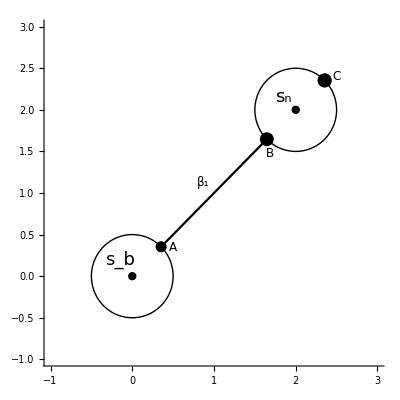

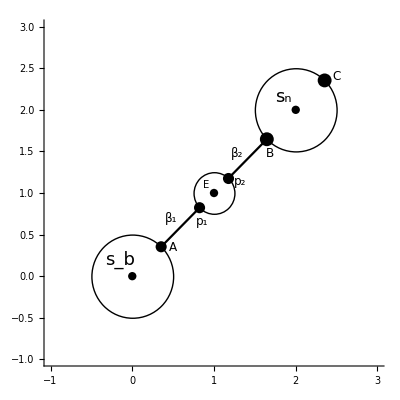

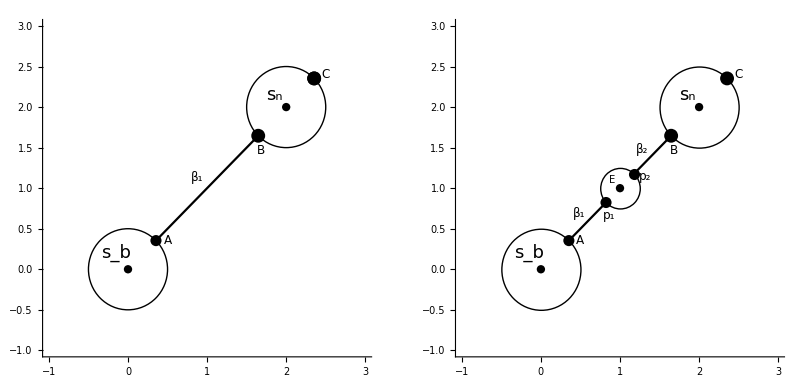

```mathematica
(*
 draw plot of contours 
*)

basePoint=0;
basePointG=Graphics@{PointSize[0.015],Point@{0,0}};
r1=1/2;
nextPoint=2+2 I;
point2=1+1I;
r3=1/4;
nextPointG=Graphics@{PointSize[0.015],Point@ReIm@nextPoint};
point2G=Graphics@{PointSize[0.015],Point@ReIm@point2};
r2=1/2;
{baseNDZ,nextNDZ,nextNDZ2}=getIntegrationData2[basePoint,r1,nextPoint,r2,30];
{baseNDZ2,nextNDZb,nextNDZ3}=getIntegrationData2[basePoint,r1,point2,r3,30];
{baseNDZ3,nextNDZ3,nextNDZ4}=getIntegrationData2[nextPoint,r2,point2,r3,30];

baseNDZG=Graphics@{PointSize[0.02],Point@ReIm@baseNDZ};

nextNDZG=Graphics@{PointSize[0.025],Point@ReIm@nextNDZ};
nextNDZ2G=Graphics@{PointSize[0.025],Point@ReIm@nextNDZ2};

baseCircleG=Graphics@{Circle[ReIm@basePoint,r1]};
nextCircleG=Graphics@{Circle[ReIm@nextPoint,r2]};
nextCircleG2=Graphics@{Circle[ReIm@point2,r3]};
nextCircleArcG=Graphics@{Red,Circle[ReIm@point2,r3,{Arg[nextNDZb],Arg[nextNDZb]-Pi}]};
nextCircleArcG2=Graphics@{Black,Dashed,Circle[ReIm@point2,r3,{Arg[nextNDZb],Arg[nextNDZb]+Pi}]};
cTable1=Table[ReIm[point2+r3 Exp[I t]],{t,Arg[nextNDZb]-Pi,Arg[nextNDZb]-0.1,1/30}];
arrow1=Graphics@{Arrowheads[0.025],Arrow[cTable1]};

cTable2=Table[ReIm[point2+r3 Exp[I t]],{t,Arg[nextNDZb]+Pi,Arg[nextNDZb]+0.175,-1/30}];
arrow2=Graphics@{Arrowheads[0.025],Arrow[cTable2]};
nextCircleArcG3=Graphics@{Red,Circle[ReIm@point2,r3]};


zTrace[t_]:=baseNDZ(1-t)+nextNDZ t;
zTrace2[t_]:=baseNDZ(1-t)+nextNDZb t;
zTrace3[t_]:=nextNDZ3(1-t)+nextNDZ t;
nextNDZ3G=Graphics@{PointSize[0.02],Point@ReIm@nextNDZ3};
dPointG=Graphics@{PointSize[0.02],Point@ReIm@nextNDZ2};
ePointG=Graphics@{PointSize[0.02],Point@ReIm@nextNDZb};
(*zTrace2[t_]:=baseSingularPoint(1-t)+nextTestSing t;*)
baseNDPointG=Graphics@{PointSize[0.2],Black,Point@ReIm@((baseNDZ+nextNDZ)/2)};
pp1=ParametricPlot[ReIm@zTrace[t],{t,0,1},AspectRatio->1,PlotStyle->Black];
pp2=ParametricPlot[ReIm@zTrace2[t],{t,0,1},AspectRatio->1,PlotStyle->Black];
pp3=ParametricPlot[ReIm@zTrace3[t],{t,0,1},AspectRatio->1,PlotStyle->Black];
pRange=Options[pp1,PlotRange];
pVals=PlotRange/.pRange;
thePlotRange=pVals+{{-0.2,0.4},{-0.1,0.1}};
text1=Graphics@Text[Style["A",12],{0.5,0.35}];
text2=Graphics@Text[Style["β_1",12],{0.87,1.13}];
text2b=Graphics@Text[Style["β_1",12],{0.48,0.69}];
text2c=Graphics@Text[Style["β_2",12],{1.24,0.75}];
text3c=Graphics@Text[Style["β_2",12],{1.28,1.48}];
text4c=Graphics@Text[Style["β_3",12],{0.73,1.25}];
text3=Graphics@Text[Style["B",12],{1.68,1.47}];
text5=Graphics@Text[Style["B",12],{3.7,3.4}];
text5C=Graphics@Text[Style["C",12],{2.5,2.4}];

text30=Graphics@Text[Style["B",12],{1.68,1.47}];


text7=Graphics@Text[Style["s_b",18],{-0.15,0.2}];
text8=Graphics@Text[Style["s_n",18],{1.85,2.15}];
text9=Graphics@Text[Style["B",12],{.86,0.66}];
text10=Graphics@Text[Style["E",10],{0.9,1.1}];
text11=Graphics@Text[Style["p_2",12],{1.32,1.14}];
text12=Graphics@Text[Style["p_1",12],{0.86,.66}];
text13=Graphics@Text[Style["C",12],{2.5,2.4}];





path1=Show[{basePointG,nextPointG,baseCircleG,nextCircleG,baseNDZG,nextNDZG,nextNDZ2G,pp1,text1,text2,text7,text8,text5C,nextNDZ2G,text30},PlotRange->{{-1,3},{-1,3}},Axes->True(*PlotLabel->Style["Integration path between s_b and s_n",12,Bold,Black]*)];


path2=Show[{basePointG,baseCircleG,nextCircleG,pp3,pp2,text1,text3,point2G,ePointG,nextCircleG2,text7,text8,text10,nextNDZ3G,text2b,text3c,text12,text11,nextPointG,baseNDZG,nextNDZG,text13,nextNDZ2G},Axes->True,PlotRange->{{-1,3},{-1,3}}(*,PlotLabel->Column[{Style["Integration path between s_b and s_n",12,Bold,Black],Style["with intervening R",12,Bold,Black]},Center]*)
];

Show[path1]
Show[path2]
GraphicsRow[{Show[{path1}],Show[path2]}]
```

#### Polygon diagrams

{{0,14},{2,10},{3,15},{4,7},{6,8},{8,1},{9,0},{10,0}}

{{0,9},{1,3},{2,6},{3,5},{4,1},{5,5},{6,10},{7,6},{8,1},{9,8}}

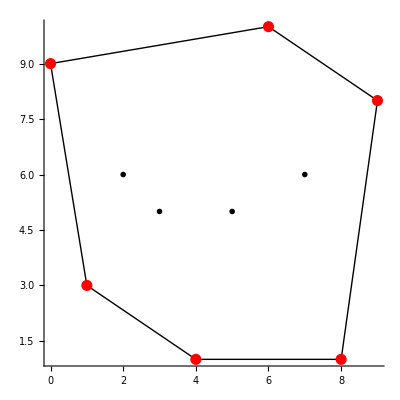

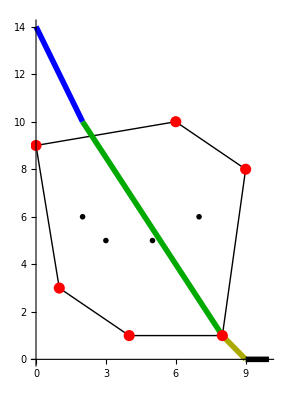

```mathematica
points1={{0,9},{1,3},{2,6},{3,5},{4,1},{5,5},{6,10},{7,6},{8,1},{9,8}};
points2={{0,6},{1,1},{2,9},{3,3},{4,6},{5,4},{6,10},{7,7},{8,2},{9,6},{10,5}};
points3={{0,14},{1,∞},{2,10},{3,15},{4,7},{5,∞},{6,8},{7,∞},{8,1},{9,0},{10,0}};
points=DeleteCases[points3,_?(#[[2]]==∞&)]
points=points1

hullIndexes=ConvexHull[points];
hullPoints=points[[hullIndexes]];

polygonPointsG=Graphics@{PointSize[0.01],Black,Point@points};
convexHullG=Graphics@{Line@Append[points[[hullIndexes]],points[[hullIndexes[[1]]]]]};
hullPointsG=Graphics@{PointSize[0.02],Red,Point@hullPoints};
line1=Graphics@{Blue,Thickness[0.01],Line[{{0,14},{2,10}}]};
line2=Graphics@{Darker@Green,Thickness[0.01],Line[{{2,10},{8,1}}]};
line3=Graphics@{Darker@Yellow,Thickness[0.01],Line[{{8,1},{9,0}}]};
line4=Graphics@{Black,Thickness[0.01],Line[{{9,0},{10,0}}]};
Show[{convexHullG,polygonPointsG,hullPointsG},Axes->True,AxesOrigin->{0,0}]
Show[{convexHullG,line1,line2,line3,line4,polygonPointsG,hullPointsG},Axes->True,AxesOrigin->{0,0}]
```

{{0,14},{2,10},{3,15},{4,7},{6,8},{8,1},{9,0},{10,0}}

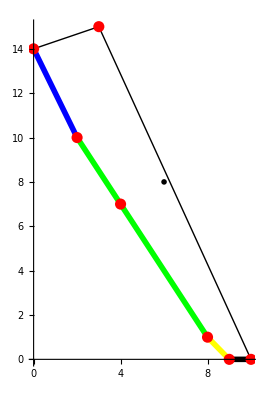

```mathematica
(0,14),(2,10)
(2,10),(8,1)
(8,1),(9,0)
(9,0),(10,0)
(10,0),(3,15)
(3,15),(0,14)
```

#### Plots

```mathematica
text1=Graphics@Text[Style["S_1",12],{1,12.6}];
```

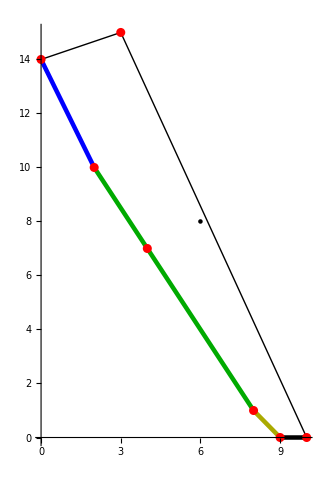
```mathematica
convex1=-Graphics-
```

-Graphics-

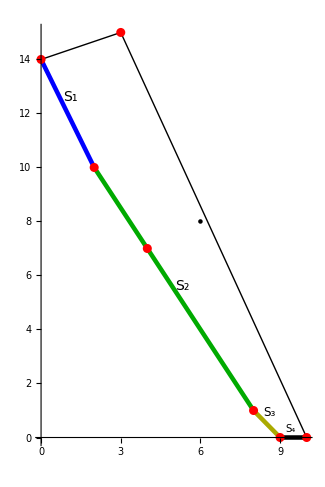

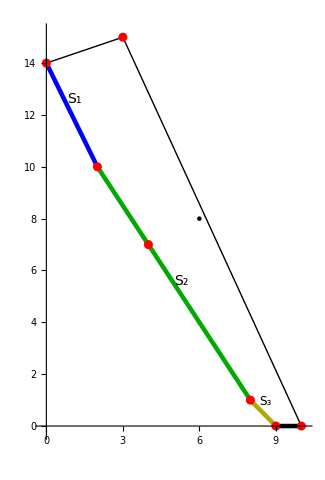

```mathematica
text1=Graphics@Text[Style["S_1",14],{1.1,12.6}];
 text2=Graphics@Text[Style["S_2",14],{5.3,5.6}];
 text3=Graphics@Text[Style["S_3",12],{8.6,0.93}];
 text4=Graphics@Text[Style["S_4",10],{9.4,0.33}];
Show[{convex1,text1,text2,text3,text4}]
```

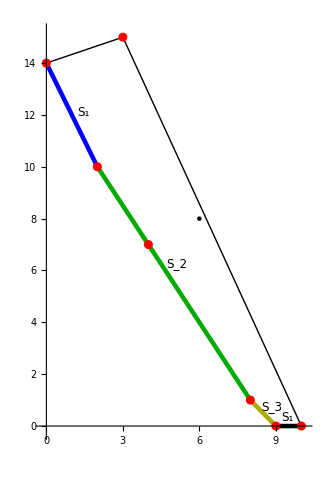

## Section 2: Compute/Retrieve singular data

### Retrieve singular points

```mathematica
(*
 retrieve singular points from disc
*)
If[FileExistsQ[singularDataFileName[$theTestCase]],
theData=Import[singularDataFileName[$theTestCase]];

{$theSingularList,$poleIndexes,$minRadiusArray,res,$zeroIndexes,$nearestDistanceArray,$rNormArray}=theData;

Print["Total singular points: ",Length@$theSingularList];

Print["Precision of singular points: ",Precision@$theSingularList];Print["Total poles: ",Length@$poleIndexes];
Print[Style["s_p indexes: ",Red],Style[$poleIndexes,Red]];
Print[Style["s_z indexes: ",Red],Style[$zeroIndexes,Blue]];

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
If[$theSingularList[[1]]==0,
Print["Smallest sing power: ",N[$theSingularList[[2]]^maxZ,10]];
,
Print["Smallest sing power: ",N[$theSingularList[[1]]^maxZ,10]];
]; 
minSingSeparation=3Min@$minRadiusArray//N;
minSingAccFactor=-MantissaExponent[minSingSeparation][[2]]+5;
Print["minSingAccFactor: ",minSingAccFactor];
(*res=Import[resultantFileName[$theTestCase]];*)
(*
 get reformed funtions
*)
Print["Retrieving reformedFunctionTable . . ."];
If[FileExistsQ[reformedFunctionTableFileName[$theTestCase]],
reformedFunctionTable=Import[reformedFunctionTableFileName[$theTestCase]];
,
Print[Style[reformedFunctionTableFileName[$theTestCase]<>" not found during import.",Red]];
];
,
Print[Style[singularDataFileName[$theTestCase]<>" not found during import.",Red]];
];
```

D:\algFunctionBook\Data\testCase0064\singularData.m not found during import.

### Use AsymptoticSolve to compute series

{45.0828,Null}

(-1.03078752567445731922036302713958402167206294512565620770068252843097350518763810105414591305996393751265667937377068716760248588019215124518737570479914369371256869707363246996328770412742301122583746761198265128500061526025770251520674604136490677330866184617737903763065260096381405333298305432940823767067829813150402275085740325559160243423449055003105286944997647596223266117594962644957664032538710450761250089767638401101618263977477910055761128937241530074781583576275993611124032275829470821633266302172152999054800611178015363923380388979777703283069818292699330969522933285297524098829780490891962354979426796240929843503096040446889205554311150081465896528715736737692181865983840100888484089029744904533196013391138394046150909684299558660309153214470173882440355320065351354286859411986199795091531391932658407284558027327390551277111266911728297043863156292157181576920756314873004350933647739605887037926710044331327004313439831187887524991663076180852618824640961864275724737112687639635168681031+0.10489161204031145673306123259607605442325038762405562366907837400001917669638419999477133201731245582919378579906860488191264201712870324337808885203165147817107643301034829764945122888851332774428917393106661076129738544803731608352828595951616003424031810556699859956460453732037796297759574207887119893717443948475079184060303609181934991390716427236093241918794031322786459389045352868292120278358349189434794109212177091308899057471818248278253673673003432560814174156424390687593843534411123417424600002437201135373496932702267167227497058120485668915675724428057514319585430194679316485285750012226322227097923120874597517088941116115217798140560212713269282527012180387261881890164454287968836676652395712746701992419056197281926659674617359227597999482882013460496324930997761739126435717075519704833181107253454885512005710208380891645117982694495112819872248810763593626576414103093598888908291063757175131264650805913397369507916147826195272404845829453966433267842228933107756761313547727566252208145 ⅈ)-(0.4571013197266286875690156059730980841911020517404015599083737596924492196689963894782708531554625919041568534487666128614020432478975188331739205552844538642542914484647152371033578400318535537294697033069858860191071515813352228384841083198177572186706214174187659035542548190002354047738950900163129317582076855005546575209744255628631800600493051493129989270897437139270084599083042603641842968108389646934882806280713504017208183722749811354963466239622009660980217822373745182472720477573392540351051763892256045269271592426071679216002135703323591936769054782302482130693163137428347839675143768874447276598309237675397523579645771512859775432804430672809717346104835655573502313696757618608623244631064644559200827892420779962524409710908697485856532328127715338311424913595694264237845778356962696610139891689042215432165899857506052034026307636517442195246013779095942281065920625922471920947791020637480768060995979246124800415950316457700051008972694631974766498546498677984779472629828068141485794-0.06090126749259226284607911665439478804645125626243943987913439619236438008663998351812163153344701953338473860066755552039971700527299011007816198227066054447331146407168901998756416710063332623075455192384289424514992132888221452509400827891559803110887520569145330449163269975728100256629614205451465915823910734938242061821363300183981125999953039276110359952271848143012684970514187247730367688063559265376086537209106392064690702362167254443000852550459193089620854124494010632651970836193250062531062710556551311771017311854145440230917278339047801038049059388665582485810161265803614771838470637592574300557049772656387375287193840281383093605611954652280418305507054799589799924502139971558340386275745728457454940697368004387688529694328977989075867147329535823398264670808893609462969941245519880532977766728624379004781919829358510638762100731820106884074139179975804084610843169751003181044124212667864487876401456820140278065797032731936296447031702680195434972438018266104166503112826619786049858 ⅈ) ((0.9291082476915902106730977768710446786784083372531918127273974812875229241757181968257053085919547937386433459468504511690569306370771376687442786131966623542861018520405831573457158786480061568051421305628557240903993826310883791990423098935592877909257727180339274998469896327232690672860441395214220909216449890512755658791344133593269912654349518331571171141249282221258385971933619930316968731478742170042681398042000358116275057746555373148029241386303328109832049343324650588931505189134608316598733167833678899834622409503632759624783474623904924810890688498033041429665113464778070702047776098743824958265548184159402223719264291402552191411033839484765360538376090197427818328421954698646975679858148598736525099788315768961708417233843882772703175283007633058614900904223277102237182798464342381428368470446368368774826181306529273076580218688232638432995060413448838840797905462223360451946159196748468045878505446902841518339914531591751076442151002419508167629900829714934730650812168684655293092180650628+0.2357876731004600615436597377047233798306377754134797749049807628177249020279490865065500526550584476824265363420560487983602264375242201674181415998513543527763713609577474726616136126955477318337922708431467932664067976974685488924589992443255025778306856730688341618818056068352429858223287043402197750207422810313011709778358231543495735302279677880312463075196556317382561612712320514090257582978887434137168647738634260037530220219112120058841450692602309981484949992970056153768911224700868945377542818353056802506492083817283321447485472007623354940826500187264915133862835495922478350964960120021417945356096083578422732658901959360937943717427426377075560571176928741370958500007850639554431203832138439206050443145272802453080533589879180922275191588952598032349087876330150042324944246857070818854756686726869610129651410865937870831692066805228057662220321549396684126409764533896620712565762221603079311248020019424157083384748801844449106830768411585014746411796917297203708360327496815709463078780099976 ⅈ)+z)-(4.50601559333702331263286078591312417961690382179837578359679369715972505231825834184963928486512003563051266890154352917602266132657151893371208452336881792307113499934265380402784087790758715444215899505024875543316061000916555363292743029935767529758215784331992503239161568031405624540138303845095221540827884478048088778437066393095549768253522118292027634451325570648971140787091615415515216674784793851018836040439780218430524632457887869348304029512001907539540573168074450765433224617687597681047009746077084693222754976461876328030416963577550631513367146884897670118804955004686933351069360927720689233593917963470856250813582658811907511550924978819268597920145503857468583955765369262955998920504966936961662077065977101110419704361654570684024042547872875563492887525236606503138246356525560178056828777355574891543329005327645091787158130144029949262580725877924949156849248056304935667491683227078859166843398426503152794768810712806883037823831012471864476592615120128216435841882803194500759-2.14195430313680038570464420287156330884915468003995103096524898323880224163338081223309932522485835650685015628365130134042676655333796579995944647590958315375362016685374073537816279464784543853001260083906189951385053120772213060596463141768783090514020410335407350126496772046209097874320572245778498478439174703791587591148078889287630119233283571709456989508768021612784215986888189133564379122423053294595529743060146111078708033921745204341295250551149712730036556424080930603720115282046132409676647385924127643790535374145434346506410599494650095131502104671368893141438036031201226661798985733710425814925482462170772946598123737717059987959837233621702781864612780041224651984139892562157127776593273900828703277714354775172618240760576005598301805658983222009467071989459840288407462736262054324500864022932595357427177405201831785475649032025003504120370692409226579646605913207976496774688662521969232559697469641086236241040390731849947853038616131105438192421873212774936358973554590116591018 ⅈ) (((0.9291082476915902106730977768710446786784083372531918127273974812875229241757181968257053085919547937386433459468504511690569306370771376687442786131966623542861018520405831573457158786480061568051421305628557240903993826310883791990423098935592877909257727180339274998469896327232690672860441395214220909216449890512755658791344133593269912654349518331571171141249282221258385971933619930316968731478742170042681398042000358116275057746555373148029241386303328109832049343324650588931505189134608316598733167833678899834622409503632759624783474623904924810890688498033041429665113464778070702047776098743824958265548184159402223719264291402552191411033839484765360538376090197427818328421954698646975679858148598736525099788315768961708417233843882772703175283007633058614900904223277102237182798464342381428368470446368368774826181306529273076580218688232638432995060413448838840797905462223360451946159196748468045878505446902841518339914531591751076442151002419508167629900829714934730650812168684655293092180650628+0.2357876731004600615436597377047233798306377754134797749049807628177249020279490865065500526550584476824265363420560487983602264375242201674181415998513543527763713609577474726616136126955477318337922708431467932664067976974685488924589992443255025778306856730688341618818056068352429858223287043402197750207422810313011709778358231543495735302279677880312463075196556317382561612712320514090257582978887434137168647738634260037530220219112120058841450692602309981484949992970056153768911224700868945377542818353056802506492083817283321447485472007623354940826500187264915133862835495922478350964960120021417945356096083578422732658901959360937943717427426377075560571176928741370958500007850639554431203832138439206050443145272802453080533589879180922275191588952598032349087876330150042324944246857070818854756686726869610129651410865937870831692066805228057662220321549396684126409764533896620712565762221603079311248020019424157083384748801844449106830768411585014746411796917297203708360327496815709463078780099976 ⅈ)+z))^2-(1.501324907012804852253108285031894071677413928022324801913106518053765903413387135279836507893721286301998093616558192903525613598178875992729512063381348525937316809688387499218634944301283090691626794092316126527684299996414270670672611960228439054284764050345162445419144578889177964280984922502600452657729619897967579085751484725401348383276337435878801883604916363121488669328699365547399517120862680787683623243335403482200985124485950856842963452396867977240341465161569438342166527435423171536147863469438416158421452209405732702556849319650856035020706015143487627679802967712091273699865057579850071889560692544959912169079502105415904766425648141616746642492656968770915734097076389201788898014666712044022401744680266493248564936833139095681965021998783634334214455317584142031170887368847578485283031862340563064403647119717899287177658436838158185535695252222002771393899416252836306353328315545520211032828054590495558706580368438052220995021861715579320041498948026304574273583219146852533-2.163022430420441385681093060971714733550994088273991866948263222361510176617277516856992811969938059657279820693990979795145638501382857348238458527976598880819329186848358779527846628276430372265409417223825897358420388842605214697874366618462738191347845685513991345860451383031348820646999178555199629797325471100174650524278380590898642365467680513995965798234398192935463566172562483429256468758334585434391272822237054564754170555579928443436836276874309119142277466100572239200279626532809289668615342941065763687288112941875747012455906867329960774704570927766837105375119367499580666804249687446283291789013853634478610684601955661281751005426224429630132598265622766948246853433449235129466347353376974298981567322146302004555186462812675173551715773604405919199639181298301721315345947660227756972891508396146083523981357415999199096390247802937570091765799554416175816237238397506360677984955860383733419963109632513102821102385753002733057934581728448304007057148054147330904646770661673609721 ⅈ) (((0.9291082476915902106730977768710446786784083372531918127273974812875229241757181968257053085919547937386433459468504511690569306370771376687442786131966623542861018520405831573457158786480061568051421305628557240903993826310883791990423098935592877909257727180339274998469896327232690672860441395214220909216449890512755658791344133593269912654349518331571171141249282221258385971933619930316968731478742170042681398042000358116275057746555373148029241386303328109832049343324650588931505189134608316598733167833678899834622409503632759624783474623904924810890688498033041429665113464778070702047776098743824958265548184159402223719264291402552191411033839484765360538376090197427818328421954698646975679858148598736525099788315768961708417233843882772703175283007633058614900904223277102237182798464342381428368470446368368774826181306529273076580218688232638432995060413448838840797905462223360451946159196748468045878505446902841518339914531591751076442151002419508167629900829714934730650812168684655293092180650628+0.2357876731004600615436597377047233798306377754134797749049807628177249020279490865065500526550584476824265363420560487983602264375242201674181415998513543527763713609577474726616136126955477318337922708431467932664067976974685488924589992443255025778306856730688341618818056068352429858223287043402197750207422810313011709778358231543495735302279677880312463075196556317382561612712320514090257582978887434137168647738634260037530220219112120058841450692602309981484949992970056153768911224700868945377542818353056802506492083817283321447485472007623354940826500187264915133862835495922478350964960120021417945356096083578422732658901959360937943717427426377075560571176928741370958500007850639554431203832138439206050443145272802453080533589879180922275191588952598032349087876330150042324944246857070818854756686726869610129651410865937870831692066805228057662220321549396684126409764533896620712565762221603079311248020019424157083384748801844449106830768411585014746411796917297203708360327496815709463078780099976 ⅈ)+z))^3-(4.728323090850902394952682360396189538912340520226400665681449682297436699193308805358925759860435129827316143136367245941405056516578332861383568152278066106976914765363605982471206288127716298137400937788436817973940724574426408850907265159076261586212523226264887468563903707217483803961627702722469974408957449636957916610800430194273104611653764585733388320175288242139404739002342389401476947641685829531034934543030832349498492143516635506007589851688335122343791534634730802746167388658793193498779629164851063354318194323381135174766959167377506118903270138968392734673458073575089443993767635276073701485022945308636788254944828623681826031302656547912160562406737873698935130851824576925509436948175430455447941519070597525484173371349117416348482880398644842783386338541684354020368602448229933085911957133590709500340476256621445038950439854455585246101024836961502803375667237051902851234655738434237855308580744545940380742592689700997072660359171843996211545702903834327290427142038418448+317.3692931206124134054968789884011416875740495422167125367627142705229535753702541828215708418257732741421462845295639446233727605007607000160063509270121271369091757233856003203433981858404037320343164455659512274828158770586228335897917180429086051924926823909154795723838357582729082025762818990279872228890916919997040270170863892459586018868801425678222709271547863190589487231091852557587602512173214009508565825989874862414305137833140296311291567520096227397149458490797356068110349120543189361837919851374624265947461037145842739854909092719910673296165407021463020429076111506184869156205983061314816267630516169305034374287502621557897752964855591168416946326778130856600110676700470513369274662502912343190403697524228307502148675030695538244763152357880393137271072407260267986362514114481295454942276910359827422391150457888485184329575830949390042900645116112519078795931276835669440159531334512056420568777271056051629083040430892806183739219278460800894580277972334419124753793923634870343 ⅈ) (((0.9291082476915902106730977768710446786784083372531918127273974812875229241757181968257053085919547937386433459468504511690569306370771376687442786131966623542861018520405831573457158786480061568051421305628557240903993826310883791990423098935592877909257727180339274998469896327232690672860441395214220909216449890512755658791344133593269912654349518331571171141249282221258385971933619930316968731478742170042681398042000358116275057746555373148029241386303328109832049343324650588931505189134608316598733167833678899834622409503632759624783474623904924810890688498033041429665113464778070702047776098743824958265548184159402223719264291402552191411033839484765360538376090197427818328421954698646975679858148598736525099788315768961708417233843882772703175283007633058614900904223277102237182798464342381428368470446368368774826181306529273076580218688232638432995060413448838840797905462223360451946159196748468045878505446902841518339914531591751076442151002419508167629900829714934730650812168684655293092180650628+0.2357876731004600615436597377047233798306377754134797749049807628177249020279490865065500526550584476824265363420560487983602264375242201674181415998513543527763713609577474726616136126955477318337922708431467932664067976974685488924589992443255025778306856730688341618818056068352429858223287043402197750207422810313011709778358231543495735302279677880312463075196556317382561612712320514090257582978887434137168647738634260037530220219112120058841450692602309981484949992970056153768911224700868945377542818353056802506492083817283321447485472007623354940826500187264915133862835495922478350964960120021417945356096083578422732658901959360937943717427426377075560571176928741370958500007850639554431203832138439206050443145272802453080533589879180922275191588952598032349087876330150042324944246857070818854756686726869610129651410865937870831692066805228057662220321549396684126409764533896620712565762221603079311248020019424157083384748801844449106830768411585014746411796917297203708360327496815709463078780099976 ⅈ)+z))^4-(1507.07514535659155282549918838100347528124120991362671333687692972671315485556023297701847981656037367166010168356119642017373879365007687425459450418891907312255754571512540592960205331955121782457851124106022792759811709655671988183805461871435437988363998068054932844735839246922560876363422139384593520324907101428341934288200595957257293064198131724843287633381822361107931451365559729086960344004821789341958262866267644173859587758363575704089121372556148200324399297066156530710950227670362148996901667395970962371490509462003066963402242659449741651710703059582115486609805414261116501260476556187386024626891519796174318251812273851665768335753642854010112258423125871101978274254449336414013409509567164892987762600140086565642281395527911935982119722585564309699775975910400448629569930651469067445759228600293761229352765325614863609638234228601881888324167966386052023490928797089841693045293236491227631327424171025202447430021467901633710703880143464901707679122058533268533632123955433472+699.797504134967684089429061474992142444468041123681467680174397028420125812316249150070631682982447491517767018657087951265821473761950358688873955030808370702509343565729825676009495934772154602647021703570573085400462207659530174179816157144525206139460954787457673539477176896834814807562061613800745247167331480630270267588380486207174136580406962415135024031212608136068515076806435575706831524042254301272666697824072127320160948056869535033796180068008663544020738630825840048862409593945505434200283323125820148910900357008254262104628106878168154279411569768938791797332997309527482321673495513248422324876097804720136266570125832468356185980686981986203917047923904944337021949479669760850179769669271836180191583038596994721008633370390364339597074166395418627009753107485330622992390578255218068402215304124479315662322858881301153356447421885491585421189583076274461863880636901933506266101026004354953742881620050979219141083820212451161632256253632008795038891778716344182170384590507185904 ⅈ) (((0.9291082476915902106730977768710446786784083372531918127273974812875229241757181968257053085919547937386433459468504511690569306370771376687442786131966623542861018520405831573457158786480061568051421305628557240903993826310883791990423098935592877909257727180339274998469896327232690672860441395214220909216449890512755658791344133593269912654349518331571171141249282221258385971933619930316968731478742170042681398042000358116275057746555373148029241386303328109832049343324650588931505189134608316598733167833678899834622409503632759624783474623904924810890688498033041429665113464778070702047776098743824958265548184159402223719264291402552191411033839484765360538376090197427818328421954698646975679858148598736525099788315768961708417233843882772703175283007633058614900904223277102237182798464342381428368470446368368774826181306529273076580218688232638432995060413448838840797905462223360451946159196748468045878505446902841518339914531591751076442151002419508167629900829714934730650812168684655293092180650628+0.2357876731004600615436597377047233798306377754134797749049807628177249020279490865065500526550584476824265363420560487983602264375242201674181415998513543527763713609577474726616136126955477318337922708431467932664067976974685488924589992443255025778306856730688341618818056068352429858223287043402197750207422810313011709778358231543495735302279677880312463075196556317382561612712320514090257582978887434137168647738634260037530220219112120058841450692602309981484949992970056153768911224700868945377542818353056802506492083817283321447485472007623354940826500187264915133862835495922478350964960120021417945356096083578422732658901959360937943717427426377075560571176928741370958500007850639554431203832138439206050443145272802453080533589879180922275191588952598032349087876330150042324944246857070818854756686726869610129651410865937870831692066805228057662220321549396684126409764533896620712565762221603079311248020019424157083384748801844449106830768411585014746411796917297203708360327496815709463078780099976 ⅈ)+z))^5

```mathematica
mmSeries[[1]]
```

-(-5/3)^(1/9) z^(4/9)-1/36 (-5/3)^(1/9) z^(13/9)+1/324 (-5/3)^(1/9) z^(22/9)-(17 (-5/3)^(1/9) z^(31/9))/34992+(116861 (-5/3)^(1/9) z^(40/9))/2519424

```mathematica
(* end of section *)
```

### Compute singular points

```mathematica
$workingPrecision=1000;

at=AbsoluteTiming[{$theSingularList,$poleIndexes,$minRadiusArray,res,$zeroIndexes,$nearestDistanceArray,$rNormArray}=getSingularPoints[$theFunction,$workingPrecision,True];
If[$theSingularList=="-1",
Print[Style["Encountered error with getSingular Points!",Red]];
Abort[];
];
];
$singularPerimeters=$minRadiusArray;
$singularNorms=$rNormArray;
$singularDistances=$nearestDistanceArray;
(*
 add 0 for TestCase0006 for book
*)
(*If[subDirectory=="testCase0006",
PrependTo[$theSingularList,0];
$minRadiusArray={1/3,1/3,1/3};
];*)
(*
 add 0 for testCaseFInif
*)
(*If[subDirectory=="testCaseFInif",
PrependTo[$theSingularList,0];
$minRadiusArray={1/3,1/3,1/3};
];
*)
If[subDirectory=="testCase0001Inf0",
singPerim=1/3 Abs[$theSingularList[[1]]];
PrependTo[$theSingularList,0];
$minRadiusArray={singPerim,singPerim,singPerim};
];


(*If[subDirectory=="testCase0038",
singPerim=1/3 Abs[$theSingularList[[1]]];
PrependTo[$theSingularList,0];
$minRadiusArray={singPerim,singPerim,singPerim};
];

*)


Print["Total singular points: ",Length@$theSingularList];
Print[Style["Time to compute singular points: ",Red,Bold],at[[1]]];
singPrec=Floor@Precision@$theSingularList;
If[Abs[$theSingularList[[1]]]<10^(-(singPrec-$acf)),
Print[Style["Zero is a singular point",Bold,Red]];
];
If[Length@$theSingularList>1,
minSingSeparation=3Min@$minRadiusArray//N;
minSingAccFactor=-MantissaExponent[minSingSeparation][[2]]+5;
Print["minSingAccFactor: ",minSingAccFactor];
N[$theSingularList[[1;;2]],20];
];

 Export[singularDataFileName[$theTestCase],{$theSingularList,$poleIndexes,$minRadiusArray,res,$zeroIndexes,$nearestDistanceArray,$rNormArray}];
Export[resultantFileName[$theTestCase],res];

reformFlags={False,False,False};
compareFactor=400
{reformedWRules,theReformedIndexes}=getReformedIndexes[$theFunction,$theSingularList,$zeroIndexes,$poleIndexes,reformFlags,compareFactor];
(* singularIndex,reformedFunction  returned *)

genericIndexes=Complement[Range[1,Length@$theSingularList],DeleteDuplicates[theReformedIndexes]];

reformedFunctionTable=getReformedFunctionTable[reformedWRules,theReformedIndexes,reformFlags];
Export[reformedFunctionTableFileName[$theTestCase],reformedFunctionTable];
 g1=Prepend[reformedWRules,{"wCoef","Indexes"}];
g2=Prepend[g1,{"Zero coefficient indexes",SpanFromLeft}];
aForm[$theFunction]
Grid[g2]
```

Time to compute resultant: 0.0078345

Time to compute singular points: 0.0688452

Total singular points: 45

Precision of singular points: 1000.

Total poles: 5

Pole indexes: {7,8,33,34,37}

Total zero points: 0

Zero indexes: {}

Min singular perimeter: 0.00416089

Smallest singular points: {-0.461987-0.751542 ⅈ,-0.461987+0.751542 ⅈ}

Total singular points: 45

Time to compute singular points: 0.175594

minSingAccFactor: 6

400

(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

Zero coefficient indexes | 
wCoef | Indexes
{0} | {}
{1} | {}
{2} | {}
{3} | {}
{4} | {}
{5} | {{1,{7,8,33,34,37}}}

### Search singular files for removable singular points

```mathematica
(*
 find list of removable singular points
*)
PrintTemporary["File index: ",Dynamic@fIndex];
removableTable=Table[
fIndex=cIndex;
nextIndex=theSequence[[cIndex]];
If[TrueQ@FileExistsQ@seriesFileName[nextIndex],
{newSingularIndex,nextSing,nextCycleMetric,nextPoleList,nextConjList,removableList,nextSeries,nextSheetLinks,nextSingSequence,baseBranchTypeArray}=Import[seriesFileName[nextIndex]];
,
Print[Style[seriesFileName[nextIndex]<>" not found during import.",Red]];
Abort[];
];
{nextIndex,removableList},
{cIndex,1,2}
];

removableSingularFlag=False;
If[Length@Flatten@removableTable[[All,2]]>0,
Print["found removable singular points"];
removableSingularFlag=True;
,
Print["No removable singular points found"]
];
```

No removable singular points found

### Plot singular points and other

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

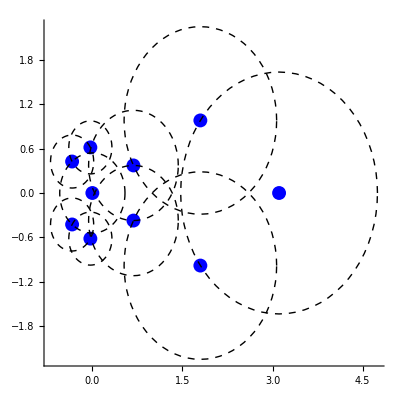

```mathematica
aForm[$theFunction]
 theSings=$theSingularList;
thePoles=$theSingularList[[$poleIndexes]];
theRingList=Abs[#]&/@ theSings;

singG=Graphics@{PointSize[0.025],Blue,Point@(ReIm@#&/@ theSings)};
poleG=Graphics@{PointSize[.025],Red,Point@(ReIm@#&/@ thePoles)};
singularPerimetersG=Graphics@MapThread[Circle[ReIm@#1,#2]&,{theSings,$minRadiusArray}];
nearestDistancesG=MapThread[{Dashed,Circle[ReIm@#1,#2]}&,{theSings,$nearestDistanceArray}];


(*annularRegionsG=Graphics@MapThread[{EdgeForm[],FaceForm[{Opacity[0.25],#1}],Annulus[{0,0},#2]}&,{annularColors[[1;;7]],theRingList[[All,2]]}];*)
theRingsG=Graphics@{Circle[{0,0},#]&/@ theRingList};
domain1G={Dashed,Red,Circle[{0,0},$nearestDistanceArray[[1]]]};

Show[{singG,poleG,Graphics@{nearestDistancesG(*,domain1G*)}},Axes->True,AspectRatio->1,PlotRange->2.5]
```

```mathematica
$theSingularList//N
```

{0.,-0.33719-0.426404 ⅈ,-0.33719+0.426404 ⅈ,-0.033241-0.617736 ⅈ,-0.033241+0.617736 ⅈ,0.684072-0.373365 ⅈ,0.684072+0.373365 ⅈ,1.79847-0.982974 ⅈ,1.79847+0.982974 ⅈ,3.10911}

{0.,0.543615,0.543615,0.61863,0.61863,0.779331,0.779331,2.04957,2.04957,3.10911}

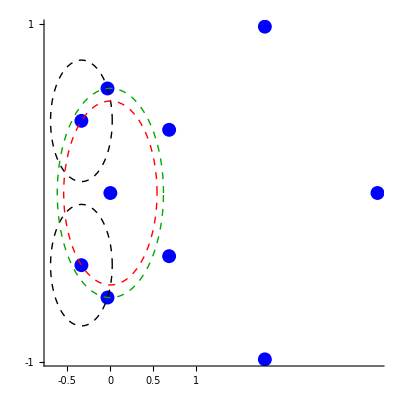

```mathematica
Abs[$theSingularList]//N
extCircleG={Dashed,Darker@Green,Circle[{0,0},Abs@$theSingularList[[4]]]};
Show[{singG,poleG,Graphics@{nearestDistancesG[[2;;3]],extCircleG,domain1G}},Axes->True,AspectRatio->1,PlotRange->1,Ticks->{{-1,-0.5,0,0.5,1},{-1,1}}]
```

```mathematica
baseSeries[[All,1;;5]]//N//MatrixForm
2 Pi I(-32)//N
```

(7.30828-12.1886/z-8.00796 z+8.93933 z^2-9.33542 z^3
(-20.7507-1.5052 ⅈ)+(8.97376-12.6197 ⅈ)/z+(20.5921+1.45196 ⅈ) z-(19.6135+0.869161 ⅈ) z^2+(18.3818+0.530416 ⅈ) z^3
(-20.7507+1.5052 ⅈ)+(8.97376+12.6197 ⅈ)/z+(20.5921-1.45196 ⅈ) z-(19.6135-0.869161 ⅈ) z^2+(18.3818-0.530416 ⅈ) z^3
7.59073+20.3603/z-9.63511 z+9.93022 z^2-9.8967 z^3)

0.-201.062 ⅈ

```mathematica
z0=1/2;
tStart=0;
tEnd=8Pi;
wVals=w/.NSolve[$theFunction==0/.z->z0,WorkingPrecision->25]
w0=wVals[[4]];
radius=z0;
integrationPath[t_]:=radius Exp[I t];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});
startTheta=0;

theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,tStart,tEnd},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->20];

int0=NIntegrate[theSol[t] D[integrationPath[t],t],{t,tStart,tEnd}]
```

{-70.10058676267339086895981-15.9275731099451271963011 ⅈ,-70.10058676267339086895981+15.9275731099451271963011 ⅈ,-4.637911883289151154333273,42.43908540863593289225288}

-5.11591×10^-13-201.062 ⅈ

### Plot singular points

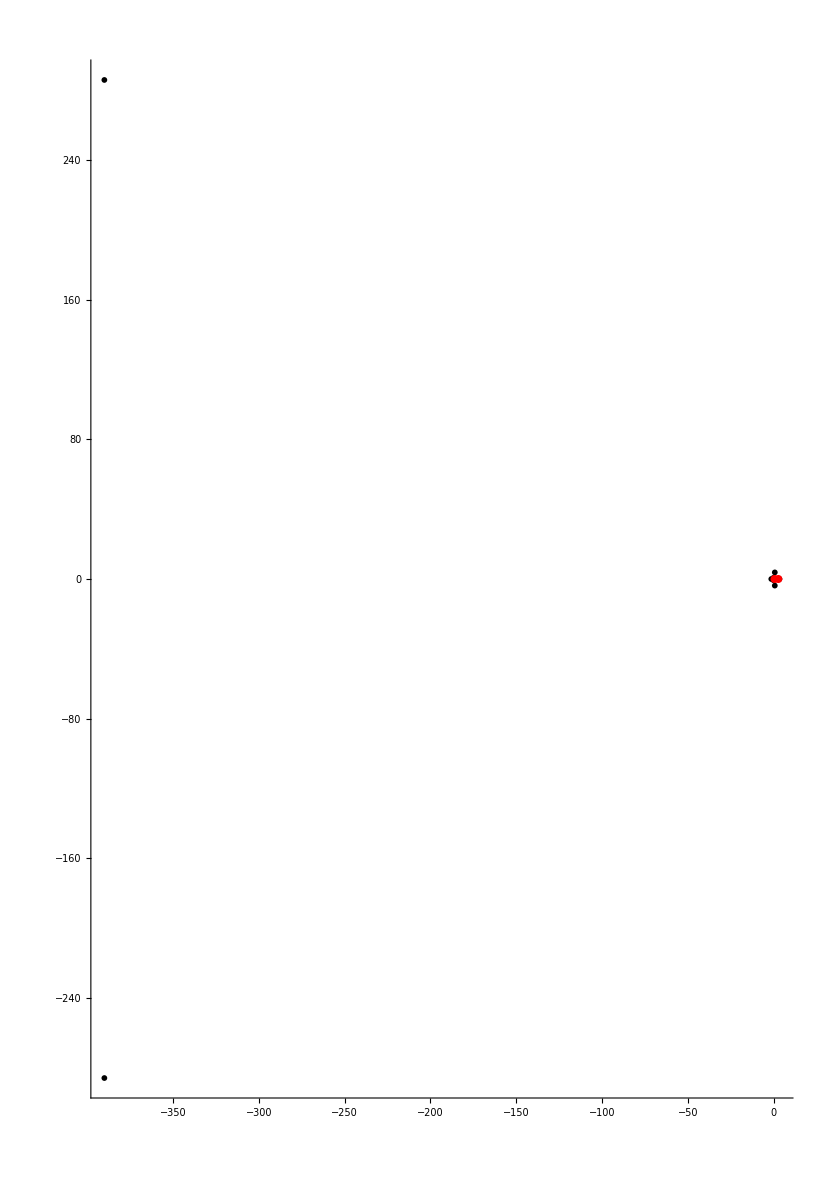

```mathematica
zeroG=Graphics@{PointSize[0.007],Blue,Point@(ReIm@#&/@ $theSingularList[[$zeroIndexes]])};
poleG=Graphics@{PointSize[0.007],Red,Point@(ReIm@#&/@ $theSingularList[[$poleIndexes]])};


singG=Graphics@{PointSize[0.005],Point@(ReIm@#&/@ $theSingularList)};
(*sPointG=Graphics@{PointSize[0.01],Red,Point@ReIm@$theSingularList[[402]]};*)
Show[{singG,zeroG,poleG},Axes->True]
```

## Section 3: Generate initial segments via Newton polygons

```mathematica
segmentMenu=Column[{(*Style["Pre-processing:",16,Bold,Black,Underlined],
Row[{Checkbox[Dynamic[$useReformedFunctionFlag]],Style[" Use Reformed function",Black,Bold]}],
Style["    "],*)
Style["Accuracy Parameters:",16,Bold,Black,Underlined],
Row[{Style["$acf: ",Bold,Black],Spacer[92], InputField[Dynamic@$acf,FieldSize->2],Spacer[25],Style["Accuracy zero comparison factor",Black,Bold]}],
Row[{Style["$rcf: ",Bold,Black],Spacer[92],InputField[Dynamic@$rcf,FieldSize->3],Spacer[11],Style["Residue zero comparison factor",Black,Bold]}],
Row[{Style["$pzf: ",Bold,Black],Spacer[92],InputField[Dynamic@$pzf,FieldSize->3],Spacer[11],Style["Polygonal zero comparison factor",Black,Bold]}],Row[{Style["$mcf: ",Bold,Black],Spacer[92],InputField[Dynamic@$mcf,FieldSize->2],Spacer[23],Style["Removable zero comparison factor",Black,Bold]}],
Row[{Style["$charRootFactor: ",Bold,Black], Spacer[13],InputField[Dynamic@$charRootFactor,FieldSize->3]}],
Style["  "],
Style["Diagnostics:",16,Bold,Black,Underlined],Row[{Checkbox[Dynamic[$getPoleDataFlag]],Spacer[3],Style["GetPoleData ",Black,Bold],Spacer[10],Checkbox[Dynamic[$getNewtonDataFlag]],Spacer[3],Style["GetNewtonData ",Black,Bold],Spacer[10],Checkbox[Dynamic[$getSegmentDataFlag]],Spacer[3],Style["GetSegmentData ",Black,Bold],Spacer[10]}],
Row[{Checkbox[Dynamic[$printCResidueKeyFlag]],Spacer[3],Style["ReportPolygonResidues",Bold,Black],Spacer[10],Checkbox[Dynamic[$savePolygonFigures]],Spacer[3],Style["SavePolygonsTo$polygonFigures",Bold,Black]}],
Row[{Checkbox[Dynamic[$saveCharDataFlag]],Spacer[3],Style["SaveCharData",Bold,Black],Spacer[10],
Checkbox[Dynamic[$printPolishRootFlag]],Spacer[3],Style["ReportPolishCharRoots",Bold,Black]
}],
Row[{Checkbox[Dynamic[$saveFIterateFlag]],Spacer[3],Style["SavePolygonIterates",Bold,Black],Spacer[10],Checkbox[Dynamic[$showNormalizedConstants]],Spacer[3],Style["ShowNormalizedConstants",Bold,Black]}],
Row[{Checkbox[Dynamic[$getCharRootFlag]],Spacer[3],Style["ReportCharRootData",Black,Bold],Spacer[15]
}]

},Frame->True,FrameStyle->Thick]
```

Accuracy Parameters:
$acf: Accuracy zero comparison factor
$rcf: Residue zero comparison factor
$pzf: Polygonal zero comparison factor
$mcf: Removable zero comparison factor
$charRootFactor: 
  
Diagnostics:
GetPoleData GetNewtonData GetSegmentData 
ReportPolygonResiduesSavePolygonsTo$polygonFigures
SaveCharDataReportPolishCharRoots
SavePolygonIteratesShowNormalizedConstants
ReportCharRootData

### Compute initial segments for a single singular point

```mathematica
(*
 enter test singular point index
*)
 testIndex=1;
$theSingularList[[testIndex]]//N
```

-0.461987-0.751542 ⅈ

f: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

f_n: (10.36+1.27 ⅈ+7.301 z+21.18 z^2+22.6 z^3+9.784 z^4-1.667 z^5)+(-3.316-0.01 ⅈ+1.786 z+1.954 z^2+0.731 z^3+0.2941 z^4+0.06667 z^5) w+(-3.207+1.96 ⅈ+7.204 z+9.486 z^2+7.971 z^3+4.411 z^4+1. z^5) w^2+(1.4) w^3+(11.41-0.64 ⅈ+6.572 z+14.63 z^2+16.87 z^3+10.12 z^4-2.5 z^5) w^4+(4.245+2.58 ⅈ+8.315 z+9.858 z^2+7.782 z^3+4.411 z^4+1. z^5) w^5

{0.} | (10.3632+1.26584 ⅈ)+(6.95768-2.2133 ⅈ) z-(15.5094-14.4187 ⅈ) z^2-(0.119414+22.596 ⅈ) z^3+(7.51656+6.26285 ⅈ) z^4-1.66667 z^5
{1.} | (-3.31603-0.0123778 ⅈ)-(0.962897-1.5039 ⅈ) z-(0.652629+1.84152 ⅈ) z^2+(0.565744+0.462937 ⅈ) z^3-(0.153996+0.250514 ⅈ) z^4+0.0666667 z^5
{2.} | (-3.20676+1.96442 ⅈ)-(3.29693+6.40474 ⅈ) z+(9.47981+0.334585 ⅈ) z^2-(3.91384-6.94405 ⅈ) z^3-(2.30993+3.75771 ⅈ) z^4+z^5
{3.} | 1.4
{4.} | (11.4057-0.637389 ⅈ)-(0.489573-6.55388 ⅈ) z-(12.8886+6.9147 ⅈ) z^2+(12.4805-11.3478 ⅈ) z^3+(3.77484+9.39428 ⅈ) z^4-2.5 z^5
{5.} | (4.24482+2.57827 ⅈ)-(4.56556+6.94928 ⅈ) z+(9.8421-0.567266 ⅈ) z^2-(3.51384-6.94405 ⅈ) z^3-(2.30993+3.75771 ⅈ) z^4+z^5

theF: (10.3632+1.26584 ⅈ)-(3.31603+0.0123778 ⅈ) w-(3.20676-1.96442 ⅈ) w^2+1.4 w^3+(11.4057-0.637389 ⅈ) w^4+(4.24482+2.57827 ⅈ) w^5+(6.95768-2.2133 ⅈ) z-(0.962897-1.5039 ⅈ) w z-(3.29693+6.40474 ⅈ) w^2 z-(0.489573-6.55388 ⅈ) w^4 z-(4.56556+6.94928 ⅈ) w^5 z-(15.5094-14.4187 ⅈ) z^2-(0.652629+1.84152 ⅈ) w z^2+(9.47981+0.334585 ⅈ) w^2 z^2-(12.8886+6.9147 ⅈ) w^4 z^2+(9.8421-0.567266 ⅈ) w^5 z^2-(0.119414+22.596 ⅈ) z^3+(0.565744+0.462937 ⅈ) w z^3-(3.91384-6.94405 ⅈ) w^2 z^3+(12.4805-11.3478 ⅈ) w^4 z^3-(3.51384-6.94405 ⅈ) w^5 z^3+(7.51656+6.26285 ⅈ) z^4-(0.153996+0.250514 ⅈ) w z^4-(2.30993+3.75771 ⅈ) w^2 z^4+(3.77484+9.39428 ⅈ) w^4 z^4-(2.30993+3.75771 ⅈ) w^5 z^4-1.66667 z^5+0.0666667 w z^5+w^2 z^5-2.5 w^4 z^5+w^5 z^5

wRules: ({0.}→(10.3632+1.26584 ⅈ)+(6.95768-2.2133 ⅈ) z-(15.5094-14.4187 ⅈ) z^2-(0.119414+22.596 ⅈ) z^3+(7.51656+6.26285 ⅈ) z^4-1.66667 z^5
{1.}→(-3.31603-0.0123778 ⅈ)-(0.962897-1.5039 ⅈ) z-(0.652629+1.84152 ⅈ) z^2+(0.565744+0.462937 ⅈ) z^3-(0.153996+0.250514 ⅈ) z^4+0.0666667 z^5
{2.}→(-3.20676+1.96442 ⅈ)-(3.29693+6.40474 ⅈ) z+(9.47981+0.334585 ⅈ) z^2-(3.91384-6.94405 ⅈ) z^3-(2.30993+3.75771 ⅈ) z^4+z^5
{3.}→1.4
{4.}→(11.4057-0.637389 ⅈ)-(0.489573-6.55388 ⅈ) z-(12.8886+6.9147 ⅈ) z^2+(12.4805-11.3478 ⅈ) z^3+(3.77484+9.39428 ⅈ) z^4-2.5 z^5
{5.}→(4.24482+2.57827 ⅈ)-(4.56556+6.94928 ⅈ) z+(9.8421-0.567266 ⅈ) z^2-(3.51384-6.94405 ⅈ) z^3-(2.30993+3.75771 ⅈ) z^4+z^5)

zRules: ({{0.}→10.3632+1.26584 ⅈ,{1.}→6.95768-2.2133 ⅈ,{2.}→-15.5094+14.4187 ⅈ,{3.}→-0.119414-22.596 ⅈ,{4.}→7.51656+6.26285 ⅈ,{5.}→-1.66667}
{{0.}→-3.31603-0.0123778 ⅈ,{1.}→-0.962897+1.5039 ⅈ,{2.}→-0.652629-1.84152 ⅈ,{3.}→0.565744+0.462937 ⅈ,{4.}→-0.153996-0.250514 ⅈ,{5.}→0.0666667}
{{0.}→-3.20676+1.96442 ⅈ,{1.}→-3.29693-6.40474 ⅈ,{2.}→9.47981+0.334585 ⅈ,{3.}→-3.91384+6.94405 ⅈ,{4.}→-2.30993-3.75771 ⅈ,{5.}→1.}
{{0.}→1.4}
{{0.}→11.4057-0.637389 ⅈ,{1.}→-0.489573+6.55388 ⅈ,{2.}→-12.8886-6.9147 ⅈ,{3.}→12.4805-11.3478 ⅈ,{4.}→3.77484+9.39428 ⅈ,{5.}→-2.5}
{{0.}→4.24482+2.57827 ⅈ,{1.}→-4.56556-6.94928 ⅈ,{2.}→9.8421-0.567266 ⅈ,{3.}→-3.51384+6.94405 ⅈ,{4.}→-2.30993-3.75771 ⅈ,{5.}→1.})

polygonPoints after MapThread: {{0.,0.,10.3632+1.26584 ⅈ},{1.,0.,-3.31603-0.0123778 ⅈ},{2.,0.,-3.20676+1.96442 ⅈ},{3.,0.,1.4},{4.,0.,11.4057-0.637389 ⅈ},{5.,0.,4.24482+2.57827 ⅈ}}

First hull plot

hullPoints: {{0.,0.,10.3632+1.26584 ⅈ},{1.,0.,-3.31603-0.0123778 ⅈ},{2.,0.,-3.20676+1.96442 ⅈ},{3.,0.,1.4},{4.,0.,11.4057-0.637389 ⅈ},{5.,0.,4.24482+2.57827 ⅈ}}

rotated points: {{0.,0.,10.3632+1.26584 ⅈ},{1.,0.,-3.31603-0.0123778 ⅈ},{2.,0.,-3.20676+1.96442 ⅈ},{3.,0.,1.4},{4.,0.,11.4057-0.637389 ⅈ},{5.,0.,4.24482+2.57827 ⅈ}}

Final polygon points G: {{0.,0.,10.3632+1.26584 ⅈ},{1.,0.,-3.31603-0.0123778 ⅈ},{2.,0.,-3.20676+1.96442 ⅈ},{3.,0.,1.4},{4.,0.,11.4057-0.637389 ⅈ},{5.,0.,4.24482+2.57827 ⅈ}}

Appending to lowLegPoints at k=1

Appending to lowLegPoints at k=1

Appending to lowLegPoints at k=1

«2 more identical outputs»

lowLegPoints: {{1.,2.,0.,0.},{2.,3.,0.,0.},{3.,4.,0.,0.},{4.,5.,0.,0.},{5.,6.,0.,0.}}

legArray: {{{1,2,0,0},{2,3,0,0},{3,4,0,0},{4,5,0,0},{5,6,0,0}}}

final leg point array: {{0,0},{1,0},{2,0},{3,0},{4,0},{5,0}}

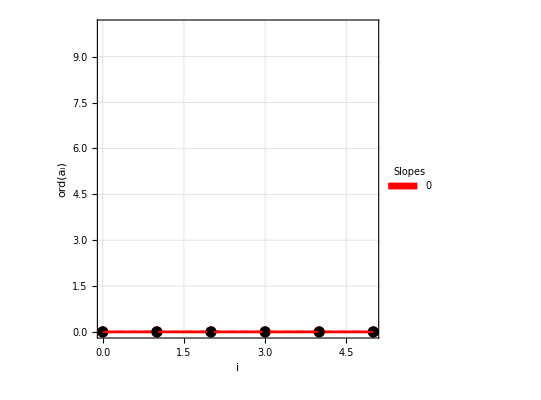

subReturn in getSegmentData: {{{{1.,2.,0.,0.},{2.,3.,0.,0.},{3.,4.,0.,0.},{4.,5.,0.,0.},{5.,6.,0.,0.}}},{{0.,0.,10.3632+1.26584 ⅈ},{1.,0.,-3.31603-0.0123778 ⅈ},{2.,0.,-3.20676+1.96442 ⅈ},{3.,0.,1.4},{4.,0.,11.4057-0.637389 ⅈ},{5.,0.,4.24482+2.57827 ⅈ}},{{0.,0.,10.3632+1.26584 ⅈ},{1.,0.,-3.31603-0.0123778 ⅈ},{2.,0.,-3.20676+1.96442 ⅈ},{3.,0.,1.4},{4.,0.,11.4057-0.637389 ⅈ},{5.,0.,4.24482+2.57827 ⅈ}}}

Entering polygon iteration 2

for root: -1.31689+1.05343 ⅈ

f_n: (-69.3-124.2 ⅈ z+198.8 z^2+194.8 z^3+121.2 z^4+30.54 z^5)+(-49.5+391.1 ⅈ z+564.4 z^2+554.4 z^3+340.3 z^4+83.76 z^5) w+(1.4+51.3 ⅈ+441.4 z+606.4 z^2+575.9 z^3+351.3 z^4+85.67 z^5) w^2+(42.-50.25 ⅈ+250.7 z+327.3 z^2+295.7 z^3+178.3 z^4+42.92 z^5) w^3+(-30.12+4.74 ⅈ+71.96 z+89.16 z^2+75.58 z^3+44.57 z^4+10.5 z^5) w^4+(4.245+2.58 ⅈ+8.315 z+9.858 z^2+7.782 z^3+4.411 z^4+1. z^5) w^5

{0.} | (-69.2877-124.191 ⅈ) z+(193.231+46.8729 ⅈ) z^2-(139.932-135.457 ⅈ) z^3-(41.3598+113.878 ⅈ) z^4+(30.4136+2.82389 ⅈ) z^5
{1.} | (-49.5108+391.07 ⅈ) z-(384.807+412.922 ⅈ) z^2+(545.511-99.0178 ⅈ) z^3-(97.1582-326.133 ⅈ) z^4-(60.1099+58.3348 ⅈ) z^5
{2.} | (1.38092+51.3004 ⅈ)+(307.699-316.504 ⅈ) z+(77.256+601.414 ⅈ) z^2-(519.256+248.988 ⅈ) z^3+(281.719-209.917 ⅈ) z^4+(12.6364+84.7329 ⅈ) z^5
{3.} | (42.0477-50.2536 ⅈ)-(246.356-46.6885 ⅈ) z+(142.751-294.496 ⅈ) z^2+(152.794+253.22 ⅈ) z^3-(178.152-7.04403 ⅈ) z^4+(19.4137-38.2792 ⅈ) z^5
{4.} | (-30.1242+4.74424 ⅈ)+(66.1749+28.2635 ⅈ) z-(74.7054-48.6601 ⅈ) z^2-(0.958188+75.5784 ⅈ) z^3+(38.7769+21.9699 ⅈ) z^4-(9.08444-5.26714 ⅈ) z^5
{5.} | (4.24482+2.57827 ⅈ)-(4.56556+6.94928 ⅈ) z+(9.8421-0.567266 ⅈ) z^2-(3.51384-6.94405 ⅈ) z^3-(2.30993+3.75771 ⅈ) z^4+1. z^5

theF: (1.38092+51.3004 ⅈ) w^2+(42.0477-50.2536 ⅈ) w^3-(30.1242-4.74424 ⅈ) w^4+(4.24482+2.57827 ⅈ) w^5-(69.2877+124.191 ⅈ) z-(49.5108-391.07 ⅈ) w z+(307.699-316.504 ⅈ) w^2 z-(246.356-46.6885 ⅈ) w^3 z+(66.1749+28.2635 ⅈ) w^4 z-(4.56556+6.94928 ⅈ) w^5 z+(193.231+46.8729 ⅈ) z^2-(384.807+412.922 ⅈ) w z^2+(77.256+601.414 ⅈ) w^2 z^2+(142.751-294.496 ⅈ) w^3 z^2-(74.7054-48.6601 ⅈ) w^4 z^2+(9.8421-0.567266 ⅈ) w^5 z^2-(139.932-135.457 ⅈ) z^3+(545.511-99.0178 ⅈ) w z^3-(519.256+248.988 ⅈ) w^2 z^3+(152.794+253.22 ⅈ) w^3 z^3-(0.958188+75.5784 ⅈ) w^4 z^3-(3.51384-6.94405 ⅈ) w^5 z^3-(41.3598+113.878 ⅈ) z^4-(97.1582-326.133 ⅈ) w z^4+(281.719-209.917 ⅈ) w^2 z^4-(178.152-7.04403 ⅈ) w^3 z^4+(38.7769+21.9699 ⅈ) w^4 z^4-(2.30993+3.75771 ⅈ) w^5 z^4+(30.4136+2.82389 ⅈ) z^5-(60.1099+58.3348 ⅈ) w z^5+(12.6364+84.7329 ⅈ) w^2 z^5+(19.4137-38.2792 ⅈ) w^3 z^5-(9.08444-5.26714 ⅈ) w^4 z^5+1. w^5 z^5

wRules: ({0.}→(-69.2877-124.191 ⅈ) z+(193.231+46.8729 ⅈ) z^2-(139.932-135.457 ⅈ) z^3-(41.3598+113.878 ⅈ) z^4+(30.4136+2.82389 ⅈ) z^5
{1.}→(-49.5108+391.07 ⅈ) z-(384.807+412.922 ⅈ) z^2+(545.511-99.0178 ⅈ) z^3-(97.1582-326.133 ⅈ) z^4-(60.1099+58.3348 ⅈ) z^5
{2.}→(1.38092+51.3004 ⅈ)+(307.699-316.504 ⅈ) z+(77.256+601.414 ⅈ) z^2-(519.256+248.988 ⅈ) z^3+(281.719-209.917 ⅈ) z^4+(12.6364+84.7329 ⅈ) z^5
{3.}→(42.0477-50.2536 ⅈ)-(246.356-46.6885 ⅈ) z+(142.751-294.496 ⅈ) z^2+(152.794+253.22 ⅈ) z^3-(178.152-7.04403 ⅈ) z^4+(19.4137-38.2792 ⅈ) z^5
{4.}→(-30.1242+4.74424 ⅈ)+(66.1749+28.2635 ⅈ) z-(74.7054-48.6601 ⅈ) z^2-(0.958188+75.5784 ⅈ) z^3+(38.7769+21.9699 ⅈ) z^4-(9.08444-5.26714 ⅈ) z^5
{5.}→(4.24482+2.57827 ⅈ)-(4.56556+6.94928 ⅈ) z+(9.8421-0.567266 ⅈ) z^2-(3.51384-6.94405 ⅈ) z^3-(2.30993+3.75771 ⅈ) z^4+1. z^5)

zRules: ({{1.}→-69.2877-124.191 ⅈ,{2.}→193.231+46.8729 ⅈ,{3.}→-139.932+135.457 ⅈ,{4.}→-41.3598-113.878 ⅈ,{5.}→30.4136+2.82389 ⅈ}
{{1.}→-49.5108+391.07 ⅈ,{2.}→-384.807-412.922 ⅈ,{3.}→545.511-99.0178 ⅈ,{4.}→-97.1582+326.133 ⅈ,{5.}→-60.1099-58.3348 ⅈ}
{{0.}→1.38092+51.3004 ⅈ,{1.}→307.699-316.504 ⅈ,{2.}→77.256+601.414 ⅈ,{3.}→-519.256-248.988 ⅈ,{4.}→281.719-209.917 ⅈ,{5.}→12.6364+84.7329 ⅈ}
{{0.}→42.0477-50.2536 ⅈ,{1.}→-246.356+46.6885 ⅈ,{2.}→142.751-294.496 ⅈ,{3.}→152.794+253.22 ⅈ,{4.}→-178.152+7.04403 ⅈ,{5.}→19.4137-38.2792 ⅈ}
{{0.}→-30.1242+4.74424 ⅈ,{1.}→66.1749+28.2635 ⅈ,{2.}→-74.7054+48.6601 ⅈ,{3.}→-0.958188-75.5784 ⅈ,{4.}→38.7769+21.9699 ⅈ,{5.}→-9.08444+5.26714 ⅈ}
{{0.}→4.24482+2.57827 ⅈ,{1.}→-4.56556-6.94928 ⅈ,{2.}→9.8421-0.567266 ⅈ,{3.}→-3.51384+6.94405 ⅈ,{4.}→-2.30993-3.75771 ⅈ,{5.}→1.})

polygonPoints after MapThread: {{0.,1.,-69.2877-124.191 ⅈ},{1.,1.,-49.5108+391.07 ⅈ},{2.,0.,1.38092+51.3004 ⅈ},{3.,0.,42.0477-50.2536 ⅈ},{4.,0.,-30.1242+4.74424 ⅈ},{5.,0.,4.24482+2.57827 ⅈ}}

First hull plot

hullPoints: {{5.,0.,4.24482+2.57827 ⅈ},{1.,1.,-49.5108+391.07 ⅈ},{0.,1.,-69.2877-124.191 ⅈ},{2.,0.,1.38092+51.3004 ⅈ},{3.,0.,42.0477-50.2536 ⅈ},{4.,0.,-30.1242+4.74424 ⅈ}}

rotated points: {{0.,1.,-69.2877-124.191 ⅈ},{2.,0.,1.38092+51.3004 ⅈ},{3.,0.,42.0477-50.2536 ⅈ},{4.,0.,-30.1242+4.74424 ⅈ},{5.,0.,4.24482+2.57827 ⅈ},{1.,1.,-49.5108+391.07 ⅈ}}

Final polygon points G: {{0.,1.,-69.2877-124.191 ⅈ},{2.,0.,1.38092+51.3004 ⅈ},{3.,0.,42.0477-50.2536 ⅈ},{4.,0.,-30.1242+4.74424 ⅈ},{5.,0.,4.24482+2.57827 ⅈ},{1.,1.,-49.5108+391.07 ⅈ}}

lowLegPoints: {{1.,2.,0.5,1.}}

legArray: {{{1,2,1/2,1}}}

final leg point array: {{0,1},{2,0}}

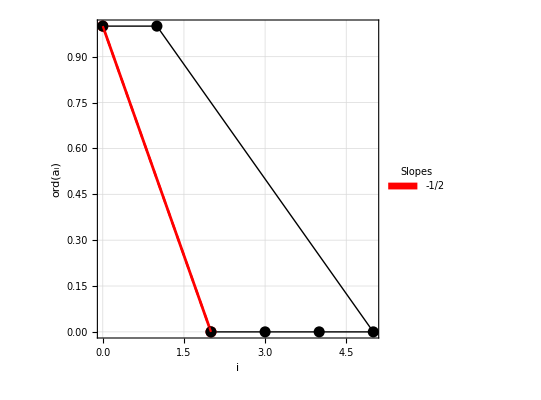

subReturn in getSegmentData: {{{{1.,2.,0.5,1.}}},{{0.,1.,-69.2877-124.191 ⅈ},{1.,1.,-49.5108+391.07 ⅈ},{2.,0.,1.38092+51.3004 ⅈ},{3.,0.,42.0477-50.2536 ⅈ},{4.,0.,-30.1242+4.74424 ⅈ},{5.,0.,4.24482+2.57827 ⅈ}},{{0.,1.,-69.2877-124.191 ⅈ},{2.,0.,1.38092+51.3004 ⅈ},{3.,0.,42.0477-50.2536 ⅈ},{4.,0.,-30.1242+4.74424 ⅈ},{5.,0.,4.24482+2.57827 ⅈ},{1.,1.,-49.5108+391.07 ⅈ}}}

Cycle list: {2,2,1,1,1}

All branch sheets accounted for!

{0.768634,Null}

Precision of $puiseuxSaveTable: 994.917

```mathematica
totalPoints=Length@$theSingularList;
PrintTemporary["     Analzing root: ",Dynamic@theIndex,"/",totalPoints];
$puiseuxSave={}; (* used by getNewtonData and getInitialSegments to save initial segment data *)
$polygonFigures={};
zeroIndexTally=0;
poleIndexTally=0;
$rootTally={};
(*
 variables to save Newton iteration data when SaveNewtonDataFlag is set
*)
$pHatSave={};
$pBarSave={};
$currentIteratedW={};
charEqnsSave={};
$fIterates={};

wTermsSave={};
cValSave={};
$multipleRootCheck={};
tempFunSave={};
$charDataSave={};
(*
 main routine to compute segments
*)
at=AbsoluteTiming[
$puiseuxSaveTable=getInitialSegments[$theFunction,testIndex];
]
(*
 confirm there is a singularity at each singular point, either a pole or ramified surface
*)
singularFlag=True;
poleIndex=0;
For[segNum=1,segNum<=Length@$puiseuxSaveTable,segNum++,
singIndex=$puiseuxSaveTable[[segNum,3]];
 cycleList=$puiseuxSaveTable[[segNum,2,All,3]];
(* first check if have all 1-cycles at this singular point, then must have at least one pole *)
If[Length@Cases[cycleList,x_/;x>1]==0 && !MemberQ[$poleIndexes,singIndex],
Print[Style["Found only 1-cycles with no pole at singular index: ",Red],singIndex];
singularFlag=False;
];
(*
 If all 1-cycle, confirm this singular point is a pole
*)
If[MemberQ[$poleIndexes,singIndex],
poleData=$puiseuxSaveTable[[segNum,2,All,{4,8}]];
netExpList=Flatten[FoldList[Plus,#1[[1]]]-#[[2]]& /@ poleData];
If[AnyTrue[netExpList,Negative],
(*Print[Style["Pole confirmed at singular index ",Red],Style[singIndex,Red]];*)
poleIndex++;
,
Print[Style["Did not find pole at expected singular point",Red,14],Style[singIndex,Red,14]];
];
];
];
If[poleIndex==Length@$poleIndexes && Length@$poleIndexes>1,
Print[Style["All poles confirmed",Red,Bold]];
];
If[Precision@$puiseuxSaveTable<900,
Print[Style["$puiseuxSaveTable precision<900. ",Red,Bold]];
];
If[zeroIndexTally==Length@$zeroIndexes && Length@$zeroIndexes>0,
Print[Style["All zero singular points with higher ramifications",Blue,Bold]];
];
If[poleIndexTally==Length@$poleIndexes && Length@$poleIndexes>0,
Print[Style["All pole singular points with higher ramifications",Red,Bold]];
];
Print["Precision of $puiseuxSaveTable: ",Precision@ $puiseuxSaveTable];
```

## Initialization

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"..","config.wl"}]]
 $HistoryLength=0;
<<ComputationalGeometry`
(*Needs["PlotLegends`"]*)
DistributeDefinitions[ConvexHull];
  $userDirectory="D:\\puiseuxSeries";
  $fNewton=Table[0,100];
  $λNewton=Table[0,100];
  $βNewton=Table[0,100];
  $cNewton=Table[0,100];
  $puiseuxSave={};
(*  $separationFactor=10;*)
  $workingPrecision=1000;
  $acf=20;
  $rcf=50;
  $charRootFactor=100;



  $useReformedFunctionFlag=True;
  $printCResidueKeyFlag=False;
  $maxPolymodalIteration=15;
  $showSegmentFlag=False;
  $stiffnessSwitchingFlag=True;
  $integrationDiagFlag1=False;
  $integrationDiagFlag2=False;
  $removeCSubResidueFactor=50;
  $mcf=50;
  $maxRootVerifyDifference=10^-50;
  $savePolygonFigures=False;
  $polygonFigures={};

  $saveCharDataFlag=False;
  $saveRootTallyListFlag=False;
  $saveNewtonIterationDataFlag=False;
  $tallyNewtonIterationIndexFlag=False;
  $getIterationNumbersFlag=False;
  $minimalWorkingAccuracy=100;
  $thetaV=Pi/6;
  $saveFIterateFlag=False;
  $pzf=100;
  $printPolishRootFlag=False;




  $getSegmentDataFlag=True;
  $getCharRootFlag=False;
  $getPoleDataFlag=False;
  $getNewtonDataFlag=False;
  $minCharRootAccuracy=100;

DistributeDefinitions[  z,
  w,
  c,
  s,
  $workingPrecision,
  $separationFactor];

 file::fileExists="File `1` exists.";

$showNormalizedConstants=False;
$minNSolvePrecision=100;
```

### getySingularRange

```mathematica
getSingularRange[y_,z_]:=Module[{return},
If[y===-1,
return=Range[1,Length@$theSingularList];
,
If[Length@y>0,
return=y;
,
If[z==-1,
return={y};
,
return=Range[y,z];
];
];
];
return
];
```

### getSingularPoints (new)

```mathematica
(*
 rNormArray is 1/2 distance to either nearest singular point or outer annular value
*)
(*
 $minRadiusArray is 1/3 distance to either nearest singular point or outer annular value
*)
  getSingularPoints[theFunction_,workingPrecision_:1000,diagFlag_:False]:=Module[{i,theSingularSet,theSingularList,wExpList,poleFuntion,pExp,poleIndexes,poleFunction,polePositions,singularReport,theArgList,nearestSing,nearestDistArray,minRadiusArray,thePoleList,theReturn,singAccuracy,poleAccuracy,thePoleSet,poleF,res,at1,at2,zeroIndexes,originCheck,rNormArray,singularPerimeters,singularNorms,singularDistances
},
If[workingPrecision<1000,
Print[Style["WorkingPrecision must be greater than or equal to 1000",Red]];
theReturn={-1,-1,-1,-1,-1,-1,-1};
,
If[!strictPolynomialQ[theFunction,{z,w}],
Print[Style["Function not a strict polynomial with rational coefficients in z and w",Red]];
theReturn={-1,-1,-1,-1,-1};
,
If[!IrreduciblePolynomialQ[theFunction],
{
Print[Style["Function is reducible:  ",Red],Style[Factor[$theFunction],Red]];
theReturn={-1,-1,-1,-1,-1,-1,-1};
}
,
at1=AbsoluteTiming[
res=Resultant[theFunction,D[theFunction,w],w];
];
If[diagFlag,
Print["Time to compute resultant: ",at1[[1]]];
];
at2=AbsoluteTiming[
theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->workingPrecision],Abs@#1<= Abs@#2&];
];
If[diagFlag,
Print["Time to compute singular points: ",at2[[1]]];
];
singAccuracy=Floor@Accuracy@theSingularSet;
If[Length@theSingularSet==0 || singAccuracy<900,
Print[Style["No singular points found or sing accuracy<900",Red]];
theReturn={-1,-1,-1,-1,-1,-1,-1};
,
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(singAccuracy-$acf)&];
(*
 now get zero points a_0(z)=0 when either $a_1(z)=0 or $a_0=a_1
*)
zeroIndexes=getZeroIndexes[theFunction,theSingularList,False];
(*
get poles
*)
poleIndexes=getPoles[theFunction,theSingularList,False];

(*
 compute minArray of integration region around each singular point if total > 1 
*)
If[Length@theSingularList>1,
nearestSing=(NearestTo[#1,2][theSingularList]&/@ theSingularList)[[All,2]];
nearestDistArray=MapThread[Abs[#1-#2]&,{theSingularList,nearestSing}];
minRadiusArray=MapThread[1/3Abs[#1-#2]&,{theSingularList,nearestSing}];
rNormArray=MapThread[1/2Abs[#1-#2]&,{theSingularList,nearestSing}];

singularPerimeters=minRadiusArray;
singularNorms=rNormArray;
singularDistances=nearestDistArray;





For[i=1,i<=Length@nearestDistArray,i++,
If[nearestDistArray[[i]]>10,
nearestDistArray[[i]]=10;
minRadiusArray[[i]]=3;
rNormArray[[i]]=5;
];
];
,
Print[Style["Found only one singular point!",Red,Bold]];
minRadiusArray={2};
nearestDistArray={4};
rNormArray={2}
];
theReturn={theSingularList,poleIndexes,minRadiusArray,res,zeroIndexes,nearestDistArray,rNormArray};
If[diagFlag,
Print["Total singular points: ",Length@theSingularList];
Print["Precision of singular points: ",Precision@theSingularList];
Print["Total poles: ",Length@poleIndexes];
Print[Style["Pole indexes: ",Red],Style[poleIndexes,Red]];
Print["Total zero points: ",Length@zeroIndexes];
Print[Style["Zero indexes: ",Blue],Style[zeroIndexes,Blue]];
Print["Min singular perimeter: ",Min@minRadiusArray//N];
If[Length@theSingularList>1,
Print["Smallest singular points: ",theSingularList[[1;;2]]//N];
,
Print["Singular point: ",theSingularList[[1]]//N];
];
];
];
];
];
];

theReturn
];
```

### getSingularPointsOld

```mathematica
getSingularPointsOld[$theFunction_,workingPrecision_:1000,diagFlag_:False]:=Module[{i,theSingularSet,$theSingularList,wExpList,poleFuntion,pExp,$poleIndexes,poleFunction,polePositions,singularReport,theArgList,nearestSing,nearestDist,$minRadiusArray,thePoleList,theReturn,singAccuracy,poleAccuracy,thePoleSet,poleF,res,at1,at2,$zeroIndexes,originCheck
},
If[workingPrecision<1000,
Print[Style["WorkingPrecision must be greater than or equal to 1000",Red]];
theReturn={-1,-1,-1,-1,-1};
,
If[!strictPolynomialQ[$theFunction,{z,w}],
Print[Style["Function not a strict polynomial with rational coefficients in z and w",Red]];
theReturn={-1,-1,-1,-1,-1};
,
If[!IrreduciblePolynomialQ[$theFunction],
{
Print[Style["Function is reducible:  ",Red],Style[Factor[$theFunction],Red]];
theReturn={-1,-1,-1,-1,-1};
}
,
at1=AbsoluteTiming[
res=Resultant[$theFunction,D[$theFunction,w],w];
];
If[diagFlag,
Print["Time to compute resultant: ",at1[[1]]];
];

at2=AbsoluteTiming[
theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->workingPrecision],Abs@#1<= Abs@#2&];
];
If[diagFlag,
Print["Time to compute singular points: ",at2[[1]]];
];
singAccuracy=Floor@Accuracy@theSingularSet;
If[Length@theSingularSet==0 || singAccuracy<900,
Print[Style["No singular points found or sing accuracy<900",Red]];
theReturn={-1,-1,-1,-1,-1};
,
$theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(singAccuracy-$acf)&];
(*
 now get zero points a_0(z)=0 when either $a_1(z)=0 or $a_0=a_1
*)
$zeroIndexes=getZeroIndexes[$theFunction,$theSingularList,False];
(*
get poles
*)
$poleIndexes=getPoles[$theFunction,$theSingularList,False];

(*
 compute minArray of integration region around each singular point if total > 1 
*)
If[Length@$theSingularList>1,
nearestSing=(NearestTo[#1,2][$theSingularList]&/@ $theSingularList)[[All,2]];
nearestDist=MapThread[1/3Abs[#1-#2]&,{$theSingularList,nearestSing}];
(*nearestSingDist=MapThread[Abs[#1-#2]&,{$theSingularList,nearestSing}];*)
For[i=1,i<=Length@nearestDist,i++,
If[nearestDist[[i]]>10,
nearestDist[[i]]=10;
];
];
$minRadiusArray=nearestDist;
,
Print[Style["Found only one singular point!",Red,Bold]];
$minRadiusArray=∞;
];
theReturn={$theSingularList,$poleIndexes,$minRadiusArray,res,$zeroIndexes};
If[diagFlag,
Print["Total singular points: ",Length@$theSingularList];
Print["Precision of singular points: ",Precision@$theSingularList];
Print["Total poles: ",Length@$poleIndexes];
Print[Style["Pole indexes: ",Red],Style[$poleIndexes,Red]];
Print["Total zero points: ",Length@$zeroIndexes];
Print[Style["Zero indexes: ",Blue],Style[$zeroIndexes,Blue]];
Print["Min singular perimeter: ",Min@$minRadiusArray//N];
If[Length@$theSingularList>1,
Print["Smallest singular points: ",$theSingularList[[1;;2]]//N];
,
Print["Singular point: ",$theSingularList[[1]]//N];
];
];
];
];
];
];

theReturn
];
```

### polyForm(poly,var)

```mathematica
polyForm[poly_,var_]:=Module[{coeffs=CoefficientRules[poly,var]//Sort},Interpretation[Row[Table[Row[{"(",coeff[[2]],")",var^coeff[[1,1]]/.1->""}],{coeff,coeffs}],"+"],poly]]
```

### getInitialSegments

```mathematica
getInitialSegments[$theFunction_,start_:-1,end_:-1]:=Module[{$puiseuxSaveTable,mIndex,normalExp,currentmu,theK,baseData,cycleList,posArray,sheetFlag,minExp,residueFactor,reformedFunctionIndexTable,reformedFunction,reformedFunctionIndex,reformedFunctionTableIndex,singAccuracy,segList,wCoef,tableData,cResidueFactor,aTerms,aRules,cTable,zRules},

segList=getSingularRange[start,end];
sheetFlag=True;
singAccuracy=Floor@Accuracy@$theSingularList;
$puiseuxSaveTable=Table[

theIndex=mIndex;
$puiseuxSave={};
minExp=getMinValidExp[mIndex];
(*cResidueFactor=$removeCSubResidueFactor;
If[minExp<-50,
cResidueFactor=-minExp+$removeCSubResidueFactor;
];
If[cResidueFactor>8/10 singAccuracy,
Print[Style["cResidueFactor is greater than 8/10 of the singular accuracy!",Red,14,Bold]];
Abort[];
];*)
If[$printCResidueKeyFlag,
Print["min exponent: ",N[minExp,10]];
];
(*
 new routine here
*)
If[$useReformedFunctionFlag,
If[MemberQ[reformedFunctionTable[[All,1]],mIndex],
(*If[$getInitialSegmentFlag,
Print[Style["Using reformed function",Blue,Bold]];
];*)
reformedFunctionTableIndex=Position[reformedFunctionTable[[All,1]],x_/;x==mIndex];
If[Length@reformedFunctionTableIndex!=1,
Print[Style["Error finding position in reformedFunctiontTable",Red]];
Abort[];
];
reformedFunctionIndex=reformedFunctionTableIndex[[1,1]];
reformedFunction=reformedFunctionTable[[reformedFunctionIndex,2]];
If[MemberQ[$poleIndexes,mIndex],
(* If this is a pole, need to normalize it *)
{$fNewton[[1]],normalExp,currentmu}=convertToNormalForm[Expand[reformedFunction/.s->$theSingularList[[mIndex]]]];
If[$getPoleDataFlag,
Print["$theFunction= ",aForm[$theFunction]];
Print["transformed function: ",aForm[ Expand[reformedFunction/.s->$theSingularList[[mIndex]]]//N]];
Print["Transformed function f_t initial terms for a pole: "];
wCoef=CoefficientRules[ Expand[reformedFunction/.s->$theSingularList[[mIndex]]],w,"NegativeLexicographic"]//N;
cTable=Table[
zRules=CoefficientRules[wCoef[[i,2]],z,"NegativeLexicographic"];
{wCoef[[i,1]],FromCoefficientRules[{zRules[[1]]},z]},
{i,1,Length@wCoef}
];
Print[Grid[cTable,Alignment->Left]];

Print["μ: ",currentmu];
Print["λ: ",normalExp];

wCoef=CoefficientRules[ $fNewton[[1]],w,"NegativeLexicographic"]//N;
cTable=Table[
zRules=CoefficientRules[wCoef[[i,2]],z,"NegativeLexicographic"];
{wCoef[[i,1]],FromCoefficientRules[{zRules[[1]]},z]},
{i,1,Length@wCoef}
];
Print["normal form of f: ",aForm[$fNewton[[1]]]];
Print["Normal function f_n initial terms for a pole: "];
Print["Coefficients of normal form: "];
Print[Grid[cTable,Alignment->Left]];

];
,
(* not a pole *)
normalExp=0;
currentmu=0;
$fNewton[[1]]=reformedFunction/.s->$theSingularList[[mIndex]];
];
,
(* mIndex is not in the reformed list *)
normalExp=0;
currentmu=0;
$fNewton[[1]]=Expand[$theFunction/.z->z+$theSingularList[[mIndex]]];
];
,
(* use un-reformed function *)

{$fNewton[[1]],normalExp,currentmu}=convertToNormalForm[Expand[$theFunction/.z->z+$theSingularList[[mIndex]]]];
];

theK=1;
If[!IrreduciblePolynomialQ[$fNewton[[1]]],
{
Print["index: ",mIndex];
Print[Style["Function is reducible",Red]];
Abort[];
}
,
getNewtonData[$fNewton[[1]],1,normalExp];
];
(*If[$getInitialSegmentFlag,
Print["function passed to get seg: ",$fNewton[[1]]//N];
];*)
 baseData=MapThread[{#2,#1}&,{Range[Length@$puiseuxSave],$puiseuxSave[[All,3]]}];
(*
now check if total sheets equal to degree of function
*)
If[Length@$puiseuxSave!=functionDegree,
Print[Style["getNewtonData found  ",Red],Style[Length@$puiseuxSave,Red],Style[" sheets out of ",Red],Style[functionDegree,Red]," at singular index ",mIndex];
sheetFlag=False;
];
(*
 check for non-minimal ramification
*)
cycleList=$puiseuxSave[[All,3]];
If[$getSegmentDataFlag,
Print["Cycle list: ",cycleList];
];
posArray=Position[cycleList,x_/;x>2];
If[Length@posArray>0,
If[MemberQ[$poleIndexes,mIndex],
poleIndexTally++;
Print[Style["Found higher ramifications for pole index ",Red],Style[mIndex,Red],": ",cycleList];
,
If[MemberQ[$zeroIndexes,mIndex],
zeroIndexTally++;
Print[Style["Found higher ramifications for zero index ",Blue],Style[mIndex,Blue],": ",cycleList];
,
Print["Found higher ramifications for singular index ",mIndex,": ",cycleList];
];
];
];

{baseData,$puiseuxSave,mIndex,$fNewton[[1]],normalExp,currentmu},
{mIndex,segList}
];

If[sheetFlag==True,
Print[Style["All branch sheets accounted for!",Bold,Black]];
,
Print[Style["Branch sheet errors!",Bold,Red]];
];
$puiseuxSaveTable
];
```

### getInitialSegmentsAtInfinity

```mathematica
getInitialSegmentsAtInfinity[$theFunction_]:=Module[{$puiseuxSaveTable,mIndex,normalExp,currentmu,theK,baseData,cycleList,posArray,sheetFlag,minExp,residueFactor,reformedFunctionIndexTable,reformedFunction,reformedFunctionIndex,reformedFunctionTableIndex,singAccuracy,segList,wCoef,tableData,cResidueFactor,aTerms,aRules,cTable,zRules},

segList={1};
sheetFlag=True;
singAccuracy=900;
$puiseuxSaveTable=Table[

theIndex=mIndex;
$puiseuxSave={};
minExp=getMinValidExp[mIndex];
cResidueFactor=$removeCSubResidueFactor;
If[minExp<-50,
cResidueFactor=-minExp+$removeCSubResidueFactor;
];
If[cResidueFactor>8/10 singAccuracy,
Print[Style["cResidueFactor is greater than 8/10 of the singular accuracy!",Red,14,Bold]];
Abort[];
];
If[$printCResidueKeyFlag,
Print["Smallest exponentr after z->z+s_p: ",minExp,"c-form residue factor: ",-cResidueFactor," for index ",mIndex];
];
(*
 new routine here
*)
If[$useReformedFunctionFlag,
If[MemberQ[reformedFunctionTable[[All,1]],mIndex],
(*If[$getInitialSegmentFlag,
Print[Style["Using reformed function",Blue,Bold]];
];*)
reformedFunctionTableIndex=Position[reformedFunctionTable[[All,1]],x_/;x==mIndex];
If[Length@reformedFunctionTableIndex!=1,
Print[Style["Error finding position in reformedFunctiontTable",Red]];
Abort[];
];
reformedFunctionIndex=reformedFunctionTableIndex[[1,1]];
reformedFunction=reformedFunctionTable[[reformedFunctionIndex,2]];
If[MemberQ[$poleIndexes,mIndex],
(* If this is a pole, need to normalize it *)
{$fNewton[[1]],normalExp,currentmu}=convertToNormalForm[Expand[reformedFunction/.s->0]];
If[$getPoleDataFlag,
Print["$theFunction= ",aForm[$theFunction]];
Print["Transformed function f_t initial terms for a pole: "];
wCoef=CoefficientRules[ Expand[reformedFunction/.s->0],w,"NegativeLexicographic"]//N;
cTable=Table[
zRules=CoefficientRules[wCoef[[i,2]],z,"NegativeLexicographic"];
{wCoef[[i,1]],FromCoefficientRules[{zRules[[1]]},z]},
{i,1,Length@wCoef}
];
Print[Grid[cTable,Alignment->Left]];

Print["μ: ",currentmu];
Print["λ: ",normalExp];
wCoef=CoefficientRules[ $fNewton[[1]],w,"NegativeLexicographic"]//N;
cTable=Table[
zRules=CoefficientRules[wCoef[[i,2]],z,"NegativeLexicographic"];
{wCoef[[i,1]],FromCoefficientRules[{zRules[[1]]},z]},
{i,1,Length@wCoef}
];
Print["Normal function f_n initial terms for a pole: "];
Print[Grid[cTable,Alignment->Left]];
];
,
(* not a pole *)
normalExp=0;
currentmu=0;
$fNewton[[1]]=reformedFunction/.s->0;
];
,
(* mIndex is not in the reformed list *)
normalExp=0;
currentmu=0;
$fNewton[[1]]=Expand[$theFunction];
];
,
(* use un-reformed function *)

{$fNewton[[1]],normalExp,currentmu}=convertToNormalForm[Expand[$theFunction]];
];

theK=1;
If[!IrreduciblePolynomialQ[$fNewton[[1]]],
{
Print["index: ",mIndex];
Print[Style["Function is reducible",Red]];
Abort[];
}
,
getNewtonData[$fNewton[[1]],1,normalExp,cResidueFactor];
];
(*If[$getInitialSegmentFlag,
Print["function passed to get seg: ",$fNewton[[1]]//N];
];*)
 baseData=MapThread[{#2,#1}&,{Range[Length@$puiseuxSave],$puiseuxSave[[All,3]]}];
(*
now check if total sheets equal to degree of function
*)
If[Length@$puiseuxSave!=functionDegree,
Print[Style["getNewtonData found  ",Red],Style[Length@$puiseuxSave,Red],Style[" sheets out of ",Red],Style[functionDegree,Red]," at singular index ",mIndex];
sheetFlag=False;
];
(*
 check for non-minimal ramification
*)
cycleList=$puiseuxSave[[All,3]];
If[$getSegmentDataFlag,
Print["Cycle list: ",cycleList];
];
posArray=Position[cycleList,x_/;x>2];
If[Length@posArray>0,
If[MemberQ[$poleIndexes,mIndex],
poleIndexTally++;
Print[Style["Found higher ramifications for pole index ",Red],Style[mIndex,Red],": ",cycleList];
,
If[MemberQ[$zeroIndexes,mIndex],
zeroIndexTally++;
Print[Style["Found higher ramifications for zero index ",Blue],Style[mIndex,Blue],": ",cycleList];
,
Print["Found higher ramifications for singular index ",mIndex,": ",cycleList];
];
];
];

{baseData,$puiseuxSave,mIndex,$fNewton[[1]],normalExp,currentmu},
{mIndex,segList}
];

If[sheetFlag==True,
Print[Style["All branch sheets accounted for!",Bold,Black]];
,
Print[Style["Branch sheet errors!",Bold,Red]];
];
$puiseuxSaveTable
];
```

### getNormalVals using Max[ord(an)-ord(ai)/(n-1)]

```mathematica
getNormalVals[$theFunction_]:=Module[{wExp,functionDegree,wCoef,orderList,theLambda,theMu,lambdaList,theReturn},
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;
wCoef=CoefficientRules[$theFunction,w,"NegativeLexicographic"];
If[Length@wCoef<3,
Print[Style["Function needs more than three terms to use getNormalVals!",Red,Bold]];
theReturn={-1,-1};
,
orderList={#[[1,1]],Exponent[#[[2]],z,List]//First}&/@ wCoef;
(*Print["orderList: ",orderList[[2;;-2]]];*)
lambdaList=((orderList[[-1,2]]-#[[2]])/(orderList[[-1,1]]-#[[1]])&/@ orderList[[2;;-2]]);
(*Print["Lambda list: ",lambdaList];*)
theLambda=Max[Ceiling@lambdaList];
theMu=theLambda functionDegree-orderList[[-1,2]];
theReturn={theLambda,theMu};
];
theReturn
]
```

### ConvertToNormalForm

```mathematica
convertToNormalForm[theF_]:=Module[{wRules,wKeys,zRules,theOrders,positiveOrders,fDegree,normalEqn,normalConstraints,eqnA,i,minData,currentmu,mylambda,thepoly,μ,λ,lVal,mVal},

 wRules=CoefficientRules[theF,w,"NegativeLexicographic"];
wKeys=wRules[[All,1]];
zRules={#[[1,1]],CoefficientRules[#[[2]],z,"NegativeLexicographic"]}&/@ wRules;
theOrders={#[[1]],#[[2,1,1,1]]}&/@ zRules;
positiveOrders=Select[theOrders,#[[1]]>0&];
fDegree=Max@Exponent[theF,w,List];
normalEqn=μ+positiveOrders[[-1,2]]==fDegree λ;
normalConstraints=Table[
eqnA=μ+positiveOrders[[i,2]]>=positiveOrders[[i,1]] λ;
eqnA,
{i,1,Length[positiveOrders]-1}
];

minData=Minimize[{λ,normalEqn &&(And@@normalConstraints)&& Element[{μ,λ},PositiveIntegers]},{μ,λ}];
{currentmu,mylambda}={μ,λ}/.minData[[2]];
thepoly=Expand[z^currentmu(theF/.w->w/(z^mylambda))];
If[$showNormalizedConstants,
(*
 now check against getNormalVals
*)
Print["the eta: ",mylambda];
Print["the mu: ",currentmu];
(*{lVal,mVal}=getNormalVals[theF];
Print["Normal vals from getNormalVals:"];
Print["mu: ",lVal];
Print["eta:     ",mVal];*)
];
{thepoly,mylambda,currentmu}
];

convertToNormalForm2[theF_]:=Module[{wRules,wKeys,zRules,theOrders,positiveOrders,fDegree,normalEqn,normalConstraints,eqnA,i,minData,currentmu,mylambda,thepoly,μ,λ,lVal,mVal},

 wRules=CoefficientRules[theF,w,"NegativeLexicographic"];
wKeys=wRules[[All,1]];
zRules={#[[1,1]],CoefficientRules[#[[2]],z,"NegativeLexicographic"]}&/@ wRules;
theOrders={#[[1]],#[[2,1,1,1]]}&/@ zRules;
positiveOrders=Select[theOrders,#[[1]]>0&];
fDegree=Max@Exponent[theF,w,List];
normalEqn=μ+positiveOrders[[-1,2]]==fDegree λ;
normalConstraints=Table[
eqnA=μ+positiveOrders[[i,2]]>=positiveOrders[[i,1]] λ;
eqnA,
{i,1,Length[positiveOrders]-1}
];

minData=Minimize[{λ,normalEqn &&(And@@normalConstraints)&& Element[{μ,λ},PositiveIntegers]},{μ,λ}];
{currentmu,mylambda}={μ,λ}/.minData[[2]];
(*Print["the eta: ",mylambda];
Print["the mu: ",currentmu];*)
thepoly=Expand[z^currentmu(theF/.w->w/(z^mylambda))];
{thepoly,mylambda,currentmu}
];
```

### getTheOrder(p)

```mathematica
getTheOrder[p_]:=Module[{clist,theorder,j},
clist=CoefficientList[p,z];
theorder=∞;
If[Length[clist]!=0,
{
j=0;
While[clist[[j+1]]==0 && (j+1)≤ Length[clist],
{
j++;
}
];
theorder=j;
}
,
theorder=∞;
];
theorder
];
```

### getNewtonData

```mathematica
getNewtonData[thef_,theK_,normalExp_]:=Module[{j,rootnum,theftemp,theclist,expList,minVals,lcpsave,myPoints,pgp,sg,newtonLeg,mylines,maxx,maxy,slopeInterceptList,theCEquations,theRootTally,rootstatus,theSegmentData,mysegments,currentRootTally,currentSegment,currentRootList,theT,theD,mycurrentw,multinum,myS,charRoots,theLegArray,thePolygonPoints,theRotatedPoints,hullIndexes,cZeroList,cRemovalF},

theftemp=thef;

theclist=CoefficientList[theftemp,w];
expList=Exponent[theclist,z,Min];
minVals=MapThread[Coefficient[#1,z,#2]&,{theclist,expList}];
 {theLegArray,thePolygonPoints,theRotatedPoints}=getSegmentData[Expand@thef,theK];
If[$getNewtonDataFlag,
Print["theLegArray: ",theLegArray//N];
Print["thePolygonPoints: ",thePolygonPoints//N];
];


If[Length[theLegArray]>0,
{
{slopeInterceptList,theRootTally}=getCharRoots[theLegArray,thePolygonPoints,theRotatedPoints];
If[$getNewtonDataFlag,
Print["slopeInterceptList: ",slopeInterceptList//N];
Print["root tally: ",theRootTally//N];
];

(* keep copy of theRootTally to detect multiple factors of a finite series *)
currentRootTally=theRootTally;
theSegmentData=MapThread[{#1,#2}&,{slopeInterceptList,theRootTally}];
Clear[x];


mysegments=Range[Length[theSegmentData]];

 Do[ 
{
$fNewton[[theK]]=theftemp;
currentSegment=theSegmentData[[segmentnum]];
currentRootList=currentSegment[[2]];
If[$getNewtonDataFlag,
Print["current root list size: ",Length@currentRootList];
];

{$λNewton[[theK]],$βNewton[[theK]]}=currentSegment[[1]];
For[rootnum=1,rootnum≤Length[currentRootList],rootnum++,
$cNewton[[theK]]=currentRootList[[rootnum,1]];

If[currentRootList[[rootnum,2]]≠1,
(* generate next polygon leg *)
{

If[$getNewtonDataFlag,
Print["$fNewton[[theK+1]] before remove residues: ",N[polyForm[1/z^($βNewton[[theK]])$fNewton[[theK]]/.w->z^($λNewton[[theK]])($cNewton[[theK]]+w),w],10]];
];
{cZeroList,cRemovalF}=identifyPolygonZeros[1/z^($βNewton[[theK]])$fNewton[[theK]]/.w->z^($λNewton[[theK]])(c+w),$cNewton[[theK]]];

$fNewton[[theK+1]]=cRemovalF;

If[$getNewtonDataFlag,
Print["$fNewton[[theK+1]] after removeCResidues: ",polyForm[N[$fNewton[[theK+1]],10],w]];
];

If[(theK+1)>1 && $getSegmentDataFlag,
Print[Style["Entering polygon iteration ",Purple,Bold,20,Underlined],Style[theK+1,Purple,Bold,20]];
Print["  for root: ",$cNewton[[theK]]//N];
];
getNewtonData[$fNewton[[theK+1]],theK+1,normalExp];

}
,

{
If[$getNewtonDataFlag,
Print[Style["Encountered simple roots: ",Red,14],currentRootList[[rootnum]]//N];
];
If[$getNewtonDataFlag,
Print["Adding segment term for root ",currentRootList[[rootnum,1]]//N];
];
theT=theK;
theD=getCommonDenom[theK,$λNewton];

mycurrentw=currentRootList[[rootnum,1]];
charRoots=Table[$cNewton[[i]],{i,1,theK}];

AppendTo[$puiseuxSave,{theK,charRoots,theD,Table[$λNewton[[j]],{j,1,theK}],$fNewton[[theT]],$βNewton[[theT]],mycurrentw,normalExp}];

}
];
];
},
{segmentnum,mysegments}
];
}
];
];
```

### getNewRootDifference[rootarray]

```mathematica
getNewRootDifferenceOld[ra_]:=Module[{roots,i,j,k,arrays,mydif,roottally,i2,j2},

arrays=Table[{},{Length[ra]}];
For[k=1,k≤Length[ra],k++, (* root list *)
arrays[[k]]=Table[0,{Length[ra[[k]]]+1},{Length[ra[[k]]]+1}];
For[h=1,h≤Length[ra[[k]]],h++,
arrays[[k,1,h+1]]=Style[h,Bold];
arrays[[k,h+1,1]]=Style[h,Bold];
];
arrays[[k,1,1]]=" ";
For[i2=2,i2≤Length[ra[[k]]]+1,i2++,
i=i2-1;
For[j2=2,j2≤Length[ra[[k]]]+1,j2++,
{
j=j2-1;
If[i==j,
arrays[[k,i2,j2]]=Style[1,12];
,
If[IntegerPart[Precision[Abs[ra[[k,i]]-ra[[k,j]]]]]≤0,
{
arrays[[k,i2,j2]]=Style[N[Abs[ra[[k,i]]-ra[[k,j]]],4],14,Red,Bold];
}
,
{
If[Abs[ra[[k,i]]-ra[[k,j]]]≥ 10^(-100),
arrays[[k,i2,j2]]=Style[N[Abs[ra[[k,i]]-ra[[k,j]]],4],14];
,
arrays[[k,i2,j2]]=Style[N[Abs[ra[[k,i]]-ra[[k,j]]],4],14,Blue];
Print[Style["Found insufficiently small root difference >10^-100!",Red,Bold,14]];
];
}
];
];
}
];
];
];
arrays
];


getNewRootDifference[rootMatrix_,accuracy_,precision_,lowDifferential_,highDifferential_]:=Module[{rootGrid,i,j,k,val,result,rootLimitFlag},
rootLimitFlag=False;
rootGrid=Table[
val=Abs[rootMatrix[[k,i]]-rootMatrix[[k,j]]];
If[i==j,
result=Style[1,Bold,Black];
,
If[Ceiling@Precision@val<=lowDifferential,
result=Style[Ceiling@Precision@val,Red,Bold];
,
If[Ceiling@Precision@val<highDifferential,

result=Column[{Style[-N[val,2],Blue,Bold],Style[Ceiling@Precision@val,Blue,Bold]}];
rootLimitFlag=True;
,
result=Style[Ceiling@Precision@val,Bold,Black];
];
];
];
result,
{k,1,Length@rootMatrix},
{i,1,Length@rootMatrix[[k]]},
{j,1,Length@rootMatrix[[k]]}
];
{rootLimitFlag,rootGrid}
];

getNewRootDifferenceFlag[rootMatrix_,accuracy_,precision_,lowDifferential_,highDifferential_]:=Module[{limitFlag,k,i,rm,j,prec},
limitFlag=False;
k=0;
While[k<Length@rootMatrix && !limitFlag,
k++;
rm=rootMatrix[[k]];
i=0;
While[i<Length@rm && !limitFlag,
i++;
j=0;
While[j<Length@rm && !limitFlag,
j++;
If[k!=i,
prec=Ceiling@Precision@Abs[rm[[i]]-rm[[j]]];
If[prec>lowDifferential && prec<highDifferential,
Print[Style["Root limit flag set!",Red,14]];
limitFlag=True;
];
];
];
];
];
limitFlag
];
```

### getCommonDenom(k,lambda)

```mathematica
temp={1/2,1/3,1/6,1/5}
LCM@@Denominator[temp]
```

{1/2,1/3,1/6,1/5}

30

```mathematica
getCommonDenom[k_,lam_]:=Module[{mylambdas},
mylambdas=Table[lam[[i]],{i,1,k}];
For[i=1,i≤Length[mylambdas],i++,
If[mylambdas[[i]]==0,
mylambdas[[i]]=1;
];
];
Apply[LCM,Denominator[mylambdas]]
];
```

### getRandomPoly

```mathematica
zExpMax=5;
wExpMax=15;
sparseVal=1;
randomNum[n_]:= RandomChoice[Join[Table[0,{n}],{1}]];
 getZPower[n_]:=randomNum[sparseVal]RandomInteger[{0,5}];
getWPower[n_]:= randomNum[sparseVal]RandomInteger[{0,n}];
getcoef[a_,b_]:=RandomInteger[{-a,a}]/RandomInteger[{1,b}];
$theFunction=Sum[randomNum[sparseVal] getcoef[8,5]z^getZPower[zExpMax] w^getWPower[wExpMax],{wExpMax}];
polyForm[$theFunction,w]
```

++(-5)w(7/3-(5 z^5)/4)w^15

```mathematica
getRandomSingleCoeffPoly[zExpMax_,zPolySize_,wExpMax_,sparseVal_]:=Module[{randomNum,getZPower,getWPower,getcoef,foundFlag,index,functionDegree,$theFunction,wExp},
 
randomNum[n_]:= RandomChoice[Join[Table[0,{n}],{1}]];
 getZPower[n_]:=randomNum[sparseVal]RandomInteger[{0,5}];
getWPower[n_]:= randomNum[sparseVal]RandomInteger[{0,n}];
getcoef[a_,b_]:=RandomInteger[{-a,a}]/RandomInteger[{1,b}];
foundFlag=False;
index=1;

While[!foundFlag && index<25,
$theFunction=Sum[randomNum[sparseVal] getcoef[8,5]z^getZPower[zExpMax] w^getWPower[wExpMax],{wExpMax}];
(*$theFunction=Sum[((Sum[getcoef[8,5] z^getZPower[zExpMax],{zPolySize}])  w^getWPower[wExpMax]),{25}];*)
If[!IrreduciblePolynomialQ[$theFunction],
index++;
,
foundFlag=True;
];
];
$theFunction
]
```

```mathematica
getRandomPoly[zExpMax_,zPolySize_,wExpMax_,sparseVal_]:=Module[{randomNum,getZPower,getWPower,getcoef,foundFlag,index,functionDegree,$theFunction,wExp},
 
randomNum[n_]:= RandomChoice[Join[Table[0,{n}],{1}]];
 getZPower[n_]:=randomNum[sparseVal]RandomInteger[{0,n}];
getWPower[n_]:= randomNum[sparseVal]RandomInteger[{0,n}];
getcoef[a_,b_]:=RandomInteger[{-a,a}]/RandomInteger[{1,b}];
foundFlag=False;
index=1;

While[!foundFlag && index<25,
$theFunction=Sum[((Sum[getcoef[8,5] z^getZPower[zExpMax],{zPolySize}])  w^getWPower[wExpMax]),{25}];
If[!IrreduciblePolynomialQ[$theFunction],
index++;
,
foundFlag=True;
];
];
$theFunction
]


getRandomComplexPoly[zExpMax_,zPolySize_,wExpMax_,sparseVal_]:=Module[{randomNum,getZPower,getWPower,getcoef,foundFlag,index,functionDegree,$theFunction,wExp},
 
randomNum[n_]:= RandomChoice[Join[Table[0,{n}],{1}]];
 getZPower[n_]:=randomNum[sparseVal]RandomInteger[{0,n}];
getWPower[n_]:= randomNum[sparseVal]RandomInteger[{0,n}];
getcoef[a_,b_]:=RandomInteger[{-a,a}]/RandomInteger[{1,b}]+I RandomInteger[{-a,a}]/RandomInteger[{1,b}];
foundFlag=False;
index=1;

While[!foundFlag && index<25,
$theFunction=Sum[((Sum[getcoef[8,5] z^getZPower[zExpMax],{zPolySize}])  w^getWPower[wExpMax]),{25}];
If[!IrreduciblePolynomialQ[$theFunction],
index++;
,
foundFlag=True;
];
];
$theFunction
]
```

### getBaseSheetIndexes[]

```mathematica
(*
 create function to construct conjBaseSheetIndexes
*)
getBaseSheetIndexes[]:=Module[{ramifiedPuiseuxTable,sList,currentNormExp,ramifiedPuiseuxSet,conjBaseSheetIndexes,currentPuiseuxSave,baseSheets,sheetTally,cycleList,tIndex,cycleSize,pLoc,j,currentCycleSize,cycleRecords,conjClassIndexes,counter,stopFlag,sIndex,myF1, theexp,theNum,clist,rTable,thePTable,testF,conjRecords,f,pVal,newClassList},

ramifiedPuiseuxTable=Table[
theIndex=sNum;

ramifiedPuiseuxSet=Table[
sList=$puiseuxSaveTable[[sNum,2,k]];
currentNormExp=sList[[8]];
SetPrecision[Apart[(Sum[sList[[2,i]] z^(Sum[sList[[4,j]],{j,1,i}]),{i,1,sList[[1]]}])/(z^currentNormExp)],12],
{k,1,Length@$puiseuxSaveTable[[sNum,2]]}
],
{sNum,1,Length@$puiseuxSaveTable}
];

Print["Length of ramifiedPuiseuxTable: ",Length@ramifiedPuiseuxTable];
Print["Precision of ramifiedPuiseuxTable: ",Precision@ramifiedPuiseuxTable];
Print["Accuracy of ramifiedPuiseuxTable: ",Accuracy@ramifiedPuiseuxTable];


(* 
  From the initial segment polynomials, identify conjugate class members
*)
(* currentPuiseuxSave,baseSheets,sheetTally,cycleList,tIndex,cycleSize,pLoc,j
*)
conjBaseSheetIndexes=Table[ 
currentPuiseuxSave=$puiseuxSaveTable[[bIndex,2]];
baseSheets={};
(* get tally of all sheet indexes for each branch type *)
sheetTally=Tally[currentPuiseuxSave[[All,3]]];

cycleList=currentPuiseuxSave[[All,3]];


For[tIndex=1,tIndex<=Length@sheetTally,tIndex++,
cycleSize=sheetTally[[tIndex,1]];
If[sheetTally[[tIndex,1]]==1,
(*
 routine to process 1-cycles
*)
pLoc=Position[cycleList,x_/;x==1];
For[j=1,j<=Length@pLoc,j++,
AppendTo[baseSheets,{1,pLoc[[j]]}];
]
,
(*
 now do multi-cycles
*)
If[sheetTally[[tIndex,1]]==sheetTally[[tIndex,2]],
(*
 only one conjugate class for this cycle size
*)
pLoc=Position[cycleList,x_/;x==sheetTally[[tIndex,1]]];
AppendTo[baseSheets,{sheetTally[[tIndex,1]],Flatten@pLoc}];
,
(*
 now process multiple conjugate classes of this cycle size
 cycleList is a list of all cycle sizes in $puiseuxSave
*)
(*currentCycleSize,cycleRecords,conjClassIndexes,counter,stopFlag,sIndex,myF1,
*)
Print["Processing multiple conjugate classes of cycle ",cycleSize];
currentCycleSize=sheetTally[[tIndex,1]];
cycleRecords=Position[cycleList,x_/;x==currentCycleSize]//Flatten;
Print["cycle records: ",cycleRecords];

(*conjClassIndexes={cycleRecords[[1]]};*)
conjClassIndexes={};
counter=1;
stopFlag=False;
sIndex=cycleRecords[[1]];
While[Length@cycleRecords!=0 && counter<19 && !stopFlag,
counter++;
If[counter==20,
Print[Style["Found more than 20 similar conjugate classes",Red]];
Abort[];
];
 myF1[z_]=ramifiedPuiseuxTable[[bIndex,sIndex]];
(* theexp,theNum,cList,rTable,thePTable,testF,conjRecords
*)
theexp=Exponent[myF1[z],z,List];
theNum=Numerator@theexp;
clist=Coefficient[myF1[z],z,theexp];
f[z_,k_]:=Sum[clist[[n]] (Exp[2 k π ⅈ/cycleSize])^(cycleSize theexp[[n]]) z^theexp[[n]],{n,1,Length[clist]}];
rTable=Table[
f[z,n],
{n,0,cycleSize-1}
];
Print["rTable: ",rTable//N//MatrixForm];
(*pVal,newClassList,
 *)
thePTable=Table[
testF=SetPrecision[rTable[[i]],12];
pVal=Position[ramifiedPuiseuxTable[[bIndex]],x_/;x==testF],
{i,1,Length@rTable}
];
conjRecords=thePTable//Flatten;
Print["cycleRecords: ",cycleRecords];
Print["conjRecords: ",conjRecords];
AppendTo[conjClassIndexes,conjRecords];
newClassList=Complement[cycleRecords,conjRecords];
Print[Style["newClassList after complement: ",Red],newClassList];
If[Length@newClassList!=0,
sIndex=newClassList[[1]];
cycleRecords=newClassList;
Print["new cycleRecords: ",cycleRecords];
,
stopFlag=True;
];
];
For[k=1,k<=Length@conjClassIndexes,k++,
AppendTo[baseSheets,{sheetTally[[tIndex,1]],conjClassIndexes[[k]]}];
]
];
];
];
baseSheets,
{bIndex,1,Length@$puiseuxSaveTable}
];

 conjBaseSheetIndexes
];

getBaseSheetIndexes[indexStart_,indexEnd_]:=Module[{ramifiedPuiseuxTable,sList,currentNormExp,ramifiedPuiseuxSet,conjBaseSheetIndexes,currentPuiseuxSave,baseSheets,sheetTally,cycleList,tIndex,cycleSize,pLoc,j,currentCycleSize,cycleRecords,conjClassIndexes,counter,stopFlag,sIndex,myF1, theexp,theNum,clist,rTable,thePTable,testF,conjRecords,f,pVal,newClassList},

ramifiedPuiseuxTable=Table[
theIndex=sNum;

ramifiedPuiseuxSet=Table[
sList=$puiseuxSaveTable[[sNum,2,k]];
currentNormExp=sList[[8]];
SetPrecision[Apart[(Sum[sList[[2,i]] z^(Sum[sList[[4,j]],{j,1,i}]),{i,1,sList[[1]]}])/(z^currentNormExp)],12],
{k,1,Length@$puiseuxSaveTable[[sNum,2]]}
],
{sNum,indexStart,indexEnd}
];

Print["Length of ramifiedPuiseuxTable: ",Length@ramifiedPuiseuxTable];
Print["Precision of ramifiedPuiseuxTable: ",Precision@ramifiedPuiseuxTable];
Print["Accuracy of ramifiedPuiseuxTable: ",Accuracy@ramifiedPuiseuxTable];


(* 
  From the initial segment polynomials, identify conjugate class members
*)
(* currentPuiseuxSave,baseSheets,sheetTally,cycleList,tIndex,cycleSize,pLoc,j
*)
conjBaseSheetIndexes=Table[ 
currentPuiseuxSave=$puiseuxSaveTable[[bIndex,2]];
baseSheets={};
(* get tally of all sheet indexes for each branch type *)
sheetTally=Tally[currentPuiseuxSave[[All,3]]];

cycleList=currentPuiseuxSave[[All,3]];


For[tIndex=1,tIndex<=Length@sheetTally,tIndex++,
cycleSize=sheetTally[[tIndex,1]];
If[sheetTally[[tIndex,1]]==1,
(*
 routine to process 1-cycles
*)
pLoc=Position[cycleList,x_/;x==1];
For[j=1,j<=Length@pLoc,j++,
AppendTo[baseSheets,{1,pLoc[[j]]}];
]
,
(*
 now do multi-cycles
*)
If[sheetTally[[tIndex,1]]==sheetTally[[tIndex,2]],
(*
 only one conjugate class for this cycle size
*)
pLoc=Position[cycleList,x_/;x==sheetTally[[tIndex,1]]];
AppendTo[baseSheets,{sheetTally[[tIndex,1]],Flatten@pLoc}];
,
(*
 now process multiple conjugate classes of this cycle size
 cycleList is a list of all cycle sizes in $puiseuxSave
*)
(*currentCycleSize,cycleRecords,conjClassIndexes,counter,stopFlag,sIndex,myF1,
*)
Print["Processing multiple conjugate classes of cycle ",cycleSize];
currentCycleSize=sheetTally[[tIndex,1]];
cycleRecords=Position[cycleList,x_/;x==currentCycleSize]//Flatten;
Print["cycle records: ",cycleRecords];

(*conjClassIndexes={cycleRecords[[1]]};*)
conjClassIndexes={};
counter=1;
stopFlag=False;
sIndex=cycleRecords[[1]];
While[Length@cycleRecords!=0 && counter<19 && !stopFlag,
counter++;
If[counter==20,
Print[Style["Found more than 20 similar conjugate classes",Red]];
Abort[];
];
 myF1[z_]=ramifiedPuiseuxTable[[bIndex,sIndex]];
(* theexp,theNum,cList,rTable,thePTable,testF,conjRecords
*)
theexp=Exponent[myF1[z],z,List];
theNum=Numerator@theexp;
clist=Coefficient[myF1[z],z,theexp];
f[z_,k_]:=Sum[clist[[n]] (Exp[2 k π ⅈ/cycleSize])^(cycleSize theexp[[n]]) z^theexp[[n]],{n,1,Length[clist]}];
rTable=Table[
f[z,n],
{n,0,cycleSize-1}
];
Print["rTable: ",rTable//N//MatrixForm];
(*pVal,newClassList,
 *)
thePTable=Table[
testF=SetPrecision[rTable[[i]],12];
pVal=Position[ramifiedPuiseuxTable[[bIndex]],x_/;x==testF],
{i,1,Length@rTable}
];
conjRecords=thePTable//Flatten;
Print["cycleRecords: ",cycleRecords];
Print["conjRecords: ",conjRecords];
AppendTo[conjClassIndexes,conjRecords];
newClassList=Complement[cycleRecords,conjRecords];
Print[Style["newClassList after complement: ",Red],newClassList];
If[Length@newClassList!=0,
sIndex=newClassList[[1]];
cycleRecords=newClassList;
Print["new cycleRecords: ",cycleRecords];
,
stopFlag=True;
];
];
For[k=1,k<=Length@conjClassIndexes,k++,
AppendTo[baseSheets,{sheetTally[[tIndex,1]],conjClassIndexes[[k]]}];
]
];
];
];
baseSheets,
{bIndex,indexStart,indexEnd}
];

 conjBaseSheetIndexes
];
```

### getSingleSeries

```mathematica
createpBar[pval_,denom_]:=Module[{wsum,zsum,wexplist,myzlist,zexplist,i,j},
wsum=0;
zsum=0;
wexplist=Exponent[pval,w,List];
For[i=1,i≤Length[wexplist],i++,
myzlist=Coefficient[pval,w,wexplist[[i]]];
zexplist=Exponent[myzlist,z,List];
zsum=0;
For[j=1,j≤Length[zexplist],j++,
zsum+=Coefficient[myzlist,z,zexplist[[j]]]z^(zexplist[[j]] denom);
];
wsum+=zsum w^wexplist[[i]];
];
wsum
];

getSingleSeries[baseSheets_,sNum_,pSave_,size_,diagFlag_]:=Module[{currentSize,currentBase,currentCycle,currentP,theT,theD,currentNormExp,theexp,pHat,pBar,mycurrentw,myderivval,netTime,maxSize,totalTime,ap1,mynumerator,ap3,myderiv,ap4,polymodval,ap5,myS,i,theSeries,myS1,myS2,theQ,zeroPolyModalIndex,currentSizeIndex},

currentSize=1;
currentBase=baseSheets[[sNum,2]];
currentCycle=baseSheets[[sNum,1]];
If[diagFlag,
Print["currentCycle: ",currentCycle];
];
currentP=pSave[[currentBase]];
If[diagFlag,
Print["currentP: ",aForm[currentP[[5]]//N]];
];


theT=currentP[[1]];
theD=currentP[[3]];
currentNormExp=currentP[[8]];

theexp=Sum[currentP[[4,j]],{j,1,currentP[[1]]}];
(* now check for duplicate series *)

pHat=currentP[[5]]/z^currentP[[6]]/.w->(z^currentP[[4,theT]] w);
If[$saveNewtonIterationDataFlag,
Print[Style["in pHat routine",Red]];
Print["pHat: ",aForm[Expand@pHat//N]];
AppendTo[$pHatSave,pHat];
];
(*
pBar=pHat/.z->z^theD
*)
pBar=createpBar[pHat,theD];
If[$saveNewtonIterationDataFlag,
Print["pBar: ",aForm[Expand@pBar//N]];
AppendTo[$pBarSave,pBar];
];
(*Print["pBar: ",pBar//N];*)
mycurrentw=currentP[[7]];
(*Print["mycurrentw: ",mycurrentw//N];
*)
(*
 first check if deriv has low precision
*)
myderivval=(D[pBar,w]//N)/.{w->mycurrentw,z->0};
(*Print["myderivval: ",myderivval//N];*)
If[Precision[myderivval]<5,
{
Print[Style["deriv too close to zero",Red],N[myderivval,10]];
}
];


i=0;
zeroPolyModalIndex=0;
netTime=AbsoluteTiming[
While[currentSize<size && zeroPolyModalIndex<$maxPolymodalIteration ,
{
If[$saveNewtonIterationDataFlag,
Print["Iteration num: ",i,"  mycurrentw: ",mycurrentw//N];
AppendTo[$currentIteratedW,{i,mycurrentw}];
];
totalTime=AbsoluteTiming[
ap1=AbsoluteTiming[
mynumerator=pBar/.w->mycurrentw;
];

ap3=AbsoluteTiming[
myderiv=(D[pBar,w]/.{w->mycurrentw});
];

ap4=AbsoluteTiming[
polymodval=Normal[Series[mynumerator/myderiv,{z,0,2^(i+1)-1}]];
];
If[$tallyNewtonIterationIndexFlag,
Print["Series mod iteration: ",2^(i+1)-1];
Print["Time for polymodval: ",ap4[[1]]];
];
If[polymodval==0,
zeroPolyModalIndex++;
Print[Style["zero polymodval index: ",Red],Style[zeroPolyModalIndex,Red]];
If[zeroPolyModalIndex==$maxPolymodalIteration,
Print[Style["maxPolyModal zeros reached.  Stopping iteration!",Red]];
];
];

ap5=AbsoluteTiming[
mycurrentw=mycurrentw-polymodval;
currentSize=Length@mycurrentw;
];

If[$saveNewtonIterationDataFlag,
Print[Style["currentSize: ",Blue],currentSize];
];
If[diagFlag,
Print["time for ap5: ",ap5[[1]]];
];
];
If[$tallyNewtonIterationIndexFlag ,
Print[Style["{i,order,currentSize,precision}: ",Red],{i,2^(i+1)-1,currentSize,Precision@mycurrentw}];
Print["current w: ",mycurrentw//N];
];
If[$tallyNewtonIterationIndexFlag ,
If[currentSize<size,
Print[Style["currentSize<size, starting new iteration",Blue]];
Print["currentSize: ",currentSize];
Print["size: ",size];
];
];
i++;
}
];

];
(* {theK,Table[Subscript[c, i],{i,1,theK}],theD,Table[Subscript[λ, j],{j,1,theK}],Subscript[f, theT],Subscript[β, theT],mycurrentw,totalIter *)
If[$saveNewtonIterationDataFlag,
myS1=∑_(i=1)^(theT-1) (currentP[[2,i]]( z^∑_(k=1)^i currentP[[4,k]]));
Print[Style["mySa: ",Red],Expand@myS1//N];
];
If[$saveNewtonIterationDataFlag,
Print["leading z: ",(z^(∑_(k=1)^theT currentP[[4,k]]))];
myS2=(z^(∑_(k=1)^theT currentP[[4,k]])) (mycurrentw/.z->z^(1/theD));
Print[Style["mySb: ",Red],Expand@myS2//N];
];
If[diagFlag,
Print["normal exp: ",currentNormExp];
];

If[diagFlag,
Print["final mycurrentw: ",mycurrentw//N];
Print["converted mycurrentw: ",(mycurrentw/.z->z^(1/theD))//N];
];
(*
  Note since the exponents are added to z for each term, we need to add the initial segment exponents to the Newton iteration terms.  This is accomplished with the second term:
(z^(∑_(k=1)^theT currentP[[4,k]])) (mycurrentw/.z->z^(1/theD))
 of the sum below.
*)

myS=∑_(i=1)^(theT-1) (currentP[[2,i]]( z^∑_(k=1)^i currentP[[4,k]]))+(z^(∑_(k=1)^theT currentP[[4,k]])) (mycurrentw/.z->z^(1/theD));

If[$saveNewtonIterationDataFlag,
Print[Style["S(z)= "],Expand[myS]//N];
];
(*myS=∑_(i=1)^(theT-1) (Subscript[c, i]( z^∑_(k=1)^i Subscript[λ, k]))+(z^(∑_(k=1)^theT Subscript[λ, k])) (mycurrentw/.z->z^(1/theD));*)
myS=Expand[myS/z^currentNormExp];
If[$saveNewtonIterationDataFlag,
Print["currentNormExp: ",currentNormExp];
Print["Computed ",Length@myS," terms for ",currentCycle,"-cycle base sheet ",currentBase];
Print[Style["Final P(z)= ",Red],myS//N];
];
{currentCycle,myS}
];
```

### checkRemovableSingularPointsNew

```mathematica
checkRemovableSingularPointsNew[$theFunction_,theSeries_,currentSing_,conjList_,poleStatus_,diagFlag_,wp_]:=Module[{oneCyclePos,rArray,polePos,analyPos,oneTable,zDeriv,numZero,removeFlag,wDeriv,wZero,zDerivAcc,wDerivAcc},
(*
 check if this singular point is removable:  It is removable if series at singular point has no terms z^(n/k) with n<k
*)
oneCyclePos=Flatten@Position[conjList,x_/;x==1];
rArray={};
If[diagFlag,
Print["oneCyclePos: ",oneCyclePos];
];
If[Length@oneCyclePos>0,
(*
now check if any 1-cycles are poles
*)
polePos=Flatten@Position[poleStatus,{x_,y_List}/;Length@y!=0];
(*
remove from oneCyclePos, any pole positions analyPos,oneTable,zDeriv,numZero,removeFlag
*)
analyPos=Complement[oneCyclePos,polePos]; 
If[diagFlag,
Print["analyPos: ",analyPos];
];
If[Length@analyPos>0,
If[diagFlag,
Print["analyPos: ",analyPos];
];
(*
 now analyPos are the non-pole 1-cycles in this set
*)
oneTable=Table[
{analyPos[[i]],currentSing,theSeries[[analyPos[[i]]]]/.z->0},
{i,1,Length@analyPos}
];

zDeriv={#[[1]],Abs@(D[$theFunction,z]/.{z->currentSing,w->#[[3]]})}&/@ oneTable;
zDerivAcc=Floor@Accuracy@zDeriv;
If[diagFlag,
Print["zDeriv vals: ",zDeriv//N];
];
numZero=Flatten@Position[zDeriv[[All,2]],x_/;Abs[x]<10^-(zDerivAcc-$mcf)];
removeFlag=True;

If[Length@numZero==0,
removeFlag=False;
,
(*
 for each numZero, check wDeriv
*)
wDeriv={#[[1]],Abs@(D[$theFunction,w]/.{z->currentSing,w->#[[3]]})}&/@ oneTable[[numZero]];
wDerivAcc=Floor@Accuracy@wDeriv;
If[diagFlag,
Print["wZero vals: ",wDeriv//N];
];
wZero=Position[wDeriv[[All,2]],x_/;Abs[x]<10^-(wDerivAcc-$mcf)]//Flatten;
Print["wZero: ",wZero];
If[Length@wZero==0,
removeFlag=False;
];
];
If[removeFlag,
For[i=1,i<=Length@wZero,i++,
AppendTo[rArray,{wZero[[i]],{N[zDeriv[[wZero[[i]],2]],6],N[wDeriv[[wZero[[i]],2]]]}}];
];
];
];
];
rArray
];
```

### minSeparation

```mathematica
minSeparation[theList_]:=Module[{i,testVal,remainder,netList},
netList={};
If[Length@theList>1,
For[i=1,i<=Length@theList,i++,
testVal=theList[[i]];
remainder=Delete[theList,i];
AppendTo[netList,Min[Abs[testVal-#]&/@ remainder]];
];
Min@netList
,
(* if only one number in list, set default min separation at 10^-4 *)
10^-4
]
];
```

### aForm

```mathematica
(*evaluate the symbol to force autoloading*)Convert`TeX`ExpressionToTeX;

(*modify ExpressionToTeX so that it blocks $TeX to true*)
Unprotect[Convert`TeX`ExpressionToTeX];
Convert`TeX`ExpressionToTeX[expr_,o___?OptionQ]/;!TrueQ@$TeX:=Block[{$TeX=True},Convert`TeX`ExpressionToTeX[expr,o]]
Protect[Convert`TeX`ExpressionToTeX];

(*modify ordplus to reverse the order of polynomials*)
TraditionalFormDump`ordplus[x_,y_]/;$TeX:=Block[{$TeX=False},Reverse@TraditionalFormDump`ordplus[x,y]]

(*introduce the wrapper function ParameterVariableForm to allow one to specify what the*parameter variable is,that is,what variables are not the main polynomial variable*)
Options[ParameterVariableForm]={ParameterVariables->{}};

Unprotect[Times];
Times/:MakeBoxes[r_Rational s_,TraditionalForm]/;$TeX:=RowBox[{MakeBoxes[r,TraditionalForm],MakeBoxes[s,TraditionalForm]}]
Protect[Times];

ParameterVariableForm/:MakeBoxes[ParameterVariableForm[x_,opts:OptionsPattern[]],TraditionalForm]:=MakeBoxes[TraditionalForm[x,opts],TraditionalForm]

(*helper functions*)ClearAll[thecRules,toPowerBoxes,parenthesizeRow,coeffToBoxes,toMonomialBoxes];
thecRules[t_][poly_]:=Association@Sort@CoefficientRules[poly,{t}];
toPowerBoxes[t_]:=KeyMap[MakeBoxes[#]&[t^#]&@*First];
parenthesizeRow[boxes:{b:Except[_List]}]:=RowBox[{"(",b,")"}];
parenthesizeRow[boxes_]:=RowBox[{"(",RowBox@Flatten@boxes,")"}];coeffToBoxes//ClearAll;
(*first coeff is treated different*)
coeffToBoxes[assoc_]:=MapAt[MakeBoxes,1]@MapAt[{If[Negative[#],"-","+"],MakeBoxes[#]&@Abs@#}&,2;;]@assoc;
(*±1 are specials cases;no zero coeffs*)
toMonomialBoxes["1",coeff_]:=coeff;
toMonomialBoxes[power_,{sign_,coeff_}]:={sign,RowBox[{coeff," ",power}]};
toMonomialBoxes[power_,"1"]:=power;
toMonomialBoxes[power_,RowBox[{"-","1"}]]:=RowBox[{"-",power}];
toMonomialBoxes[power_,coeff_]:=RowBox[{coeff," ",power}];

aForm[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[z]@*thecRules[z]]@toPowerBoxes[w]@thecRules[w][f];

aForm2[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[c]@*thecRules[c]]@toPowerBoxes[z]@thecRules[z][f];
```

### getMinValidExp

```mathematica
getMinValidExp[singIndex_]:=Module[{tFunction,cList,minValidCoeff},

tFunction=Expand[$theFunction/.z->(z+$theSingularList[[singIndex]])];
cList=CoefficientList[tFunction,w];
minValidCoeff=Min@((Min@Abs@CoefficientList[#,z]//N)&/@ cList);
MantissaExponent[minValidCoeff][[2]]
];

getMinValidExpForGenus[singIndex_,$theSingularList_]:=Module[{tFunction,cList,minValidCoeff},

tFunction=Expand[$theFunction/.z->(z+$theSingularList[[singIndex]])];
cList=CoefficientList[tFunction,w];
minValidCoeff=Min@((Min@Abs@CoefficientList[#,z]//N)&/@ cList);
MantissaExponent[minValidCoeff][[2]]
];


getMinValidExpInf[]:=Module[{tFunction,cList,minValidCoeff},

tFunction=Expand[$theFunction];
cList=CoefficientList[tFunction,w];
minValidCoeff=Min@((Min@Abs@CoefficientList[#,z]//N)&/@ cList);
MantissaExponent[minValidCoeff][[2]]
];

getMinValidTransFunction[f_]:=Module[{tFunction,cList,minValidCoeff},

tFunction=Expand[f];
cList=CoefficientList[tFunction,w];
minValidCoeff=Min@((Min@Abs@CoefficientList[#,z]//N)&/@ cList);
MantissaExponent[minValidCoeff][[2]]
];
```

### removeCResidues

```mathematica
(*
 start of a routine to remove zero residues from c-substitutions
*)


removeCResidues[theF_,theC_,residueFactor_]:=Module[{functionCoeffRules,functionCoeffLen,zeroTable,wKey,keyValue, zTerms,cKeys,cTable,theKey,reformedFCoeffs,cPos,reformedF,cAcc},
(*Print["precision of theF entering removeCResidues: ",Precision@theF];
Print["precision of theC: ",Precision@theC];*)
If[ $printCResidueKeyFlag,
Print["z->z+c Chop factor: ",N[10^-residueFactor,8]];
Print["theC accuracy: ",Floor@Accuracy@theC];
Print["theF: ",theF//N];
];
functionCoeffRules=CoefficientRules[theF,w,"NegativeLexicographic"];
functionCoeffLen=Length@functionCoeffRules;
cAcc=Floor@Accuracy@Expand@theC;

zeroTable=Table[
wKey=functionCoeffRules[[wKeyIndex,1]];
keyValue=functionCoeffRules[[wKeyIndex,2]];
zTerms=getCoefficientRules[keyValue];
(*zTerms=CoefficientRules[keyValue,z,"NegativeLexicographic" ];*)
cKeys=Keys[zTerms];
cTable=Table[
theKey=Normal@KeyTake[zTerms,{cKeys[[i]],c}];
(*If[MemberQ[{1,2},wKeyIndex] && i==1 && $printCResidueKeyFlag,
Print["val of key (",wKeyIndex,",",i,"): ",N[theKey/.c->theC,10]];
];*)
theKey[[1,2]],
{i,1,Length@cKeys}
];
Print["in removeCResidues: "];
Print["  cTable before chop: ",cTable//N];
Print["  cTable after chop: ",Chop[cTable/.c->theC,10^-(cAcc-10)]//N];

(*{wKey,zTerms,Chop[cTable/.c->theC,10^-(residueFactor)]},*)
{wKey,zTerms,Chop[cTable/.c->theC,10^-(cAcc-10)]},
{wKeyIndex,1,functionCoeffLen}
];
(*
 *)
reformedFCoeffs=Table[
cPos=Flatten@Position[zeroTable[[index,3]],x_/;x!=0];
(FromCoefficientRules[zeroTable[[index,2,cPos]]/.c->theC,z]) w^zeroTable[[index,1]],
{index,1,Length@zeroTable}
];
reformedF=Expand[Plus@@reformedFCoeffs][[1]];
(*Print["Precision of reformedF: ",Precision@reformedF];*)
reformedF
];
```

### getReformedIndexes

```mathematica
getReformedIndexes[theFunction_,theSingularList_,zIndexes_,pIndexes_,diagFlags_List,compareFactor_]:=Module[{diag1,diag2,diag3,singularPrecision,functionCoeffRules,functionCoeffRulesLen,reformedWRules,wKey,keyValue,zTerms,zTermLen,wp,zeroTable,zKey,zKeyValue,zeroRule,aRoots,aPrec,theZeroPos,return,removalKeys,theReformedIndexes,i,singularAccuracy,aAcc},

diag1=diagFlags[[1]];
diag2=diagFlags[[2]];
diag3=diagFlags[[3]];

If[diag1,
Print["Function: ",polyForm[theFunction,w]];
];

singularPrecision=Floor@Precision@theSingularList;
singularAccuracy=Floor@Accuracy@theSingularList;

functionCoeffRules=CoefficientRules[Expand[theFunction/.z->z+s],w,"NegativeLexicographic" ];
functionCoeffRulesLen=Length@functionCoeffRules;
(*Print["function coeff rules length: ",functionCoeffRulesLen];*)

reformedWRules=Table[
(*Print["wVal term: ",functionCoeffRules[[wValIndex]]];*)
wKey=functionCoeffRules[[wValIndex,1]];

(*Print[Style["Processing wKey: ",Bold,Blue],wKey];*)
(*If[wKey=={0},
Print["Processing zero key"];
,
If[wKey=={functionDegree},
Print["Processing poles"];
];
];
*)

keyValue=functionCoeffRules[[wValIndex,2]];
zTerms=CoefficientRules[keyValue,z,"NegativeLexicographic" ];
zTermLen=Length@zTerms;

If[diag1,
Print[" zTerms: ",zTerms];
];
(*
 now check each coefficient if zero for a singualr point
*)
zeroTable=Table[
zKey=zTerms[[zIndex,1]];
zKeyValue=zTerms[[zIndex,2]];
zeroRule=Normal@KeyTake[zTerms,{zKey,s}];
If[diag2,
Print[Style["  Zero Rule: ",Bold],zeroRule];
];
If[!NumberQ[zeroRule[[1,2]]],
wp=Precision@zeroRule[[1,2]];
If[wp==∞,
wp=7/10 singularPrecision;
,
wp=Floor@wp;
];
If[diag1,
Print[Style["    Precision of zero rule: ",Bold],wp];
];
(*aRoots=DeleteDuplicates[s/.NSolve[SetPrecision[zeroRule[[1,2]],wp]==0,s,WorkingPrecision->wp]];*)
aRoots=DeleteDuplicates[s/.NSolve[Factor@zeroRule[[1,2]]==0,s,WorkingPrecision->wp]];

If[Floor@Accuracy@aRoots<$minimalWorkingAccuracy,
Print[Style["getReformedIndexes::roots below minimal working accuracy!",Red,Bold,12]];
Abort[];
];

aPrec=Floor@Precision@aRoots;
aAcc=Floor@Accuracy@aRoots;
If[aAcc==∞,
aAcc=singularAccuracy;
];
(*Print["aRoots precision: ",aPrec];*)

If[diag2,
Print[Style["    Zero rule roots: ",Bold],N[aRoots,10]];
Print[Style["    Zero rule root precision: ",Bold],aPrec];
];

theZeroPos=Sort@DeleteDuplicates[Flatten[Position[theSingularList,x_/;Abs[x-aRoots[[#]]]<10^-(aAcc-compareFactor)]&/@Range[Length@aRoots]]];
(*
confirm that all zero roots are identified
*)
If[wKey=={0} && zIndex==1 && Length@zIndexes>0 && Length@theZeroPos!=Length@zIndexes,
Print[Style["Error: ",Red,Bold],"Found ",Length@theZeroPos," a0 points out of ",Length@zIndexes," zero indexes.  May need to increase compareFactor"];
Abort[];
];
(*
confirm that all a_n roots are identified
*)
If[wKey=={functionDegree} && zIndex==1 && Length@pIndexes>0 && Length@theZeroPos!=Length@pIndexes,
Print[Style["Error: ",Red,Bold],"Found ",Length@theZeroPos," an points out of ",Length@pIndexes," pole indexes.  May need to increase compareFactor."];
Abort[];
];

If[diag2,
Print[Style["theZeroPos: ",Red,14,Bold],theZeroPos];
];

If[Length@theZeroPos>0,
If[MemberQ[theZeroPos,1] && Abs[$theSingularList[[1]]]<10^-100,
If[diag2,
Print["at zero"];
];
];
If[diag2,
Print[Style["    Singular index of zero roots: ",Red],theZeroPos];
];

return={wValIndex,wKey,zKey,zTerms,zeroRule,theZeroPos};
,
(*Print[Style["No roots of root equation are singular points",Blue]];*)
return={wValIndex,wKey,zKey,zTerms,zeroRule,{}}
];
,
(*Print[Style["No expression in s",Red]];*)
return={wValIndex,wKey,zKey,zTerms,zeroRule,{}};
];
return,
{zIndex,1,zTermLen}
];
(*
 now
*)

zTerms=CoefficientRules[keyValue,z,"NegativeLexicographic" ];
removalKeys={};
For[i=1,i<=Length@zeroTable,i++,
If[Length@zeroTable[[i,6]]!=0,
AppendTo[removalKeys,{i,zeroTable[[i,6]]}];
(*AppendTo[removalKeys,{i,zeroTable[[i,6]],zeroTable[[i,3]]}];*)
If[diag3,
Print[Style["Remove rule indexes for wKey: ",Blue,12,Bold],Style[wKey,Blue,12,Bold],Style[" coefficient index: ",Blue,12,Bold],i,": ",zeroTable[[i,6]]];
];
];
];
(*reformedKeyRule=FromCoefficientRules[zTerms[[Complement[Range[Length@zTerms],removalKeys[[All,1]]]]],z];
*)

{wKey,removalKeys},
{wValIndex,1,functionCoeffRulesLen}
];

theReformedIndexes=DeleteDuplicates@Flatten@reformedWRules[[All,2,All,2]];
{reformedWRules,theReformedIndexes}
]
```

### getReformedFunctionTable

```mathematica
getReformedFunctionTable[reformedWRules_,theReformedIndexes_,diagFlags_List]:=Module[{functionCoeffRules,functionCoeffRulesLen,diagA,diagB,diagC,reformedFunctionTable,currentSingIndex,newWRules,wKey,keyValue,zTerms,currentReformedRule,removeIndexes,reformedKeyRule,zTermLen,reformedFunction},

functionCoeffRules=CoefficientRules[Expand[$theFunction/.z->z+s],w,"NegativeLexicographic" ];
functionCoeffRulesLen=Length@functionCoeffRules;
(*Print["function coeff rules length: ",functionCoeffRulesLen];*)

diagA=diagFlags[[1]];
diagB=diagFlags[[2]];
diagC=diagFlags[[3]];

If[diagC,
Print[Style["Creating reformedFunctionTable ...",16,Bold,Purple]];
];

reformedFunctionTable=Table[
currentSingIndex=theReformedIndexes[[rIndex]];
If[diagA,
Print[Style["     Processing singular index: ",Red,14,Bold],currentSingIndex];
];

If[MemberQ[theReformedIndexes,currentSingIndex],

newWRules=Table[

wKey=functionCoeffRules[[wValIndex,1]];
If[diagA,
Print[Style["      Processing wKey: ",Bold,Black],wKey];
];

keyValue=functionCoeffRules[[wValIndex,2]];
zTerms=CoefficientRules[keyValue,z,"NegativeLexicographic" ];
If[diagA,
Print["       zTerms: ",zTerms];
];
currentReformedRule=reformedWRules[[wValIndex]];
If[diagA,
Print["       Reformed rule: ",currentReformedRule];
];
removeIndexes=Select[currentReformedRule[[2]],MemberQ[#[[2]],currentSingIndex]&];

If[diagB ,
Print[Style["       removeIndexes: ",Darker@Green,Bold,14],removeIndexes[[All,1]]];
Print["       kept indexes: ",Complement[Range[Length@zTerms],removeIndexes]];
];
reformedKeyRule=FromCoefficientRules[zTerms[[Complement[Range[Length@zTerms],removeIndexes[[All,1]]]]],z];
If[diagC,
Print[Style["       Reformed coefficient: ",Red],reformedKeyRule];
];
zTermLen=Length@zTerms;
wKey->reformedKeyRule,
{wValIndex,1,functionCoeffRulesLen}
];

reformedFunction=FromCoefficientRules[newWRules,w];
,
If[diagC,
Print["Using unreformed function ..."];
];
reformedFunction=$theFunction;
];
{currentSingIndex,reformedFunction},
{rIndex,1,Length@theReformedIndexes}
];
reformedFunctionTable
]
```

### getSparsePoly

```mathematica
zCoef=10;
wCoef=15;
a=5;
b=5;
 randomZ[n_]:=RandomInteger[{0,1}];
randomW[n_]:= RandomInteger[{0,wCoef}];
randomCoef[]:=RandomInteger[{-a,a}]/RandomInteger[{1,b}];
wPowers=DeleteDuplicates@Table[randomW[10],{20}]
poly=Table[(randomCoef[] z^(randomZ[1]+ RandomInteger[{0,zCoef-1}]) w^wPowers[[i]]),{i,1,Length@wPowers}]
```

{6,3,15,1,7,5,10,14,12,0,13,2}

{0,-5/3 w^3 z^8,-(2 w^15 z)/5,(4 w z^6)/3,0,-3/4 w^5 z^10,(w^10 z)/2,w^14 z^9,(5 w^12 z^6)/2,-2,-w^13 z^3,0}

```mathematica
getSparsePoly[zCoef_,wCoef_,a_,b_]:=Module[{randomZ,randomW,randomCoef,wPowers,reduceFlag,poly,strictPoly},
reduceFlag=False;
strictPoly=True;
randomZ[n_]:=RandomChoice[{0,0,1}];
randomW[n_]:= RandomInteger[{0,wCoef}];
randomCoef[]:=RandomInteger[{-a,a}]/RandomInteger[{1,b}];

While[!reduceFlag && strictPoly,
 
wPowers=DeleteDuplicates@Table[randomW[10],{20}];
poly=Plus@@Table[(randomCoef[]z^(randomZ[1]+ RandomInteger[{0,10}]) w^wPowers[[i]]),{i,1,Length@wPowers}];
reduceFlag=IrreduciblePolynomialQ[poly];
strictPoly=strictPolynomialQ[poly,{z,w}];
];
poly
];
getSparsePoly[10,15,10,2]
```

3 w z^2-9 w^14 z^3-(w^6 z^4)/2+5 w^15 z^4-w^2 z^6-2 w^3 z^7+6 w^4 z^8-(3 w^13 z^8)/2+7 w^7 z^9

### getRandomRealPoly

```mathematica
getRandomRealPoly[wMax_,sparseVal_]:=Module[{randomNum,getcoef,getZPower,totalLen,zPolyTable,i,zPolyList,randomWIndex,index,newFunction,reduceFlag},

randomNum[n_]:= RandomChoice[Join[Table[0,{n}],{1}]];
getcoef[a_,b_]:=RandomInteger[{-a,a}]/RandomInteger[{1,b}];
 getZPower[n_]:=randomNum[sparseVal]RandomInteger[{0,n}];

totalLen=wMax+1;
zPolyTable=Table[
getcoef[8,5] z^getZPower[RandomInteger[{2,totalLen}]],
{i,1,totalLen},
{n,1,RandomInteger[{2,totalLen}]}
];
zPolyList=Plus@@#&/@ zPolyTable;
randomWIndex=ConstantArray[0,totalLen];

index=0;
reduceFlag=True;
While[reduceFlag ,
index++;
randomWIndex=RandomChoice[{0,1},totalLen];
If[randomWIndex[[-1]]==1,
newFunction=Plus@@Table[
If[randomWIndex[[i]]==1,
zPolyList[[i]] w^(i-1)
,
0
],
{i,1,Length@randomWIndex}
];
If[IrreduciblePolynomialQ[newFunction],
reduceFlag=False;
];
];
];

newFunction
];
```

### strictPolynomialQ

```mathematica
strictPolynomialQ[myPoly_,{x_,y_}]:=Module[{levels,cList,finalList,return},
If[PolynomialQ[myPoly,{x,y}],
levels=Level[myPoly,{-1},Heads->True];
If[Length@Position[levels,x]>0 && Length@Position[levels,y]>0,
cList=Complement[levels,{Plus,Power,Times,x,y}];
finalList=Complement[cList,Select[cList,NumberQ]];
If[Length@finalList>0,
Print[Style["expression is not strict polynomial in ",Red],Style[{x,y},Red]];
return=False;
,
return=True;
];
,
Print[Style["expression is not strict polynomial in ",Red],Style[{x,y},Red]];
return=False;
];
,
return=False;
];
return
];
```

### getZeroIndexes

```mathematica
getZeroIndexes[$theFunction_,$theSingularList_,diag_:False]:=Module[{wKeys,a0Rule,a1Rule,theZeroPoints,zeroPrecision,duplicateError,$zeroIndexes,theZeroList,singPrecision,difTable,maxDif,rootPrecisionTable},
wKeys=CoefficientRules[$theFunction,w,"NegativeLexicographic"];
a0Rule=Normal@KeyTake[wKeys,{{0},z}];
singPrecision=Floor@Precision@$theSingularList;

If[Length@a0Rule>0 ,
(* found a_0 *)
If[Exponent[a0Rule[[1,2]],z]>0,
a1Rule=Normal@KeyTake[wKeys,{{1},z}];
If[Length@a1Rule>0,
(* now have a0 and a1 in function *)
If[Exponent[a1Rule[[1,2]],z]>0,
(* a1 is a poly degree>0 *)
If[a0Rule[[1,2]]===a1Rule[[1,2]],
(* at this point a0===a1 poly degree>0 so zero terms are zeros to a0 *)
theZeroPoints=Sort[z/.NSolve[Factor@a0Rule[[1,2]]==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
,
(*Print[Style["No zero key singular points",Red]];*)
theZeroPoints={};
];
,
(* if a1 is a constant zero set is null *)
theZeroPoints={};
];
,
(* have no a1 at this point *)
theZeroPoints=Sort[z/.NSolve[Factor@a0Rule[[1,2]]==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
(*
 now confirm solutions
*)
difTable=a0Rule[[1,2]]/.z->#&/@ theZeroPoints;
rootPrecisionTable=Precision@#&/@ difTable;
If[Min@rootPrecisionTable>10,
maxDif=Max@difTable;
If[maxDif>$maxRootVerifyDifference,
Print[Style["Verification of theZeroPoints roots exceeded the $maxRootVerifyDifference",Red,Bold]];
Print["   maxDif: ",N[maxDif,20]];
];
];
zeroPrecision=Floor@Precision@theZeroPoints;
duplicateError=Min[zeroPrecision,singPrecision]-$acf;
theZeroList=DeleteDuplicates[theZeroPoints,Abs[#1-#2]<10^-(duplicateError)&];
];
,
theZeroPoints={};
];
,
theZeroPoints={};
];
If[diag,
Print["theZeroPoints: ",theZeroPoints//N];
];
If[Length@theZeroPoints>0,

zeroPrecision=Floor@Precision@theZeroPoints;
duplicateError=Min[zeroPrecision,singPrecision]-$acf;
theZeroList=DeleteDuplicates[theZeroPoints,Abs[#1-#2]<10^-(duplicateError)&];

$zeroIndexes=Flatten[
Table[
dif=Abs[theZeroList[[i]]-#]&/@ $theSingularList;
Position[dif,x_/;x==Min[dif]][[1,1]],
{i,1,Length@theZeroList}
]];
,
$zeroIndexes={};

];
$zeroIndexes
];
```

### getPoles

```mathematica
getPoles[$theFunction_,$theSingularList_,diag_:False]:=Module[{wExpList,poleFunction,pExp,singPrecision,thePoles,polePrecision,thePoleList,poleF,$poleIndexes,difTable,maxDif,duplicateError,pTable,rootPrecisionTable},
wExpList=Exponent[$theFunction,w,List];
poleFunction=Coefficient[$theFunction,w,Max@wExpList];
pExp=Exponent[poleFunction,z,List];
(* check if a_n(z) is a polynomial of degree>0 *)
singPrecision=Floor@Precision@$theSingularList;
If[Last@pExp>0,
thePoles=Sort[z/.NSolve[Factor@poleFunction==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
(*
 now confirm solutions
*)
difTable=poleFunction/.z->#&/@ thePoles;
rootPrecisionTable=Precision@#&/@ difTable;
If[Min@rootPrecisionTable>10,
maxDif=Max@difTable;
If[maxDif>$maxRootVerifyDifference,
Print[Style["Verification of theZeroPoints roots exceeded the $maxRootVerifyDifference",Red,Bold]];
Print["   maxDif: ",N[maxDif,20]];
];
];

polePrecision=Floor@Precision@thePoles;
duplicateError=Min[polePrecision,singPrecision]-$acf;
thePoleList=DeleteDuplicates[thePoles,Abs[#1-#2]<10^-(duplicateError)&];
,
thePoleList={};
];
poleF[a_]:=(Abs[#-a]&/@ $theSingularList);
$poleIndexes=Flatten[Position[poleF[#],Min[poleF[#]]]&/@ thePoleList];
$poleIndexes
];
```

### getSegmentData

```mathematica
getSegmentData[theF_,theK_]:=Module[{wRules,zRules,polygonPoints,maxX,maxY,hullIndexes,hullPoints,hullMin,minPos, lowLegFound,index,lowLegPoints,currentX,nextX,currentY,slope,yIntercept,polygonPointsG,convexHullG,hullPointsG,rotatedPoints,legArray,currentLeg,legIndex,totalPts,colorArray,finalLegIndexes,finalLegPoints,legIndexes, finalLegPointsG,lineG , dashPlots,pData,pPoint,pSlope,theY,xStop ,subReturn,linePoints,slopeLegendData,slopeColorData,thePlotLegend,legendPlot,xGridF,yGridF,tableData},
(*
 requires function to be normalized
*)

 If[$getSegmentDataFlag,
If[theK==1,
Print["f: ",aForm[$theFunction]];
];
Print["f_n: ",aForm[N[theF,4]]];
wCoef=CoefficientRules[theF,w,"NegativeLexicographic"]//N;
tableData={#[[1]],#[[2]]}&/@ wCoef;
Print[Grid[tableData,Alignment->Left]];
];
(*
 get Newton polygon and lower Newton legs
*) 
wRules=CoefficientRules[theF,w,"NegativeLexicographic"];
zRules=getCoefficientRules[#]&/@ wRules[[All,2]];
(*zRules=CoefficientRules[#,z,"NegativeLexicographic"]&/@ wRules[[All,2]];*)
If[$getSegmentDataFlag,
Print["theF: ",theF//N];
AppendTo[tempFunSave,theF];
Print["wRules: ",wRules//N//MatrixForm];
Print["zRules: ",zRules//N//MatrixForm];
]; 
(*
for each coefficient of z, save {power of w, power of z, coefficient of z } in polygonPoints
*) 
polygonPoints=MapThread[{#1[[1,1]],#2[[1,1,1]],#2[[1,2]]}&,{wRules,zRules}];
If[$getSegmentDataFlag,
Print[Style["polygonPoints after MapThread: ",Red],polygonPoints//N];
];
maxX=Max@polygonPoints[[All,1]];
maxY=Max@polygonPoints[[All,2]];
(* now compute the convex hull of polygonPoints *) 
(* note:  can also use more updated convexHullMesh but timing is equivalent: 
d=RandomReal[{0,1},{20,2}];
   hull=ConvexHullMesh[d];
  order=MeshCells[hull,2][[1,1]];
   *) 
hullIndexes=ConvexHull[polygonPoints[[All,{1,2}]]];
hullPoints=polygonPoints[[hullIndexes]];

If[$getSegmentDataFlag || $savePolygonFigures,
Print[Style["First hull plot",16,Red]];
polygonPointsG=Graphics@{PointSize[0.01],Black,Point@polygonPoints[[All,{1,2}]]};
convexHullG=Graphics@{Line@Append[polygonPoints[[hullIndexes,{1,2}]],polygonPoints[[hullIndexes[[1]],{1,2}]]]};
hullPointsG=Graphics@{PointSize[0.02],Black,Point@hullPoints[[All,{1,2}]]};
(*Print[Show[{polygonPointsG,convexHullG,hullPointsG},Axes->True,AxesOrigin->{0,0},GridLines->{Table[i,{i,0,maxX}],Table[i,{i,0,maxY}]},AspectRatio->1,PlotRange->{{0,maxX},{0,maxY}},PlotLabel->Style["Newton Polygon",16,Black]]]*)
];
(*
 arrange the convex hull points beginning with the point with minimum power of w.  Since the function
is normalized, there will be a {n,0} final term of points guaranteeing at least one lower newton leg
*) 
hullMin=Min@hullPoints[[All,1]];
minPos=Position[hullPoints,{hullMin,_,_}][[1,1]];
rotatedPoints=RotateLeft[hullPoints,minPos-1];
(* now the convex hull is in order of smallest w-degree *)
If[$getSegmentDataFlag,
Print["hullPoints: ",hullPoints//N];
Print["rotated points: ",rotatedPoints//N];
Print[Style["Final polygon points G: ",Purple],rotatedPoints//N];
];
(*
 now get the lower legs of the convex hull
*)
lowLegFound=False;
index=0;
lowLegPoints={};

While[!lowLegFound && index<(Length@rotatedPoints)-1,
index++;
currentX=rotatedPoints[[index,1]];
nextX=rotatedPoints[[index+1,1]];
currentY=rotatedPoints[[index,2]];
slope=(rotatedPoints[[index+1,2]]-rotatedPoints[[index,2]])/(rotatedPoints[[index+1,1]]-rotatedPoints[[index,1]]);
(*If[$showSegmentFlag,
Print[Style["the slope: ",Red],slope//N];
];*)
yIntercept=currentY-slope currentX;
If[nextX<currentX,
lowLegFound=True;
,
If[slope<0,
(*If[$showSegmentFlag,
Print[Style["rotated points: ",Darker@Green],rotatedPoints//N];
Print[Style["Appending to logLegPoints: ",Darker@Green],{index,index+1}];
];*)
AppendTo[lowLegPoints,{index,index+1,-slope,yIntercept}];
,
If[slope==0 && theK==1,
If[$getSegmentDataFlag,
Print[Style["Appending to lowLegPoints at k=1",Magenta,Bold]];
];
AppendTo[lowLegPoints,{index,index+1,-slope,yIntercept}];
,
lowLegFound=True;
];
];
];
];
If[maxY==0,
maxY=10;
];
(*
at this point lowLegPoints have {index1,index2,neg slope, y-intercept} of all points on lower legs 
with index1 and index2 indexes into rotatedPoints
*) 

If[Length@lowLegPoints==0,
Print[Style["Did not find any lower Newton legs! Function is not normalized. Stopping.",Red,Bold,14]];
subReturn={lowLegPoints,polygonPoints,rotatedPoints};
,
If[$getSegmentDataFlag,
Print[Style["lowLegPoints: ",Red],lowLegPoints//N];
];
(*
 now using lower leg slopes, assign points in the lower leg indexes to each leg 
*)
totalPts=Length@lowLegPoints;
legIndex=1;

currentLeg={lowLegPoints[[1]]};
legArray={};
If[Length@lowLegPoints==1,
legArray={currentLeg};
,
While[legIndex<totalPts,
legIndex++;
If[lowLegPoints[[legIndex,3]]==currentLeg[[1,3]],
AppendTo[currentLeg,lowLegPoints[[legIndex]]];
If[legIndex==totalPts,
AppendTo[legArray,currentLeg];
];
,
AppendTo[legArray,currentLeg];
currentLeg={lowLegPoints[[legIndex]]};
If[legIndex==totalPts,
AppendTo[legArray,currentLeg];
];
];
];
];
(*
legArray now has {{pt1,pt2,pt3},{pt4,pt5},{pt6},{pt7,pt8,pt9,pt10}}
with each list {pt1,pt2,...,ptn} representing the points {pt1,pt2,...,ptn} assigned to each lower leg
*) 
If[$getSegmentDataFlag,
Print["legArray: ",legArray];
];
(*
generate diagrams if $showSegmentFlag is set
*)
If[$getSegmentDataFlag || $savePolygonFigures,
If[Length@legArray==1,
finalLegIndexes=DeleteDuplicates@Flatten@legArray[[1,All,{1,2}]];
finalLegPoints=rotatedPoints[[#,{1,2}]]&/@ finalLegIndexes;
,
finalLegIndexes=Table[
If[$getSegmentDataFlag,
Print["processing leg array: ",legArray[[legIndex]]//N];
];
legIndexes=DeleteDuplicates[Flatten@legArray[[legIndex,All,{1,2}]]];
If[$getSegmentDataFlag,
Print["    leg points for this leg array: ",legIndexes];
];
legIndexes,
{legIndex,1,Length@legArray}];
finalLegPoints=rotatedPoints[[#,{1,2}]]&/@ finalLegIndexes;
];
If[$getSegmentDataFlag,
Print["final leg point array: ",finalLegPoints];
];
colorArray={Red,Blue,Darker@Yellow,Darker@Green,Magenta,Brown,Purple,Pink,Brown};
(*
 generate slope legends
*)
slopeLegendData=-legArray[[All,1,3]];
slopeColorData=colorArray[[1;;Length@legArray]];
(*thePlotLegend=Placed[SwatchLegend[slopeColorData,slopeLegendData,LegendLabel->Style["Slopes",Bold,Black]],{0.8,0.8}];
*)
thePlotLegend=SwatchLegend[slopeColorData,slopeLegendData,LegendLabel->Style["Slopes",Bold,Black]];

If[Length@legArray==1,
finalLegPointsG=Graphics@{Red,PointSize[0.02],Point@(finalLegPoints[[All,{1,2}]])};
lineG=Graphics@{Thickness[0.005],Red,Line@finalLegPoints[[All,{1,2}]]};
,
linePoints={#[[1]],#[[-1]]}&/@ finalLegPoints;
If[Length@linePoints>Length@colorArray,
Print[Style["Number of lower legs exceed number of colors in colorArray!",16,Bold,Red]];
];
finalLegPointsG=Graphics@{Red,PointSize[0.02],Point@(DeleteDuplicates[Flatten[finalLegPoints[[All,{1,2}]],1]])};
(*lineG=MapThread[(Graphics@{Thickness[0.005],#1,Line@#2})&,{colorArray[[1;;Length@finalLegPoints]],finalLegPoints[[All,{1,2}]]}];*)
lineG=MapThread[(Graphics@{Thickness[0.0075],#1,Line@#2})&,{colorArray[[1;;Length@finalLegPoints]],linePoints}];
];
 (*
 routine to generate dashed blue lines:  dashPlots,pData,pPoint,pSlope,theY,xStop
*)
(*Print[Style["preparing to generate dashed lines",Red]];
Print[Style["     Leg array: ",Red],legArray//N];
*)
dashPlots=Table[
If[Length@legArray==1,
pData=legArray[[1,1]];
pPoint=finalLegPoints[[1]];
pSlope=-legArray[[1,1,3]];
,
pData=legArray[[lineIndex,1]];
pPoint=finalLegPoints[[lineIndex,1]];
pSlope=-pData[[3]];
];

If[pSlope!=0,
theY[x_]=pSlope(x-pPoint[[1]])+pPoint[[2]];
xStop=x/.Solve[theY[x]==0,x][[1]];
,
theY[x_]=pPoint[[2]];
xStop=maxX;
];

Plot[theY[x],{x,0,xStop},PlotStyle->{Dashed,colorArray[[lineIndex]]}],
{lineIndex,1,Length@legArray}
];
If[$savePolygonFigures,
thePlotLegend=Placed[SwatchLegend[slopeColorData,slopeLegendData,LegendLabel->Style["Slopes",Bold,Black]],{0.8,0.6}];
];
legendPlot=Plot[0,{x,0,10^-4},PlotLegends->thePlotLegend];
xGridF[x_]:=Piecewise[{{Table[a,{a,10,x,10}],x>100},{Table[a,{a,5,x,5}],x>50},{Table[a,{a,1,x,2}],x>10}}];
yGridF[x_]:=Piecewise[{{Table[a,{a,10,x,10}],x>100},{Table[a,{a,5,x,5}],x>50},{Table[a,{a,1,x,2}],x>10}}];


Print[Show[{convexHullG,finalLegPointsG,lineG,polygonPointsG,hullPointsG,dashPlots,legendPlot},Axes->True,GridLines->{xGridF[maxX],yGridF[maxY]},(*GridLines->{Table[i,{i,0,maxX}],Table[i,{i,0,maxY}]},*)AspectRatio->1,PlotRange->{{0,maxX},{0,maxY}},FrameLabel->{Style["i",14,Bold,Black],Rotate[Style["ord(a_i)",14,Bold,Black],-90 Degree]},Frame->{{True,False},{True,False}}(*,PlotLabel->Row[{Style[Subscript[f, theK],14,Bold,Black],Style[" Newton Polygon",14,Bold,Black]}]*)]];
If[$savePolygonFigures,
AppendTo[$polygonFigures,Show[{convexHullG,finalLegPointsG,lineG,polygonPointsG,hullPointsG,dashPlots,legendPlot},Axes->True,GridLines->{xGridF[maxX],yGridF[maxY]},AspectRatio->1,PlotRange->{{0,maxX},{0,maxY}},FrameLabel->{Style["i",14,Bold,Black],Rotate[Style["ord(a_i)",14,Bold,Black],-90 Degree]},Frame->{{True,False},{True,False}}]];
];

];

subReturn={legArray,polygonPoints,rotatedPoints};
];
If[$getSegmentDataFlag,
Print[Style["subReturn in getSegmentData: ",Blue],subReturn//N];
];

subReturn

 ];
```

### getSegmentPlot

```mathematica
getSegmentPlot[theF_,theK_]:=Module[{wRules,zRules,polygonPoints,maxX,maxY,hullIndexes,hullPoints,hullMin,minPos, lowLegFound,index,lowLegPoints,currentX,nextX,currentY,slope,yIntercept,polygonPointsG,convexHullG,hullPointsG,rotatedPoints,legArray,currentLeg,legIndex,totalPts,colorArray,finalLegIndexes,finalLegPoints,legIndexes, finalLegPointsG,lineG , dashPlots,pData,pPoint,pSlope,theY,xStop ,subReturn,linePoints,slopeLegendData,slopeColorData,thePlotLegend,legendPlot,tableData},
(*
 requires function to be normalized
*)

wCoef=CoefficientRules[theF,w,"NegativeLexicographic"]//N;
tableData={#[[1]],#[[2]]}&/@ wCoef;
(*
 get Newton polygon and lower Newton legs
*) 
wRules=CoefficientRules[theF,w,"NegativeLexicographic"];
zRules=getCoefficientRules[#]&/@ wRules[[All,2]];
(*zRules=CoefficientRules[#,z,"NegativeLexicographic"]&/@ wRules[[All,2]];*)
(*
for each coefficient of z, save {power of w, power of z, coefficient of z } in polygonPoints
*) 
polygonPoints=MapThread[{#1[[1,1]],#2[[1,1,1]],#2[[1,2]]}&,{wRules,zRules}];
(*If[$getSegmentDataFlag,
Print[Style["polygonPoints after MapThread: ",Red],polygonPoints//N];
];*)
maxX=Max@polygonPoints[[All,1]];
maxY=Max@polygonPoints[[All,2]];

hullIndexes=ConvexHull[polygonPoints[[All,{1,2}]]];
hullPoints=polygonPoints[[hullIndexes]];


Print[Style["First hull plot",16,Red]];
polygonPointsG=Graphics@{PointSize[0.01],Black,Point@polygonPoints[[All,{1,2}]]};
convexHullG=Graphics@{Line@Append[polygonPoints[[hullIndexes,{1,2}]],polygonPoints[[hullIndexes[[1]],{1,2}]]]};
hullPointsG=Graphics@{PointSize[0.02],Black,Point@hullPoints[[All,{1,2}]]};
(*Print[Show[{polygonPointsG,convexHullG,hullPointsG},Axes->True,AxesOrigin->{0,0},GridLines->{Table[i,{i,0,maxX}],Table[i,{i,0,maxY}]},AspectRatio->1,PlotRange->{{0,maxX},{0,maxY}},PlotLabel->Style["Newton Polygon",16,Black]]]*)

(*
 arrange the convex hull points beginning with the point with minimum power of w.  Since the function
is normalized, there will be a {n,0} final term of points guaranteeing at least one lower newton leg
*) 
hullMin=Min@hullPoints[[All,1]];
minPos=Position[hullPoints,{hullMin,_,_}][[1,1]];
rotatedPoints=RotateLeft[hullPoints,minPos-1];

lowLegFound=False;
index=0;
lowLegPoints={};

While[!lowLegFound && index<(Length@rotatedPoints)-1,
index++;
currentX=rotatedPoints[[index,1]];
nextX=rotatedPoints[[index+1,1]];
currentY=rotatedPoints[[index,2]];
slope=(rotatedPoints[[index+1,2]]-rotatedPoints[[index,2]])/(rotatedPoints[[index+1,1]]-rotatedPoints[[index,1]]);

yIntercept=currentY-slope currentX;
If[nextX<currentX,
lowLegFound=True;
,
If[slope<0,
(*If[$showSegmentFlag,
Print[Style["rotated points: ",Darker@Green],rotatedPoints//N];
Print[Style["Appending to logLegPoints: ",Darker@Green],{index,index+1}];
];*)
AppendTo[lowLegPoints,{index,index+1,-slope,yIntercept}];
,
If[slope==0 && theK==1,
If[$getSegmentDataFlag,
Print[Style["Appending to lowLegPoints at k=1",Magenta,Bold]];
];
AppendTo[lowLegPoints,{index,index+1,-slope,yIntercept}];
,
lowLegFound=True;
];
];
];
];
If[maxY==0,
maxY=10;
];
(*
at this point lowLegPoints have {index1,index2,neg slope, y-intercept} of all points on lower legs 
with index1 and index2 indexes into rotatedPoints
*) 

If[Length@lowLegPoints==0,
Print[Style["Did not find any lower Newton legs! Function is not normalized. Stopping.",Red,Bold,14]];
subReturn={lowLegPoints,polygonPoints,rotatedPoints};
,
(*If[$getSegmentDataFlag,
Print[Style["lowLegPoints: ",Red],lowLegPoints//N];
];*)
(*
 now using lower leg slopes, assign points in the lower leg indexes to each leg 
*)
totalPts=Length@lowLegPoints;
legIndex=1;

currentLeg={lowLegPoints[[1]]};
legArray={};
If[Length@lowLegPoints==1,
legArray={currentLeg};
,
While[legIndex<totalPts,
legIndex++;
If[lowLegPoints[[legIndex,3]]==currentLeg[[1,3]],
AppendTo[currentLeg,lowLegPoints[[legIndex]]];
If[legIndex==totalPts,
AppendTo[legArray,currentLeg];
];
,
AppendTo[legArray,currentLeg];
currentLeg={lowLegPoints[[legIndex]]};
If[legIndex==totalPts,
AppendTo[legArray,currentLeg];
];
];
];
];

If[Length@legArray==1,
finalLegIndexes=DeleteDuplicates@Flatten@legArray[[1,All,{1,2}]];
finalLegPoints=rotatedPoints[[#,{1,2}]]&/@ finalLegIndexes;
,
finalLegIndexes=Table[
legIndexes=DeleteDuplicates[Flatten@legArray[[legIndex,All,{1,2}]]];
legIndexes,
{legIndex,1,Length@legArray}];
finalLegPoints=rotatedPoints[[#,{1,2}]]&/@ finalLegIndexes;
];
colorArray={Red,Blue,Darker@Yellow,Darker@Green,Magenta,Brown,Purple,Pink,Brown};
(*
 generate slope legends
*)
slopeLegendData=-legArray[[All,1,3]];
slopeColorData=colorArray[[1;;Length@legArray]];
(*thePlotLegend=Placed[SwatchLegend[slopeColorData,slopeLegendData,LegendLabel->Style["Slopes",Bold,Black]],{0.8,0.8}];
*)
thePlotLegend=SwatchLegend[slopeColorData,slopeLegendData,LegendLabel->Style["Slopes",Bold,Black]];

If[Length@legArray==1,
finalLegPointsG=Graphics@{Red,PointSize[0.02],Point@(finalLegPoints[[All,{1,2}]])};
lineG=Graphics@{Thickness[0.005],Red,Line@finalLegPoints[[All,{1,2}]]};
,
linePoints={#[[1]],#[[-1]]}&/@ finalLegPoints;
If[Length@linePoints>Length@colorArray,
Print[Style["Number of lower legs exceed number of colors in colorArray!",16,Bold,Red]];
];
finalLegPointsG=Graphics@{Red,PointSize[0.02],Point@(DeleteDuplicates[Flatten[finalLegPoints[[All,{1,2}]],1]])};
(*lineG=MapThread[(Graphics@{Thickness[0.005],#1,Line@#2})&,{colorArray[[1;;Length@finalLegPoints]],finalLegPoints[[All,{1,2}]]}];*)
lineG=MapThread[(Graphics@{Thickness[0.005],#1,Line@#2})&,{colorArray[[1;;Length@finalLegPoints]],linePoints}];
];
 (*
 routine to generate dashed blue lines:  dashPlots,pData,pPoint,pSlope,theY,xStop
*)
(*Print[Style["preparing to generate dashed lines",Red]];
Print[Style["     Leg array: ",Red],legArray//N];
*)
dashPlots=Table[
If[Length@legArray==1,
pData=legArray[[1,1]];
pPoint=finalLegPoints[[1]];
pSlope=-legArray[[1,1,3]];
,
pData=legArray[[lineIndex,1]];
pPoint=finalLegPoints[[lineIndex,1]];
pSlope=-pData[[3]];
];

If[pSlope!=0,
theY[x_]=pSlope(x-pPoint[[1]])+pPoint[[2]];
xStop=x/.Solve[theY[x]==0,x][[1]];
,
theY[x_]=pPoint[[2]];
xStop=maxX;
];

Plot[theY[x],{x,0,xStop},PlotStyle->{Dashed,colorArray[[lineIndex]]}],
{lineIndex,1,Length@legArray}
];
legendPlot=Plot[0,{x,0,10^-4},PlotLegends->thePlotLegend];
Print[Show[{convexHullG,finalLegPointsG,lineG,polygonPointsG,hullPointsG,dashPlots,legendPlot},Axes->True,GridLines->{Table[i,{i,0,maxX}],Table[i,{i,0,maxY}]},AspectRatio->1,PlotRange->{{0,maxX},{0,maxY}},FrameLabel->{Style["i",14,Bold,Black],Rotate[Style["ord(a_i)",14,Bold,Black],-90 Degree]},Frame->{{True,False},{True,False}}(*,PlotLabel->Row[{Style[Subscript[f, theK],14,Bold,Black],Style[" Newton Polygon",14,Bold,Black]}]*)]];

subReturn={legArray,polygonPoints,rotatedPoints};
];

subReturn

 ];
```

### getSegmentPlot2

```mathematica
getSegmentPlot2[theF_,fLambda_,fMu_,plotType_:1]:=Module[{wRules,zRules,polygonPoints,maxX,maxY,hullIndexes,hullPoints,hullMin,minPos, lowLegFound,index,lowLegPoints,currentX,nextX,currentY,slope,yIntercept,polygonPointsG,convexHullG,hullPointsG,rotatedPoints,legArray,currentLeg,legIndex,totalPts,colorArray,finalLegIndexes,finalLegPoints,legIndexes, finalLegPointsG,lineG , dashPlots,pData,pPoint,pSlope,theY,xStop ,subReturn,linePoints,slopeLegendData,slopeColorData,thePlotLegend,legendPlot,tableData,wCoef,fLambdaG,fMuG,plotGraph},
(*
 requires function to be normalized
*)

wCoef=CoefficientRules[theF,w,"NegativeLexicographic"]//N;
tableData={#[[1]],#[[2]]}&/@ wCoef;
(*
 get Newton polygon and lower Newton legs
*) 
wRules=CoefficientRules[theF,w,"NegativeLexicographic"];
zRules=CoefficientRules[#,z,"NegativeLexicographic"]&/@ wRules[[All,2]];
(*
for each coefficient of z, save {power of w, power of z, coefficient of z } in polygonPoints
*) 
polygonPoints=MapThread[{#1[[1,1]],#2[[1,1,1]],#2[[1,2]]}&,{wRules,zRules}];
(*If[$getSegmentDataFlag,
Print[Style["polygonPoints after MapThread: ",Red],polygonPoints//N];
];*)
maxX=Max@polygonPoints[[All,1]];
maxY=Max@polygonPoints[[All,2]];

hullIndexes=ConvexHull[polygonPoints[[All,{1,2}]]];
hullPoints=polygonPoints[[hullIndexes]];


polygonPointsG=Graphics@{PointSize[0.01],Black,Point@polygonPoints[[All,{1,2}]]};
convexHullG=Graphics@{Line@Append[polygonPoints[[hullIndexes,{1,2}]],polygonPoints[[hullIndexes[[1]],{1,2}]]]};
hullPointsG=Graphics@{PointSize[0.02],Black,Point@hullPoints[[All,{1,2}]]};

hullMin=Min@hullPoints[[All,1]];
minPos=Position[hullPoints,{hullMin,_,_}][[1,1]];
rotatedPoints=RotateLeft[hullPoints,minPos-1];

lowLegFound=False;
index=0;
lowLegPoints={};

While[!lowLegFound && index<(Length@rotatedPoints)-1,
index++;
currentX=rotatedPoints[[index,1]];
nextX=rotatedPoints[[index+1,1]];
currentY=rotatedPoints[[index,2]];
slope=(rotatedPoints[[index+1,2]]-rotatedPoints[[index,2]])/(rotatedPoints[[index+1,1]]-rotatedPoints[[index,1]]);

yIntercept=currentY-slope currentX;
If[nextX<currentX,
lowLegFound=True;
,
If[slope<0,

AppendTo[lowLegPoints,{index,index+1,-slope,yIntercept}];
,
If[slope==0,
(*If[$getSegmentDataFlag,
Print[Style["Appending to lowLegPoints at k=1",Magenta,Bold]];
];*)
AppendTo[lowLegPoints,{index,index+1,-slope,yIntercept}];
,
lowLegFound=True;
];
];
];
];
If[maxY==0,
maxY=10;
];
(*
at this point lowLegPoints have {index1,index2,neg slope, y-intercept} of all points on lower legs 
with index1 and index2 indexes into rotatedPoints
*) 

If[Length@lowLegPoints==0,
Print[Style["Did not find any lower Newton legs! Function is not normalized. Stopping.",Red,Bold,14]];
subReturn={lowLegPoints,polygonPoints,rotatedPoints};
,
(*
 now using lower leg slopes, assign points in the lower leg indexes to each leg 
*)
totalPts=Length@lowLegPoints;
legIndex=1;

currentLeg={lowLegPoints[[1]]};
legArray={};
If[Length@lowLegPoints==1,
legArray={currentLeg};
,
While[legIndex<totalPts,
legIndex++;
If[lowLegPoints[[legIndex,3]]==currentLeg[[1,3]],
AppendTo[currentLeg,lowLegPoints[[legIndex]]];
If[legIndex==totalPts,
AppendTo[legArray,currentLeg];
];
,
AppendTo[legArray,currentLeg];
currentLeg={lowLegPoints[[legIndex]]};
If[legIndex==totalPts,
AppendTo[legArray,currentLeg];
];
];
];
];

If[Length@legArray==1,
finalLegIndexes=DeleteDuplicates@Flatten@legArray[[1,All,{1,2}]];
finalLegPoints=rotatedPoints[[#,{1,2}]]&/@ finalLegIndexes;
,
finalLegIndexes=Table[
legIndexes=DeleteDuplicates[Flatten@legArray[[legIndex,All,{1,2}]]];
legIndexes,
{legIndex,1,Length@legArray}];
finalLegPoints=rotatedPoints[[#,{1,2}]]&/@ finalLegIndexes;
];
colorArray={Red,Blue,Darker@Yellow,Darker@Green,Magenta,Brown,Purple,Pink,Brown};
(*
 generate slope legends
*)
(*slopeLegendData=-legArray[[All,1,3]];*)
slopeLegendData=Table[
Style[-legArray[[i2,1,3]],14,Bold,Black],
{i2,1,Length@legArray}
];

slopeColorData=colorArray[[1;;Length@legArray]];

(*thePlotLegend=Placed[SwatchLegend[slopeColorData,slopeLegendData,LegendLabel->Style["Slopes",Bold,Black]],{0.8,0.8}];
*)
thePlotLegend=SwatchLegend[slopeColorData,slopeLegendData,LegendLabel->Style["Slopes",Bold,Black]];

If[Length@legArray==1,
finalLegPointsG=Graphics@{Red,PointSize[0.02],Point@(finalLegPoints[[All,{1,2}]])};
lineG=Graphics@{Thickness[0.005],Red,Line@finalLegPoints[[All,{1,2}]]};
,
linePoints={#[[1]],#[[-1]]}&/@ finalLegPoints;
If[Length@linePoints>Length@colorArray,
Print[Style["Number of lower legs exceed number of colors in colorArray!",16,Bold,Red]];
];
finalLegPointsG=Graphics@{Red,PointSize[0.02],Point@(DeleteDuplicates[Flatten[finalLegPoints[[All,{1,2}]],1]])};
(*lineG=MapThread[(Graphics@{Thickness[0.005],#1,Line@#2})&,{colorArray[[1;;Length@finalLegPoints]],finalLegPoints[[All,{1,2}]]}];*)
lineG=MapThread[(Graphics@{Thickness[0.005],#1,Line@#2})&,{colorArray[[1;;Length@finalLegPoints]],linePoints}];
];
 (*
 routine to generate dashed blue lines:  dashPlots,pData,pPoint,pSlope,theY,xStop
*)

dashPlots=Table[
If[Length@legArray==1,
pData=legArray[[1,1]];
pPoint=finalLegPoints[[1]];
pSlope=-legArray[[1,1,3]];
,
pData=legArray[[lineIndex,1]];
pPoint=finalLegPoints[[lineIndex,1]];
pSlope=-pData[[3]];
];

If[pSlope!=0,
theY[x_]=pSlope(x-pPoint[[1]])+pPoint[[2]];
xStop=x/.Solve[theY[x]==0,x][[1]];
,
theY[x_]=pPoint[[2]];
xStop=maxX;
];

Plot[theY[x],{x,0,xStop},PlotStyle->{Dashed,colorArray[[lineIndex]]}],
{lineIndex,1,Length@legArray}
];
legendPlot=Plot[0,{x,0,10^-4},PlotLegends->Placed[thePlotLegend,{0.8,0.8}]];
fLambdaG={Graphics@Text[Style["λ: ",Bold,Black],{4,5}],Graphics@Text[Style[fLambda,Bold,Black],{5,5}]};
fMuG={Graphics@Text[Style["μ: ",Bold,Black],{4,4}],Graphics@Text[Style[fMu,Bold,Black],{5,4}]};
plotGraph=Show[{convexHullG,finalLegPointsG,lineG,polygonPointsG,hullPointsG,dashPlots,(*fLambdaG,fMuG,*)legendPlot},Axes->True,GridLines->{Table[i,{i,0,maxX+5}],Table[i,{i,0,maxY+5}]},AspectRatio->1,PlotRange->{{0,maxX+5},{0,maxY+5}},FrameLabel->{Style["i",14,Bold,Black],Rotate[Style["ord(a_i)",14,Bold,Black],-90 Degree]},Frame->{{True,False},{True,False}},PlotLabel->Switch[plotType,1,Style["Newton Polygon at infinity",12,Bold,Black],2,Style["f_∞",Bold,Black,12],3,Style["f_n",12,Bold,Black]
]
];

subReturn=plotGraph;
];

subReturn

 ];
```

### getCharRoots

```mathematica
getCharRoots[theLegArray_,thePolygonPoints_,theRotatedPoints_]:=Module[{charEqns,pointIndexes,charRootList,rootAcc,nonZeroRootList,rootTallyList,slopeInterceptList,charEqnsPrecision,netTolerance,wp,attempts,charRootPrecision,difTable,charEqnsAccuracy,charRootAccuracy,newRootTallyList},
If[$getCharRootFlag,
Print[Style["Entering getCharRoots",Red,14,Bold]];
Print["     theLegArray: ",theLegArray//N];
];
If[$getCharRootFlag,
Print[Style["thePolygonPoints G= ",Black,Bold],thePolygonPoints//N];
Print[Style["characteristic points C= ",Black,Bold],{#[[3]]//N,#[[1]]}&/@ theRotatedPoints];
];

charEqns=Table[
If[Length@theLegArray[[legIndex]]==1,
pointIndexes=theLegArray[[legIndex,1,{1,2}]];
,
pointIndexes=DeleteDuplicates@Flatten@theLegArray[[legIndex,All,{1,2}]];
If[$getCharRootFlag,
Print["       Deleted duplicates: ",pointIndexes];
];
];
If[$getCharRootFlag,
Print[Style["pointIndexes: ",Purple,Bold],pointIndexes//N];
];

Plus@@Table[
theRotatedPoints[[pointIndexes[[pIndex]],3]] x^theRotatedPoints[[pointIndexes[[pIndex]],1]],
{pIndex,Length@pointIndexes}
],
{legIndex,1,Length@theLegArray}
];

charEqnsPrecision=Floor@Precision@charEqns;
If[charEqnsPrecision<900,
Print[Style["Characteristic precision is less than 900 digits",Red,12]];
Abort[];
];
charEqnsAccuracy=Floor@Accuracy@charEqns;

If[$getCharRootFlag,
Print[Style["char eqns: ",Purple,Bold,14],charEqns//N];
Print["charEqnsPrecision: ",charEqnsPrecision];
];
(*If[charEqnsPrecision==∞ ,
charEqnsPrecision=Floor@Precision@$theSingularList;
If[$getCharRootFlag,
Print["Reducing infinite precision of char eqns to ",charEqnsPrecision];
];
charEqns=SetPrecision[charEqns,charEqnsPrecision];
];*)
(* ***************************** *)
If[charEqnsPrecision==∞,
charEqnsPrecision=Floor@Precision@$theSingularList;
If[$getCharRootFlag,
Print["Reducing infinite precision of char eqns to ",charEqnsPrecision];
];
charEqns=SetPrecision[charEqns,charEqnsPrecision];
charRootList=Quiet[(x/.NSolve[#,x,WorkingPrecision->charEqnsPrecision])&/@ charEqns];
charRootPrecision=Floor@Precision@charRootList;
If[$saveCharDataFlag,
AppendTo[$charDataSave,{charEqns,charRootList}];
];
If[charRootPrecision<1/3 $workingPrecision,
Print[Style["Characteristic root precision is less than ",Red],1/3 $workingPrecision//N];
Print["Precision: ",charRootPrecision];
Print["     Roots: ",charRootList//N];
];
charRootAccuracy=Floor@Accuracy@charRootList;

(*
 now verify root to desired accuracy
*)
difTable=Table[
Abs[(charEqns[[i]]/.x->#)]&/@ charRootList[[i]],
{i,1,Length@charEqns}
];
If[$getCharRootFlag,
Print[Style["     current char root precision: ",Blue],charRootPrecision];
If[Max@(difTable//Flatten)>10^-(charRootAccuracy-$charRootFactor),
Print[Style["Root verify precision failed: ",Red],N[difTable,10]];
,
Print[Style["Char root verify passed",Blue]];
Print["difTable: ",N[difTable,10]];
];
];
,
(* 
char root precision not infinity
*)
charRootList=Quiet[(x/.NSolve[#,x])&/@ charEqns];
If[$saveCharDataFlag,
AppendTo[$charDataSave,{charEqns,charRootList}];
];
charRootPrecision=Floor@Precision@charRootList;
If[charRootPrecision<1/3 $workingPrecision,
Print[Style["Characteristic root precision is less than ",Red],1/3 $workingPrecision//N];
Print["     Roots: ",charRootList//N];
Print["Precision: ",charRootPrecision];
];
charRootAccuracy=Floor@Accuracy@charRootList;

(*
 now verify root to desired accuracy
*)
difTable=Table[
Abs[(charEqns[[i]]/.x->#)]&/@ charRootList[[i]],
{i,1,Length@charEqns}
];
If[$getCharRootFlag,
Print[Style["     current char root precision: ",Blue],charRootPrecision];
If[Max@(difTable//Flatten)>10^-(charRootAccuracy-$charRootFactor),
Print["char root accuracy: ",charRootAccuracy];
Print["$charRootFactor: ",$charRootFactor];
Print[Style["Root verify precision failed: ",Red],N[difTable,10]];
,
Print[Style["Char root verify passed",Blue]];
Print["difTable: ",N[difTable,10]];
];
];
];
(*       *************************** *)
If[$getCharRootFlag,
Print[Style["     Final char root precision: ",Black,Bold,12],Precision@charRootList];
AppendTo[charEqnsSave,{charEqns,charRootList}];
];

rootAcc=Floor@Accuracy@charRootList;
If[rootAcc<$minCharRootAccuracy,
Print["Characteristic equation root ccuracy: ",rootAcc," is less than ",$minCharRootAccuracy];
Print[Style["Increase working precision.",Red]];
];
netTolerance=rootAcc-$acf;

If[$getCharRootFlag,
Print["char equation to nsolve: ",charEqns//N];
Print["Length of char roots: ",Length@#&/@ charRootList];
Print["charRootList: ",N[charRootList,10]];
Print["rootAcc: ",rootAcc];
Print["tolerance: ",netTolerance];
];
(*If[netTolerance<$minCharRootAccuracy,
Print[Style["Char roots accuracy below $minCharRootAccuracy!  Accuracy: ",Red,Bold],netTolerance];
Print[Style["Increase working precision of singular points!",Red,Bold]];
Abort[];
];
*)
nonZeroRootList=Select[#,Abs[#]>10^(-(netTolerance))&]&/@ charRootList;
If[$getCharRootFlag,
Print["nonZeroRootList: ",N[nonZeroRootList,10]];
];
rootTallyList=Tally[#,Abs[#1-#2]<10^(-Ceiling[netTolerance])&]& /@ nonZeroRootList;
If[$getCharRootFlag,
Print["rootTallyList: ",N[rootTallyList,10]];
];
(*
 now polish root tally if multiple roots
*)
newRootTallyList=polishCharRoots[charEqns,rootTallyList];
If[$getCharRootFlag,
Print["newRootTallyList: ",N[newRootTallyList,10]];
];
If[$printPolishRootFlag,
Print[Style["old root tally list: ",Blue],rootTallyList//N];
Print[Style["new root tally list: ",Blue],newRootTallyList//N];
Print["Current equation and tallies: "];
Print["     charEqns: ",charEqns//N];
Print["     rootTallyList: ",rootTallyList//N];
];


If[$getCharRootFlag,
Print["nonZeroRootList: ",nonZeroRootList//N];
Print["rootTallyList: ",rootTallyList//N];
];
(* 
negate slopes here
*)
If[Length@theLegArray==1,
slopeInterceptList={theLegArray[[1,1,{3,4}]]};
,
slopeInterceptList={#[[1]],#[[2]]}&/@ theLegArray[[All,1,{3,4}]];
];
If[$getCharRootFlag,
Print[Style["Exiting getCharRoots",Red]];
];
{slopeInterceptList,newRootTallyList}
];
```

### getSingularRange

```mathematica
getSingularRange[y_,z_]:=Module[{return},
If[y===-1,
return=Range[1,Length@$theSingularList];
,
If[Length@y>0,
return=y;
,
If[z==-1,
return={y};
,
return=Range[y,z];
];
];
];
return
];
```

### getManipulatePlot

```mathematica
getManipulatePlot[theF_,theK_]:=Module[{wRules,zRules,polygonPoints,maxX,maxY,hullIndexes,hullPoints,hullMin,minPos, lowLegFound,index,lowLegPoints,currentX,nextX,currentY,slope,yIntercept,polygonPointsG,convexHullG,hullPointsG,rotatedPoints,legArray,currentLeg,legIndex,totalPts,colorArray,finalLegIndexes,finalLegPoints,legIndexes, finalLegPointsG,lineG , dashPlots,pData,pPoint,pSlope,theY,xStop ,subReturn,linePoints,slopeLegendData,slopeColorData,thePlotLegend,legendPlot,tableData,wCoef},
(*
 requires function to be normalized
*)

wCoef=CoefficientRules[theF,w,"NegativeLexicographic"]//N;
tableData={#[[1]],#[[2]]}&/@ wCoef;
(*
 get Newton polygon and lower Newton legs
*) 
wRules=CoefficientRules[theF,w,"NegativeLexicographic"];
zRules=CoefficientRules[#,z,"NegativeLexicographic"]&/@ wRules[[All,2]];
(*
for each coefficient of z, save {power of w, power of z, coefficient of z } in polygonPoints
*) 
polygonPoints=MapThread[{#1[[1,1]],#2[[1,1,1]],#2[[1,2]]}&,{wRules,zRules}];
(*If[$getSegmentDataFlag,
Print[Style["polygonPoints after MapThread: ",Red],polygonPoints//N];
];*)
maxX=Max@polygonPoints[[All,1]];
maxY=Max@polygonPoints[[All,2]];

hullIndexes=ConvexHull[polygonPoints[[All,{1,2}]]];
hullPoints=polygonPoints[[hullIndexes]];


polygonPointsG=Graphics@{PointSize[0.01],Black,Point@polygonPoints[[All,{1,2}]]};
convexHullG=Graphics@{Line@Append[polygonPoints[[hullIndexes,{1,2}]],polygonPoints[[hullIndexes[[1]],{1,2}]]]};
hullPointsG=Graphics@{PointSize[0.02],Black,Point@hullPoints[[All,{1,2}]]};

hullMin=Min@hullPoints[[All,1]];
minPos=Position[hullPoints,{hullMin,_,_}][[1,1]];
rotatedPoints=RotateLeft[hullPoints,minPos-1];

lowLegFound=False;
index=0;
lowLegPoints={};
subReturn=Plot[x,{x,0,1}];



subReturn

 ];
```

### adjustF

```mathematica
adjustF[wCoef_,wpList_,eList_]:=Module[{j,wPower,wPowerPos,zCoef,zPowerLast,newZPower,newZCoef,newAN,newWCoef}, 
newWCoef=wCoef;
For[j=1,j<=Length@eList,j++,
wPower=eList[[j]];

wPowerPos=Position[wCoef,x_/;x=={wPower}][[1,1]];
zCoef=CoefficientRules[wCoef[[wPowerPos,2]],z,"NegativeLexicographic"];
zPowerLast=zCoef[[-1,1]][[1]];
newZPower=wpList[[j]];
newZCoef=zCoef;
newZCoef[[-1,1]]={newZPower};
newAN=FromCoefficientRules[newZCoef,z];
newWCoef[[wPowerPos,2]]=newAN;
];
newWCoef
];
```

### identifyPolygonZeros

```mathematica
identifyPolygonZeros[f_,cVal_]:=Module[{f2,wTerms,theCTerms,cTermVals,theZeroList,cTemp,cKey,cKeyValue,i,j,adjustedTolerance,zeroTermList,posList,newF,zeroTermListExp,toleranceLimit,minExpList,zList,zListExp},

If[$saveFIterateFlag,
Print["     appending fIterate to $fIterates..."];
AppendTo[$fIterates,{cVal,f}];
];
(*adjustedTolerance=Floor[Accuracy@cVal]-20;

If[adjustedTolerance<$minCharRootAccuracy,
Print[Style["c-Removal routine: root adjusted tolerance less than $minCharRootAccuracy",Red]];
Print["cVal accuracy: ",adjustedTolerance];
];

*)
wTerms=CoefficientRules[f,{w,z},"NegativeLexicographic"];
If[$printCResidueKeyFlag,
AppendTo[wTermsSave,wTerms];
AppendTo[cValSave,cVal];
];
zeroTermList=wTerms/.c->cVal;

(*toleranceLimit=$pzf;*)
If[Floor@Accuracy@cVal< $pzf,
Print[Style["Accuracy of cVal less than $pzf!",Red,14]];
Abort[];
];

If[$printCResidueKeyFlag,
Print["cVal Accuracy: ",Accuracy@cVal];
Print["zeroTermList accuracy: ",Accuracy@zeroTermList[[All,2]]];
Print[Style["toleranceLimit: ",Red],$pzf];
Print["zeroTermVals: ",N[zeroTermList[[All,2]],10]];
zeroTermSave=zeroTermList;
wTermsSave=wTerms;
cValSave=cVal;
];


If[$printCResidueKeyFlag,
Print[Style["identifyPolygonZeros stats: ",Red,14]];

zeroTermListExp=(Flatten[MantissaExponent@ReIm@zeroTermList[[All,2]],1])[[All,2]];
zList=MantissaExponent@ReIm@zeroTermList[[All,2]];
zListExp={#[[1,2]],#[[2,2]]}&/@ zList;
Print[Style["     Exponents in zeroTermList: ",Red],zListExp];
(*minExpList=Select[zeroTermListExp,#<-toleranceLimit&];
Print[Style["     negative exp list less than tolerance limit: ",Red],minExpList];*)
];

posList=Position[zeroTermList[[All,2]],z_/;Abs[z]<10^-($pzf)]//Flatten;
(*posList=Position[zeroTermList[[All,2]],z_/;Abs[z]<10^-(500)]//Flatten;*)
newF=FromCoefficientRules[wTerms[[Complement[Range[Length@wTerms],posList]]],{w,z}]/.c->cVal;
If[$printCResidueKeyFlag,
Print["zero list indexes: ",posList];
(*Print["   zero terms: ",N[zeroTermList[[posList,2]],10]];
Print["newF: ",aForm[N[newF,10]]];*)
];
{posList,newF}

];
```

### getSeriesTypes

```mathematica
baseRemovableList
```

baseRemovableList

```mathematica
getSeriesTypes[baseSeries_,baseSheetLinks_,baseRemovalList_]:=Module[{baseSheetNumbers,seriesLengths,theExpList,minExpList,cycleTypes,multiType,newType,multiBranchType,theLType,minE,type,theD,theN, theTally,mVals,j,typeLoc,i,typeTable },
(*
 uniquely name each branch
*)

baseSheetNumbers=Min@#& /@(#[[2]]&/@baseSheetLinks);
seriesLengths=Length[#]&/@ baseSeries[[baseSheetNumbers]];
 theExpList= Exponent[#,z,List]&/@ baseSeries[[baseSheetNumbers]];
minExpList=Min[#]& /@ (Select[#,#!=0&]&/@ theExpList);
cycleTypes=baseSheetLinks[[All,1]];
multiType[a_Integer,b_String]:=StringTemplate["_(`1`)`2`"][ToString@a,b];
newType[a_Integer,b_String,c_Integer,d_Integer]:=StringTemplate["_(`1`)(`2`)_(`3`)^(`4`)"][ToString@a,b,ToString@c,ToString@d];
multiBranchType[a_String,b_Integer,c_Integer]:=StringTemplate["(`1`)_(`2`)^(`3`)"][ToString@a,ToString@b,ToString@c];
theLType[a_String,b_Integer]:=StringTemplate["(`1`)_(`2`)"][a,ToString@b];
 (* 
pick out Taylor series: 
*)
typeTable=Table[
minE=minExpList[[i]];
If[cycleTypes[[i]]==1,
If[baseRemovableList[[i,2]]!={},
(*If[MemberQ[baseRemovableList[[All,1]],baseSheetNumbers[[i]]],*)
type="E";
,
If[minE<0,
theN=Numerator[minE];
(*type=Subscript["L", ToString[theN]];*)
type=theLType["L",theN];
,
type="T";
];
];
,
theD=Denominator[minE];
theN=Numerator[minE];
If[minE>0,
If[minE>1,
(*type=Subscript[F, ToString[theD]]^ToString[theN];*)
type=multiBranchType["F",cycleTypes[[i]],theN];
,
(*type=Subscript[V, ToString[theD]]^ToString[theN];*)
type=multiBranchType["V",cycleTypes[[i]],theN];
];
,
(*type=Subscript[P, ToString[theD]]^ToString[theN];*)
type=multiBranchType["P",cycleTypes[[i]],theN];
];
];
type,
{i,1,Length@baseSheetNumbers}
]; (* theTally,mVals,j,typeLoc,i,typeTable *)
theTally=Tally[typeTable];
mVals=Select[theTally,#[[2]]>1&];

For[j=1,j<=Length@mVals,j++,
typeLoc=Flatten@Position[typeTable,x_/;x==mVals[[j,1]]];
For[i=1,i<=Length@typeLoc,i++,
typeTable[[typeLoc[[i]]]]=ToString[i]<>typeTable[[typeLoc[[i]]]];
(*typeTable[[typeLoc[[i]]]]=multiType[i,typeTable[[typeLoc[[i]]]]];*)
];
];
{typeTable,baseSheetNumbers,seriesLengths}

];
```

### getRootTestResults

```mathematica
(*
 function for Root Test
*)
Options[getRootTestResults]={"wpValue"->MachinePrecision};

getRootTestResults[baseSeries_,baseSheetLinks_,baseSheetNumbers_,theTypeTable_,seriesLengths_,baseSingularPoint_,singularSequence_,theSingularList_,baseSingularIndex_,baseConjList_,theTestCase_,OptionsPattern[]]:=Module[{cycleBaseSheets,startTerms,plotFlag,totalSheets,graphicsData,at,seriesType,theSeriesNum,cycleType,seriesLength,theexp,lcm,numVals,cList,cTable,lp1,clist,dataVals,plotXStart,plotXEnd,endTerms,linearLine,quadraticLine,cubicLine, linearResidue,cubicResidue,quadraticResidue,residueSet,fitSet,bestFitPos,rTest,fitResults,linearPlot,quadraticPlot,cubicPlot,plotSet,fitValueG,plotLabel,thePlotRange,xCoord,yCoord,theSummary,fitRadius,rootTestResults,rootTestReport1,rootTestReport,theDistanceList,theNearList,nearestIndexes,estCLSPs,rootTestResults2,rootTestReport2,rootTestReportHeader,finalReport,c0,c1,c2,c3,estCLSPIndexes,dataTable,m,k},

cycleBaseSheets=baseSheetLinks[[All,2,1]];

plotFlag=True;
startTerms=10;

totalSheets=Length@baseConjList;
graphicsData={};


at=AbsoluteTiming[
dataTable=Table[
Print["Analyzing base sheet for cycle  ",theBranchNum];
seriesType=theTypeTable[[theBranchNum]];
theSeriesNum=cycleBaseSheets[[theBranchNum]];
cycleType=baseSheetLinks[[theBranchNum,1]];
seriesLength=Length@baseSeries[[theSeriesNum]];
theexp=Exponent[baseSeries[[theSeriesNum]],z,List];
lcm=LCM@@(Denominator@theexp);
                      numVals=lcm theexp;
clist=Coefficient[baseSeries[[theSeriesNum]],z,theexp];
Print["tesata"];
cTable=Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^(cycleType/numVals[[k]])),OptionValue["wpValue"]]},
{k,15,Length@clist}];


(*Print["cTable Len: ",Length@cTable];*)
lp1=ListPlot[cTable,PlotStyle->{PointSize[0.005]},AxesOrigin->{0,0},FrameTicksStyle->Directive[Black,12,Black,Bold]];

(* 
         start of update k,dataVAls,plotXStart,plotXend,endTerms,linearLine,quadraticLine,cubicLine
 *)
Print["test1"];
dataVals=cTable[[startTerms;;]];
plotXStart=cTable[[-1,1]];
plotXEnd=cTable[[1,1]];
endTerms=Length@cTable;
Print["test2"];
linearLine=c0+c1 x/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]))&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1},WorkingPrecision->OptionValue["wpValue"]][[2]];
quadraticLine=c0+c1 x+c2 x^2/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)<=#[[2]])&/@ dataVals)},{c0,c1,c2},WorkingPrecision->OptionValue["wpValue"]][[2]];
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)<=#[[2]])&/@ dataVals)},{c0,c1,c2,c3},WorkingPrecision->OptionValue["wpValue"]][[2]];


linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};
fitSet={linearLine,quadraticLine,cubicLine};

bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];
Print["min residue: ",residueSet[[bestFitPos]]];
Print["Best fit function for this branch: "];
Switch[bestFitPos,1,Print[linearLine//N],2,Print[quadraticLine//N],3,Print[cubicLine//N]];
rTest=Switch[bestFitPos,1,linearLine/.x->0,2,quadraticLine/.x->0,3,cubicLine/.x->0];

fitResults=rTest;

linearPlot=Plot[linearLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
quadraticPlot=Plot[quadraticLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
cubicPlot=Plot[cubicLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0045],Red}];
plotSet={linearPlot,quadraticPlot,cubicPlot};

If[plotFlag,
(*fitValueG=Graphics@{Black,PointSize[0.01],Point@{0,fitResults//N}};*)
fitValueG=Graphics@{Green,PointSize[0.01],Point@{0,fitResults//N}};

plotLabel=Column[{Row[{Style[$theTestCase,16,Bold,Black],Style[" Root Test Results",16,Black,Bold]}],Row[{Style["(",Bold,Black,16],Style[baseSingularIndex,Bold,Black,16],Style[": ",16,Bold,Black],Style[seriesType,16,Black,Bold],Style[")",Bold,Black,16]}]},Alignment->Center];

lp1=ListPlot[cTable,PlotStyle->{PointSize[0.005]},Frame->{{True,False},{True,False}},
FrameLabel->{Style["",14,Bold,Black],Rotate[Style["",16,Bold,Black],-Pi/2]},AxesOrigin->{0,0},FrameTicksStyle->Directive[Black,12,Black,Bold]];
thePlotRange=Options[lp1,PlotRange][[1,2]];

xCoord=Plus@@thePlotRange[[1]]/2;
yCoord=(Plus@@thePlotRange[[2]]/2);
AppendTo[graphicsData,{lp1,plotSet[[bestFitPos]],"",fitValueG,Rationalize[fitResults,0],plotLabel,cTable,dataVals,plotXEnd//N}];
];
(*
 try getLimLine or LimLine2 fitValueG,plotLabel,thePlotRange,xCoord,yCoord,theSummary,baseConjList,fitRadius
*)
theSummary={
theBranchNum,
baseConjList[[theBranchNum]],
Rationalize[fitResults,0]
};
theSummary,
{theBranchNum,1,Length@cycleBaseSheets}
];
];



fitRadius=graphicsData[[All,5]];

rootTestResults=MapThread[{#1,#2,#3,#4[[1]],#5,#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];
rootTestReport1=MapThread[{#1,#2,#3,#4[[1]],#5,#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];

rootTestReport=Prepend[rootTestReport1,{"Index",Column[{"Gen","Index"},Alignment->Center],"Type","Size","Root Test","Series size"}];
(*
 compute est CLSP
*)
theDistanceList=Abs[baseSingularPoint-#]&/@ $theSingularList[[singularSequence]];
(*absNearList=Abs@theNearestList;*)
theNearList=Flatten[NearestTo[#,1][theDistanceList]&/@ rootTestResults[[All,5]]];
(*
 generate convergence report without CLSPs rootTestResults,rootTestReport1,rootTestReport,theDistanceList,theNearList,nearestIndexes,estCLSPs,rootTestResults2,rootTestReport2,rootTestReportHeader
*)

nearestIndexes=Flatten@(Position[theDistanceList,x_/;Abs[x-#]<10^-15]&/@theNearList)[[All,1]];
estCLSPIndexes=singularSequence[[nearestIndexes]];

estCLSPs=MapThread[{#1,#2}&,{Range[Length@rootTestResults],estCLSPIndexes}];
 (*
 generate convergence report with est. CLSPs
*)
rootTestResults2=MapThread[{#1,#2,#3,#4[[1]],SetPrecision[#5,5],#7[[2]],#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths,estCLSPs}];

rootTestReport2=Prepend[rootTestResults2,{"Index",Column[{"Gen","Index"},Alignment->Center],"Type","Cycle Size","Root Test","est. CLSP","Series size"}];

rootTestReportHeader=Column[{Row[{Style[$theTestCase,16,Bold,Black],Style[" Root Test results",16,Black,Bold]}],Row[{Style["Singular Index ",Bold,Black,16],Style[baseSingularIndex,16,Black,Bold]}]},Alignment->Center];

finalReport=Column[{rootTestReportHeader,Grid[rootTestReport2,Dividers->{{{True}},{True,True,{False},True}}]},Alignment->Center];

{rootTestResults2,finalReport,rootTestReportHeader,graphicsData}

(*{rootTestReport1,rootTestResults2,finalReport,estCLSPs,graphicsData,rootTestReportHeader,rootTestReport2}*)

]; (* end of module *)
```

### getRemovableIndexes

```mathematica
getRemovableIndexes[$theFunction_,singPoint_,basePoleList_,baseSeries_,newConjList_,diagFlag_]:=Module[{wVals,oneCycleIndetPos,removableList,oneCyclePos,oneCycleNonPolePos,oneCycleWVals,oneCycleWArray,zDerivs,wDerivs,resultGrid,oneCycleDerivSet,singAcc,singPrec,zDerivPrec,wDerivPrec},
singAcc=Accuracy@singPoint;
singPrec=Floor@Precision@singPoint;
(*wVals=
DeleteDuplicates[w/.NSolve[$theFunction==0/.z->singPoint,w,WorkingPrecision->(singPrec-$mcf)],Abs[#]<10^-(singPrec-$mcf)&];
*)

(*
 first choose 1-cycles that are not poles
*)

oneCycleIndetPos={};
removableList=Table[{n,{}},{n,1,Length@baseSeries}];
oneCyclePos=Position[newConjList,x_/;x==1]//Flatten;
If[diagFlag,
Print["oneCyclePos: ",oneCyclePos];
];
(*
 select all 1-cycle non-pole series 
*)
oneCycleNonPolePos=Select[basePoleList[[oneCyclePos]],#[[2]]=={}&]//Flatten;
If[diagFlag,
Print["oneCycleNonPolePos: ",oneCycleNonPolePos];
];
(*
 compute the value of all 1-cycle non-poles at zero and make array {{index1,wval1},{index2,wval2},{...}}
*)
oneCycleWVals=baseSeries[[oneCycleNonPolePos]]/.z->0;
oneCycleWArray=MapThread[{#1,#2}&,{oneCycleNonPolePos,oneCycleWVals}];
If[diagFlag,
Print["oneCycleWArray: ",oneCycleWArray//N//MatrixForm];
];
(*
 now compute the derivatives at z=singular point and w=series values at 1-cycle non-poles 
*)
zDerivs=D[$theFunction,z]/.{z->singPoint,w->#}&/@ oneCycleWArray[[All,2]];
zDerivPrec=Floor@Precision@zDerivs;
wDerivs=D[$theFunction,w]/.{z->singPoint,w->#}&/@ oneCycleWArray[[All,2]];
wDerivPrec=Floor@Precision@wDerivs;
If[diagFlag,
Print["{zDerivs,wDerivs}: ",MapThread[{#1,#2}&,{zDerivs//N,wDerivs//N}]];
resultGrid=MapThread[{#1[[1]],N[#1[[2]],10]//N,N[#2,10],N[#3,10]}&,{oneCycleWArray,zDerivs,wDerivs}];
Print[Grid[Prepend[resultGrid,{"Index","S(0)","f_z(0,S(0))","f_w(0,S(0))"}],Dividers->{{{True}},{True,True,{False},True}}]];
];
(*
resultGrid,oneCycleDerivSet,
*)


If[Length@oneCycleNonPolePos>0,
oneCycleDerivSet=MapThread[{#1,#2,#3}&,{oneCycleNonPolePos,zDerivs,wDerivs}];
oneCycleIndetPos=Position[oneCycleDerivSet,{a_,b_,c_}/;Abs[b]<10^-(zDerivPrec-$mcf) && Abs[c]<10^-(wDerivPrec-$mcf)]//Flatten;
If[Length@oneCycleIndetPos>0,
Print[Style["Found one cycle indeterminants at this singular point",Red]];
resultGrid=MapThread[{#1[[1]],#1[[2]]//N,#2//N,#3//N}&,{oneCycleWArray,zDerivs,wDerivs}];
Print[Grid[Prepend[resultGrid,{"Index","S(0)","f_z(0,S(0))","f_w(0,S(0))"}],Dividers->{{{True}},{True,True,{False},True}}]];
removableList[[oneCycleIndetPos]]={#[[1]],{#[[2]],#[[3]]}}&/@oneCycleDerivSet[[oneCycleIndetPos]];
Print["removableList: ",removableList//N];
];
];
removableList
];
```

### getNewtonIterations

```mathematica
myList={{-1/2,0,1,2},{1,2,3,4}}

AnyTrue[#,#<0&]&/@ myList
```

{{-1/2,0,1,2},{1,2,3,4}}

{True,False}

```mathematica
getNewtonIterations[theFunction_,puiseuxSaveTable_,theSingularList_,conjBaseSheetIndexes_,puiseuxTableIndex_,seriesSize_,diagFlag_,getSeriesFlag_]:=Module[{currentSing,theSheets,conjClassBaseSeries,sIndex,at1,baseReport,cGroup,iTab,cLinks,theEnd,theRange,j,finalConjList,at2,sheetSeries,currentCycleSize,myF1,theexp,theNum,clist,f,rTable,pSeries,expList,posExpList,den,num,lcmList,minExp,cycleMetric,pole,poleStatus,poleList,removableStatus,baseNearestList,singularSequence ,baseSingularIndex,classIndexes,baseRadius,smIVPVal,seriesCrossReferences,poleIndexes},

baseSingularIndex=puiseuxSaveTable[[puiseuxTableIndex,3]];
currentSing=theSingularList[[baseSingularIndex]];

Print[Style["Processing singular point index: ",Black,Bold,14],baseSingularIndex," sing pt: ",$theSingularList[[baseSingularIndex]]//N];

theSheets={#[[1]],#[[2,1]]}&/@ conjBaseSheetIndexes[[puiseuxTableIndex]];
(* theSheets {{cycle size, generator index}} *)
Print["theSheets in getNewtonIterations: ",theSheets];

at1=AbsoluteTiming[
conjClassBaseSeries=Table[
If[diagFlag,
Print[Style["Analyzing table index ",Purple,Bold,14],inum];
];
sIndex=theSheets[[inum,2]]; (* get series only for generator for branch *) 
If[diagFlag,
Print["     Analyzing generator index ",sIndex];
];
 getSingleSeries[puiseuxSaveTable[[puiseuxTableIndex,1]],sIndex,puiseuxSaveTable[[puiseuxTableIndex,2]],seriesSize,getSeriesFlag],
{inum,1,Length@theSheets}
];
];
 (* getSingleSeries return {cycleSize,series} *) 
If[diagFlag,
Print["time to compute ",Length@theSheets," base series at ",Precision@conjClassBaseSeries," digit precision: ",at1[[1]]];
Print["series lengths: ",Length@#&/@ conjClassBaseSeries[[All,2]]];
];
(*
 now get cLinks and finalConjList: baseReport,cGroup,iTab,cLinks,theEnd,theRange,j,finalConjList
*)
baseReport={#[[1]],#[[2,1;;4]]//N}&/@ conjClassBaseSeries;
cGroup= baseReport[[All,1]];
iTab=1;
(*
 cLinks become the baseConjLinks
*)
cLinks=Table[
theEnd=iTab+cGroup[[j]]-1;
theRange=Range[iTab,theEnd];
iTab=theEnd+1;
{cGroup[[j]],theRange},
{j,1,Length@cGroup}
];
(*
 finalConjList is the baseConjList
*)
finalConjList=Flatten[Table[#[[1]],{Length@#[[2]]}]&/@ cLinks];
If[diagFlag,
Print["conjList: ",finalConjList];
];
(*
 generate all conjugate class members from each conjugate class base sheet: at2,sheetSeries,currentCycleSize,myF1,theexp,theNum,clist,f,rTable
*)
(*minSheetLengths={};*)
at2=AbsoluteTiming[
sheetSeries=Flatten[Table[
currentCycleSize=conjClassBaseSeries[[sIndex,1]];
myF1[z_]=conjClassBaseSeries[[sIndex,2]];
 theexp=Exponent[myF1[z],z,List];
theNum=Numerator@theexp;
clist=Coefficient[myF1[z],z,theexp];
f[z_,k_]:=Sum[clist[[n]] (Exp[2 k π ⅈ/currentCycleSize])^(currentCycleSize theexp[[n]]) z^theexp[[n]],{n,1,Length[clist]}];
rTable=Table[
(*AppendTo[minSheetLengths,currentMinLength];*)
f[z,n],
{n,0,currentCycleSize-1}
];
rTable,
{sIndex,1,Length@theSheets}
],1];
];
 (* 
  save data to file: minR,pSeries,expList,posExpList,den,num,lcmList,minExp,cycleMetric,pole,poleStatus
*)
currentSing=$theSingularList[[baseSingularIndex]];
pSeries=sheetSeries;
expList=Exponent[#,z,List]&/@ pSeries;
(*poleIndexes=MemberQ[#,-1]&/@ expList;*)
poleIndexes=AnyTrue[#,#<0&]&/@ expList;




posExpList=DeleteCases[#,0]&/@ expList;
den=Denominator@#&/@ posExpList;
num=Numerator@#&/@ posExpList;
lcmList=LCM[Sequence@@#]&/@ den;
minExp=Min@#& /@ posExpList;
(*Print["     minExp: ",minExp];*)
cycleMetric=MapThread[{#2,#2/(Denominator@#1) Numerator@#1}&,{minExp,lcmList}];

poleList=Element[#,NegativeIntegers]&/@ (Numerator@minExp);
poleStatus={};
For[i=1,i<=Length@poleIndexes,i++,
If[poleIndexes[[i]],
AppendTo[poleStatus,{i,cycleMetric[[i]]}];
,
AppendTo[poleStatus,{i,{}}];
];
];
(*Print["poleStatus in getNewtonIterations: ",poleStatus];*)
removableStatus={};
Print["Checking removable status . . . "];
removableStatus=getRemovableIndexes[$theFunction,currentSing,poleStatus,sheetSeries,finalConjList,getSeriesFlag];
If[diagFlag,
Print["removableStatus: ",removableStatus];
If[Flatten[removableStatus[[All,2]]]!={},
Print[Style["Found removable singular points: ",Red],Style[removableStatus,Red]];
];
];

 classIndexes=getBranchIDs[sheetSeries,cLinks,removableStatus];
(*
vars: poleList,removableStatus,baseNearestList,singularSequence 
*)
If[diagFlag,
Print["Series lengths: ",Length@#&/@ sheetSeries];
];

baseNearestList=NearestTo[currentSing,Length@$theSingularList][$theSingularList];
singularSequence=Flatten[(Position[$theSingularList,x_/;Abs[x-#]<10^-50]&/@ baseNearestList)];
If[diagFlag,
Print["singularSequence: ",singularSequence];
];
(* cLinks are baseSheetLinks baseRadius,smIVPVal*)
baseRadius=$minRadiusArray[[baseSingularIndex]];

smIVPVal=baseRadius Exp[I $thetaV];

seriesCrossReferences=mIVPReferenceTable[$theFunction,currentSing,smIVPVal,sheetSeries,cLinks,20];

{baseSingularIndex,currentSing,cycleMetric,poleStatus,finalConjList,removableStatus,sheetSeries,cLinks,singularSequence,classIndexes,seriesCrossReferences}

]
```

### getBranchIDs

```mathematica
(*
 identify branc sheets 
*)
getBranchIDs[baseSeries_,baseSheetLinks_,baseRemovableList_]:=Module[{seriesLengths,theExpList,minExpList,cycleTypes,multiType,newType,multiBranchType,theLType,typeTable,minE,theD,type,theN,theTally,mVals,j,i,typeLoc ,baseSheetNumbers,sheetNumbers},

 baseSheetNumbers=Min@#& /@(#[[2]]&/@baseSheetLinks);
(*Print["baseSheetNumbers: ",baseSheetNumbers];*)

seriesLengths=Length[#]&/@ baseSeries[[baseSheetNumbers]];
 theExpList= Exponent[#,z,List]&/@ baseSeries[[baseSheetNumbers]];
minExpList=Min[#]& /@ (Select[#,#!=0&]&/@ theExpList);
cycleTypes=baseSheetLinks[[All,1]];

multiType[a_Integer,b_String]:=StringTemplate["_(`1`)`2`"][ToString@a,b];
newType[a_Integer,b_String,c_Integer,d_Integer]:=StringTemplate["_(`1`)(`2`)_(`3`)^(`4`)"][ToString@a,b,ToString@c,ToString@d];
multiBranchType[a_String,b_Integer,c_Integer]:=StringTemplate["(`1`)_(`2`)^(`3`)"][ToString@a,ToString@b,ToString@c];
theLType[a_String,b_Integer]:=StringTemplate["(`1`)_(`2`)"][a,ToString@b];

 (* 
pick out Taylor series:
*)
typeTable=Table[
sheetNumbers=baseSheetLinks[[i,2]];
minE=minExpList[[i]];
If[cycleTypes[[i]]==1,
If[Flatten[baseRemovableList[[baseSheetLinks[[i,2]]]][[All,2]]]!={},
(*If[baseRemovableList[[i,2]]!={},*)
type="E";
,
If[minE<0,
theN=Numerator[minE];
(*type=Subscript["L", ToString[theN]];*)
type=theLType["L",theN];
,
type="T";
];
];
,
theD=Denominator[minE];
theN=Numerator[minE];
If[minE>0,
If[minE>1,
(*type=Subscript[F, ToString[theD]]^ToString[theN];*)
type=multiBranchType["F",theD,theN];
,
(*type=Subscript[V, ToString[theD]]^ToString[theN];*)
type=multiBranchType["V",theD,theN];
];
,
(*type=Subscript[P, ToString[theD]]^ToString[theN];*)
type=multiBranchType["P",theD,theN];
];
];
type,
{i,1,Length@baseSheetNumbers}
];
(*
typeTable,minE,baseRemovableList,theD,type,theN,theTally,mVals,j,i,typeLoc 
*)
theTally=Tally[typeTable];
mVals=Select[theTally,#[[2]]>1&];

For[j=1,j<=Length@mVals,j++,
typeLoc=Flatten@Position[typeTable,x_/;x==mVals[[j,1]]];
For[i=1,i<=Length@typeLoc,i++,
typeTable[[typeLoc[[i]]]]=ToString[i]<>typeTable[[typeLoc[[i]]]];
(*typeTable[[typeLoc[[i]]]]=multiType[i,typeTable[[typeLoc[[i]]]]];*)
];
];

MapThread[{#1,#2}&,{typeTable,baseSheetLinks[[All,2]]}]
];
```

### minSheetSeparation

```mathematica
minSheetSeparation[wVals_]:=Module[{nearestList,nearestDist,minVal},
 nearestList=(NearestTo[#1,2][wVals]&/@ wVals)[[All,2]];
nearestDist=MapThread[Abs[#1-#2]&,{wVals,nearestList}];
Min@nearestDist
];
```

### mIVPReferenceTable

```mathematica
mIVPReferenceTable[$theFunction_,singularPt_,relativeSMIVPVal_,baseSeries_,baseSheetLinks_,wp_]:=Module[{wVals,seriesVals,pIndexToMIVP,seriesIndex,difArray,pos,index},

wVals=Sort[w/.NSolve[$theFunction==0/.z->singularPt+relativeSMIVPVal,WorkingPrecision->wp]];

seriesVals=baseSeries/.z->relativeSMIVPVal;
index=0;
pIndexToMIVP=Table[
index++;
seriesIndex=baseSheetLinks[[baseLinks,2,sIndex]];
difArray=Abs[seriesVals[[seriesIndex]]-#]&/@ wVals;
pos=Position[difArray,Min@difArray][[1,1]];
{index,pos},
{baseLinks,1,Length@baseSheetLinks},
{sIndex,1,Length@baseSheetLinks[[baseLinks,2]]}
];
If[Sort[pIndexToMIVP[[All,All,2]]//Flatten]==Range[Length@baseSeries],
Print["Monodromy is consistent"];
,
Print[Style["Monodromy is not consistent!",Red]];
Print["     Computed monodromy: ",Sort[pIndexToMIVP[[All,All,2]]//Flatten]];
];
MapThread[{#1[[1]],#2}&,{baseSheetLinks,pIndexToMIVP}]
];
```

### plotBranchSeries

```mathematica
plotBranchSeries[baseSingularPoint_,theBranchSeries_,sheetLinks_,estR_,colors_,type_]:=
Module[{genF,theExp,theNum,cList,f,thePlots,cycleSize,domain},
cycleSize=Length@sheetLinks;
genF[u_]=theBranchSeries[[sheetLinks[[1]],1;;50]];
theExp=Exponent[genF[z],z,List];
theNum=Numerator@theExp;
cList=Coefficient[genF[z],z,theExp];
f[z_,k_]:=Sum[cList[[n]] (Exp[2 k π ⅈ/cycleSize])^(cycleSize theExp[[n]]) z^theExp[[n]],{n,1,Length[cList]}];
domain={1/50,estR};
Table[
 ParametricPlot3D[{Re[z]+Re[baseSingularPoint],Im[z]+Im[baseSingularPoint],type[f[z,i-1]]}/.z->r Exp[ⅈ t],{r,domain[[1]],domain[[2]]},{t,-π,π},BoxRatios->{1,1,1},PlotStyle->{Opacity[0.55],colors[[i]]}],
{i,1,cycleSize}]

(*Show[thePlots,BoxRatios->{1,1,1},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGridsStyle->Directive[Black,Bold],AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style[ToString@type<>"(w)",12,Bold,Black]},PlotRange->All,ImageSize->300]*)
]

 plotBranchSeries2[baseSingularPoint_,theBranchSeries_,sheetLinks_,estR_,colors_,type_,startR_,endR_]:=
Module[{genF,theExp,theNum,cList,f,thePlots,cycleSize,domain},
cycleSize=Length@sheetLinks;
genF[u_]=theBranchSeries[[sheetLinks[[1]],1;;50]];
theExp=Exponent[genF[z],z,List];
theNum=Numerator@theExp;
cList=Coefficient[genF[z],z,theExp];
f[z_,k_]:=Sum[cList[[n]] (Exp[2 k π ⅈ/cycleSize])^(cycleSize theExp[[n]]) z^theExp[[n]],{n,1,Length[cList]}];
domain={1/50,estR};
Table[
 ParametricPlot3D[{Re[z]+Re[baseSingularPoint],Im[z]+Im[baseSingularPoint],type[f[z,i-1]]}/.z->r Exp[ⅈ t],{r,startR,endR},{t,-π,π},BoxRatios->{1,1,1},PlotStyle->{Opacity[0.55],colors[[i]]},PlotRange->All],
{i,1,cycleSize}]

(*Show[thePlots,BoxRatios->{1,1,1},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGridsStyle->Directive[Black,Bold],AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style[ToString@type<>"(w)",12,Bold,Black]},PlotRange->All,ImageSize->300]*)
]

 plotBranchSeries3[baseSingularPoint_,theBranchSeries_,sheetLinks_,(*estR_,*)colors_,type_,startR_,endR_,terms_]:=
Module[{genF,theExp,theNum,cList,f,thePlots,cycleSize,domain},
cycleSize=Length@sheetLinks;
genF[u_]=theBranchSeries[[sheetLinks[[1]],1;;terms]];
theExp=Exponent[genF[z],z,List];
theNum=Numerator@theExp;
cList=Coefficient[genF[z],z,theExp];
f[z_,k_]:=Sum[cList[[n]] Exp[2 k π ⅈ theExp[[n]]] z^theExp[[n]],{n,1,Length[cList]}];
(*domain={1/50,estR};*)
Table[
 ParametricPlot3D[{Re[z]+Re[baseSingularPoint],Im[z]+Im[baseSingularPoint],type[f[z,i-1]]}/.z->r Exp[ⅈ t],{r,startR,endR},{t,-π,π},BoxRatios->{1,1,1},PlotStyle->{Opacity[0.55],colors[[i]]},PlotRange->All],
{i,1,cycleSize}]

(*Show[thePlots,BoxRatios->{1,1,1},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGridsStyle->Directive[Black,Bold],AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style[ToString@type<>"(w)",12,Bold,Black]},PlotRange->All,ImageSize->300]*)
]
```

### minSeparation

```mathematica
minSeparation[theList_]:=Module[{i,testVal,remainder,netList},
netList={};
If[Length@theList>1,
For[i=1,i<=Length@theList,i++,
testVal=theList[[i]];
remainder=Delete[theList,i];
AppendTo[netList,Min[Abs[testVal-#]&/@ remainder]];
];
Min@netList
,
(* if only one number in list, set default min separation at 10^-4 *)
10^-4
]
];
```

### polishCharRoots

```mathematica
polishCharRoots[eqnArray_,tallyArray_]:=Module[{theTally,newRootArray,tally,currentTallyData,root,currentTally,multiplicity, newX,tallyRootAcc,rootPos,newRoot,netArray,rootPosArray,multiRootPrec,rootTallyPrec,difTable,altPos,altPosArray},
theTally=MapThread[{#1,#2}&,{eqnArray,tallyArray}];

netArray={};
For[tally=1,tally<=Length@theTally,tally++,
currentTallyData=theTally[[tally]];
If[$printPolishRootFlag,
Print["polishCharRoot: currentTallyData: ",currentTallyData//N];
];
newRootArray={};
For[root=1,root<=Length@currentTallyData[[2]],root++,
currentTally=currentTallyData[[2,root]];
If[$printPolishRootFlag,
Print["polishCharRoot: currentTally: ",currentTally//N];
];
multiplicity=currentTally[[2]];
If[currentTally[[2]]>1,
If[$printPolishRootFlag,
Print["     currentTally: ",N[currentTally,10]];
Print[Style["Detected multiple roots: ",Red],currentTally//N];
Print["     tally eqn: ",currentTallyData[[1]]//N];
Print["     tally eqn prec: ",Precision@currentTallyData[[1]]];
Print["     tally root: ",currentTally[[1]]//N];
Print["     tally root prec: ",Precision@currentTally[[1]]];
Print["     multiplicity: ",multiplicity];
Print["     Running derivative root eqn: "];
Print["     Precision of derivative equation: ",Precision@D[currentTallyData[[1]],{x,multiplicity-1}]];
];
multiRootPrec=Floor@Precision@currentTallyData[[1]];
(*Print[Style["multiRoot equation Prec: ",Red],multiRootPrec];*)
newX=x/.NSolve[D[currentTallyData[[1]],{x,multiplicity-1}]==0,x(*,WorkingPrecision->(multiRootPrec)*)];
If[$printPolishRootFlag,
Print["Roots from derivative NSolve: ",newX//N];
Print["Precision of roots from derivative NSolve: ",Precision@#&/@ newX];
];
(*
find tally root in newX: newX,tallyRootAcc,rootPos,newRoot
*)
tallyRootAcc=Floor@Accuracy@currentTally[[1]];
rootTallyPrec=Min@{Floor@Precision@currentTally[[1]],Floor@Precision@newX};
(*Print[Style["rootTallyPrec: ",Red],rootTallyPrec];*)
difTable=Abs[#-currentTally[[1]]]&/@ newX;
(*Print[Style["multi root difTable: ",Red],N[difTable,10]];*)
altPosArray=Position[difTable,Min[difTable]];
(*Print[Style["alt root pos: ",Red],altPos];
Print[Style["     altRoot: ",Red],N[newX[[altPos]],10]];
*)
(*rootPosArray=Position[newX,x_/;Abs[x-currentTally[[1]]]<10^-(rootTallyPrec-50)];*)
If[Length@altPosArray==0,
Print[Style["polishCharRoot: Position error!",12,Red]];
Print["altPos: ",altPosArray];
Abort[];
];
(*rootPos=rootPosArray[[1,1]];
*)
altPos=altPosArray[[1,1]];
If[$printPolishRootFlag,
Print["tallyRootAcc: ",tallyRootAcc];
Print["root dif: ",N[Abs[newX-currentTally[[1]]],20]];
Print["     root position: ",altPos];
Print["     newX vals: ",newX[[altPos]]//N];
Print["     Prec of newX vals: ",Precision@newX[[altPos]]];
];
(*
 now replace root with higher-precision version
*)
(*newRoot=newX[[rootPos]];*)
newRoot=newX[[altPos]];
,
newRoot=currentTally[[1]];
];
AppendTo[newRootArray,{newRoot,multiplicity}];
];
AppendTo[netArray,newRootArray];
];
netArray
];
```

### checkContinuationFiles

```mathematica
checkContinuationFiles[singularIndex_,rootTestArray_,singularSequence_]:=Module[{estCLSPs,clspList,clspPos,maxCLSPIndex,comparisonSequence,fileNames},
estCLSPs=rootTestArray[[All,6]];
clspList=DeleteDuplicates[estCLSPs];

clspPos=Flatten[Position[singularSequence,x_/;x==#]&/@ clspList ];
maxCLSPIndex=Max@clspPos;
If[maxCLSPIndex<=(Length@$theSingularList)-5,
comparisonSequence=singularSequence[[1;;maxCLSPIndex+5]];
,
comparisonSequence=singularSequence;
];

(*Print["Comparison sequence: ",comparisonSequence];*)
(*
 now check if all files needed for continuation are on disc
*)
Print["Checking for series files ",comparisonSequence];
fileNames=seriesFileName[#]&/@ comparisonSequence;
 
If[MemberQ[FileExistsQ@#&/@ fileNames],False,
False
,
Print["All files found"];
True
]
]
```

### Set up file names

```mathematica
singularDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"singularData.m"}] ;
 resultantFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"resultant.m" }];
seriesFileName[testCase_String,k_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\"<>"`2`series.m"][testCase,ToString@k]}];
reformedFunctionTableFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"reformedFunctions.m" }];

branchSeriesFileName[testCase_,singIndex_Integer,branchIndex_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\Sing`2`SeriesBranch`3`.m"][testCase,ToString@singIndex,
ToString@branchIndex] }](* for individual branch series *)

rootTestReportFileName[testCase_,sing_]:=FileNameJoin[{dataDir,StringTemplate["`1`\\rootTestReport`2`.m"][testCase,ToString@sing]}];
```

### getCoefficientRules

```mathematica
getCoefficientRules[a_]:=Module[{expList,coefList},
expList=Exponent[a,z,List];
coefList=Coefficient[a,z,#]&/@ expList;
Table[{expList[[i]]}->coefList[[i]],{i,1,Length@expList}]
]
SetAttributes[getCoefficientRules,Listable];
```

### getSingularPoints2

```mathematica
(*
 rNormArray is 1/2 distance to either nearest singular point or outer annular value
*)
(*
 $minRadiusArray is 1/3 distance to either nearest singular point or outer annular value
*)
Options[getSingularPoints2]={"diag"->False,"workingPrecision"->1000};
  getSingularPoints2[$theFunction_,OptionsPattern[]]:=Module[{i,theSingularSet,$theSingularList,wExpList,poleFuntion,pExp,$poleIndexes,poleFunction,polePositions,singularReport,theArgList,nearestSing,nearestDistArray,$minRadiusArray,thePoleList,theReturn,singAccuracy,poleAccuracy,thePoleSet,poleF,res,at1,at2,$zeroIndexes,originCheck,rNormArray
},
If[OptionValue["workingPrecision"]<1000,
Print[Style["WorkingPrecision must be greater than or equal to 1000",Red]];
theReturn={-1,-1,-1,-1,-1,-1,-1};
,
If[!strictPolynomialQ[$theFunction,{z,w}],
Print[Style["Function not a strict polynomial with rational coefficients in z and w",Red]];
theReturn={-1,-1,-1,-1,-1};
,
If[!IrreduciblePolynomialQ[$theFunction],
{
Print[Style["Function is reducible:  ",Red],Style[Factor[$theFunction],Red]];
theReturn={-1,-1,-1,-1,-1,-1,-1};
}
,
at1=AbsoluteTiming[
res=Resultant[$theFunction,D[$theFunction,w],w];
];
If[OptionValue["diag"],
Print["Time to compute resultant: ",at1[[1]]];
];
at2=AbsoluteTiming[
theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->OptionValue["workingPrecision"]],Abs@#1<= Abs@#2&];
];
If[OptionValue["diag"],
Print["Time to compute singular points: ",at2[[1]]];
];
singAccuracy=Floor@Accuracy@theSingularSet;
If[Length@theSingularSet==0 || singAccuracy<900,
Print[Style["No singular points found or sing accuracy<900",Red]];
theReturn={-1,-1,-1,-1,-1,-1,-1};
,
$theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(singAccuracy-$acf)&];
(*
 now get zero points a_0(z)=0 when either $a_1(z)=0 or $a_0=a_1
*)
$zeroIndexes=getZeroIndexes[$theFunction,$theSingularList,False];
(*
get poles
*)
$poleIndexes=getPoles[$theFunction,$theSingularList,False];

(*
 compute minArray of integration region around each singular point if total > 1 
*)
If[Length@$theSingularList>1,
nearestSing=(NearestTo[#1,2][$theSingularList]&/@ $theSingularList)[[All,2]];
nearestDistArray=MapThread[Abs[#1-#2]&,{$theSingularList,nearestSing}];
$minRadiusArray=MapThread[1/3Abs[#1-#2]&,{$theSingularList,nearestSing}];
rNormArray=MapThread[1/2Abs[#1-#2]&,{$theSingularList,nearestSing}];
For[i=1,i<=Length@nearestDistArray,i++,
If[nearestDistArray[[i]]>10,
nearestDistArray[[i]]=10;
$minRadiusArray[[i]]=3;
rNormArray[[i]]=5;
];
];
,
Print[Style["Found only one singular point!",Red,Bold]];
$minRadiusArray={2};
nearestDistArray={4};
rNormArray={2}
];
theReturn={$theSingularList,$poleIndexes,$minRadiusArray,res,$zeroIndexes,nearestDistArray,rNormArray};
If[OptionValue["diag"],
Print["Total singular points: ",Length@$theSingularList];
Print["Precision of singular points: ",Precision@$theSingularList];
Print["Total poles: ",Length@$poleIndexes];
Print[Style["Pole indexes: ",Red],Style[$poleIndexes,Red]];
Print["Total zero points: ",Length@$zeroIndexes];
Print[Style["Zero indexes: ",Blue],Style[$zeroIndexes,Blue]];
Print["Min singular perimeter: ",Min@$minRadiusArray//N];
If[Length@$theSingularList>1,
Print["Smallest singular points: ",$theSingularList[[1;;2]]//N];
,
Print["Singular point: ",$theSingularList[[1]]//N];
];
];
];
];
];
];

theReturn
];
```

### getIntegrationData2

```mathematica
getIntegrationData2[baseSingularity_,baseRadius_,nextSingularity_,nextRadius_,wp_]:=Module[
{baseSingularPoint,nextSingularPoint,baseNDZ,nextNDZ,baseEqn,nextEqn,p1,p2,eqn3,myPoints,minVal,baseLoc,nextSol,baseSol,nextLoc,theSolvePrec,nextNDZ2,myBasePoints,myNextPoints,otherIndex,singPrecision,baseLocArray,nextLocArray,difArray},

baseSingularPoint=ReIm@baseSingularity;
nextSingularPoint=ReIm@nextSingularity;
singPrecision=Floor@Min@{Precision@baseSingularity,Precision@nextSingularity};
If[singPrecision==∞,
singPrecision=1000;
];
(*
 first check  real parts for vertical case
*)
If[Abs[baseSingularPoint[[1]]-nextSingularPoint[[1]]]<10^-(singPrecision-20),
(*
 vertical case, now check imaginary parts to see which one is on top
*)

If[baseSingularPoint[[2]]>nextSingularPoint[[2]],
(*
base above next point
*)
baseNDZ={baseSingularPoint[[1]],baseSingularPoint[[2]]-baseRadius};
nextNDZ={nextSingularPoint[[1]],nextSingularPoint[[2]]+nextRadius};
nextNDZ2={nextSingularPoint[[1]],nextSingularPoint[[2]]-nextRadius};
,
(*
base below next point
*)
baseNDZ={baseSingularPoint[[1]],baseSingularPoint[[2]]+baseRadius};
nextNDZ={nextSingularPoint[[1]],nextSingularPoint[[2]]-nextRadius};
nextNDZ2={nextSingularPoint[[1]],nextSingularPoint[[2]]+nextRadius};
];
,
(* 
non-vertical case
*)
baseEqn=(x-baseSingularPoint[[1]])^2+(y-baseSingularPoint[[2]])^2==baseRadius^2;
nextEqn=(x-nextSingularPoint[[1]])^2+(y-nextSingularPoint[[2]])^2==nextRadius^2;
(*
 get equation of line between singular points
*)

p1=baseSingularPoint;
p2=nextSingularPoint;
eqn3=Expand[y==(p2[[2]]-p1[[2]])/(p2[[1]]-p1[[1]])(x-p1[[1]])+p1[[2]]];
theSolvePrec=Floor@Precision@Min@{baseEqn,nextEqn,eqn3};
If[theSolvePrec<$minNSolvePrecision,
Print[Style["getIntegrationData::solve precision<$minSolvePrecision",Red,14,Bold]];
Abort[];
];

          baseSol={x,y}/.NSolve[{baseEqn,eqn3},{x,y},WorkingPrecision->theSolvePrec];
nextSol={x,y}/.NSolve[{nextEqn,eqn3},{x,y},WorkingPrecision->theSolvePrec];

myBasePoints=EuclideanDistance[p2,#]&/@baseSol;
minVal=Min@myBasePoints;
difArray=Abs[minVal-#]&/@ myBasePoints;
(*baseLocArray=Position[myBasePoints,x_/;Abs[x-minVal]<10^-(theSolvePrec-$accuracyComparisonFactor)];*)
baseLocArray=Position[difArray,Min[difArray]];
If[Length@baseLocArray!=1,
Print[Style["getIntegrationData::Did not find base point location!",Red]];
Print["     myBasePoints: ",N[myBasePoints,15]];
Print["     minVal:       ",N[minVal,15]];
Abort[];
];
baseNDZ=baseSol[[baseLocArray[[1,1]]]];
myNextPoints=EuclideanDistance[p1,#]&/@nextSol;
minVal=Min@myNextPoints;
(*nextLocArray=Position[myNextPoints,x_/;Abs[x-minVal]<10^-(theSolvePrec-$accuracyComparisonFactor)];*)
difArray=Abs[minVal-#]&/@ myNextPoints;
nextLocArray=Position[difArray,Min@difArray];
If[Length@nextLocArray!=1,
Print[Style["getIntegrationData::Did not find next point location!",Red]];
Print["     myNextPoints: ",N[myNextPoints,45]];
Print["     minVal:       ",N[minVal,45]];
Abort[];
];
nextNDZ=nextSol[[nextLocArray[[1,1]]]];
otherIndex=1;
(*Print[Style["nextLoc: ",Red],nextLoc];*)
If[nextLocArray[[1,1]]==1,
otherIndex=2;
];
nextNDZ2=nextSol[[otherIndex]];

];

(*Print[Style["     next sol in get integration data: ",Red],N[nextSol,15]];*)
{baseNDZ[[1]]+baseNDZ[[2]] I,nextNDZ[[1]]+nextNDZ[[2]]I,nextNDZ2[[1]]+nextNDZ2[[2]]I}
(*{baseNDZ[[1]]+baseNDZ[[2]] I,nextNDZ[[1]]+nextNDZ[[2]]I,nextSol[[2,1]]+nextSol[[2,2]]I}*)
];
```